```mathematica
NotebookSave[];
```

## Init

### Form factors

```mathematica
(* Formfactor definition and values from [1811.00983] *)
```

```mathematica
tplus[mK_]:=(mB+mK)^2;
tminus[mK_]:=(mB-mK)^2;
tzero[mK_]:=tplus[mK](1-Sqrt[1-tminus[mK]/tplus[mK]]);
```

```mathematica
zz[t_,mK_]:=(Sqrt[tplus[mK]-t]-Sqrt[tplus[mK]-tzero[mK]])/(Sqrt[tplus[mK]-t]+Sqrt[tplus[mK]-tzero[mK]]);
```

```mathematica
FF[q.b2_,x_,mK_]:=1/(1-(q.b2)/Subscript[m, R,x]^2)Sum[Subscript[α, k,x](zz[q.b2,mK]-zz[0,mK])^k,{k,0,2}]/.formFactors/.values/.masses/.couplings/.ckms;
```

```mathematica
V0AB[q.b2_,F0_,aAB_,bAB_]:= F0/(1-aAB (q.b2)/mB^2+bAB((q.b2)/mB^2)^2)/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
tplusp=(mB+mK)^2;
tzerop=(mB+mK)(Sqrt[mB]-Sqrt[mK])^2;
zzp[qsqr_]=(Sqrt[tplusp-qsqr]-Sqrt[tplusp-tzerop])/(Sqrt[tplusp-qsqr]Sqrt[tplusp-tzerop]);
bzerop[0,0]=0.292;
bzerop[1,0]=0.28;
bzerop[2,0]=0.18;
bzerop[3,0]=0.2;
bzerop[0,1]=0.292;
bzerop[1,1]=0.28;
bzerop[2,1]=0.15;
bzerop[3,1]=0;
bzerop[0,2]=0.286;
bzerop[1,2]=0.20;
bzerop[2,2]=0.15;
bzerop[3,2]=0;
bzerop[0,3]=0.285;
bzerop[1,3]=0.19;
bzerop[2,3]=-0.17;
bzerop[3,3]=0;
Mp=5.711;
fzerop[qsqr_,j_]=1/(1-qsqr/Mp^2)Sum[bzerop[i,j]zzp[qsqr]^i,{i,0,4-1}]/.masses;
fzerop[qsqr_]=fzerop[qsqr,1];
```

ReplaceAll::reps: {masses} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
Plot[{fzerop[qsqr,0],fzerop[qsqr,1],fzerop[qsqr,2],fzerop[qsqr,3],fzerop[qsqr],fzero[qsqr]/.formFactors/.values/.masses},{qsqr,0,(mB-mK)^2/.masses}]
```

ReplaceAll::reps: {masses} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Plot::plln: Limiting value (mB-mK)^2/.masses in {qsqr,0,(mB-mK)^2/.masses} is not a machine-sized real number.

Plot[{fzerop[qsqr,0],fzerop[qsqr,1],fzerop[qsqr,2],fzerop[qsqr,3],fzerop[qsqr],fzero[qsqr]/.formFactors/.values/.masses},{qsqr,0,(mB-mK)^2/.masses}]

```mathematica
(* we need f0 and f+ only for the B->K pseudoscalar decay, but A0 for B->K^* vector decays for different K^* masses, so we explicitly have to add mP (or mK^*) here *)
```

```mathematica
(* all masses (and mass-dimension quantities) in GeV units *)
```

```mathematica
constants = {GevToInverseSec :> 1.5 10^24};
values={Subscript[α, 0,fzero]:>0.329, Subscript[α, 1,fzero]:>0.195,Subscript[α, 2,fzero]:>-0.446,Subscript[α, 0,fplus]:>0.329,Subscript[α, 1,fplus]:>-0.876,Subscript[α, 2,fplus]:>0.006,Subscript[α, 0,Azero]:>0.343,Subscript[α, 1,Azero]:>-1.130,Subscript[α, 2,Azero]:>2.326,Subscript[m, R,fzero]:>5.54 , Subscript[m, R,fplus]:>5.325 ,Subscript[m, R,Azero]:>5.279,F0BS700:>0.46, aS700:>1.6,bS700:>1.35 ,F0BS1430:>0.17, aS1430:>4.4,bS1430:>6.4 ,F0A:>0.22, F0B:>-0.45,aA:>2.4,aB:>1.34,bA:>1.78,bB:>0.69,ΘK1:>-34 Degree,mK1A:>1.31,mK1B:>1.34,V012700:>-0.52,V01400:>-0.07};
```

```mathematica
V0BK1270func[q.b2_]:=1/1.270(Sin[ΘK1] mK1A V0AB[q.b2,F0A,aA,bA]+Cos[ΘK1] mK1B V0AB[q.b2,F0B,aB,bB])/.values
V0BK1400func[q.b2_]:=1/1.4(Cos[ΘK1] mK1A V0AB[q.b2,F0A,aA,bA]-Sin[ΘK1] mK1B V0AB[q.b2,F0B,aB,bB])/.values
```

```mathematica
(* new vector form factor that are different for the different vector resonances *)
```

```mathematica
A0V892[qsqr_]:=r1/(1-qsqr/mR^2)+r2/(1-qsqr/mfitA0^2)/.{r1:>1.364,r2:>-0.99,mR:>mB,mfitA0:>Sqrt[36.8]}
A0V1410[qsqr_]:=(1-(2mKstarV1410^2)/(mB^2+mKstarV1410^2-qsqr))ξpar0/(1-qsqr/mB^2)+mKstarV1410/mB ξort0/(1-qsqr/mB^2)/.{ξpar0:>0.28,ξort0:>0.22}
A0V1680[qsqr_]:=(1-(2mKstarV1680^2)/(mB^2+mKstarV1680^2-qsqr))ξpar0/(1-qsqr/mB^2)+mKstarV1680/mB ξort0/(1-qsqr/mB^2)/.{ξpar0:>0.24,ξort0:>0.18}
```

```mathematica
formFactors={fplus[q.b2_,F0_,a_,b_]:> V0AB[q.b2,F0,a,b],V0BK1270[q.b2_]:>V0BK1270func[q.b2] ,V0BK1400[q.b2_]:>V0BK1400func[q.b2] , fzero[q.b2_]:> FF[q.b2,fzero,mK],Azero[qsqr_,mP_]:>FF[qsqr,Azero,mP]};
```

### Masses and couplings

```mathematica
τB=1.638;(*ps*)
ΓtotalB=6.582*10^-25/(10^-12 τB);(*GeV*)
cτB=3 10^10 10^-12 τB(*in cm*);
```

```mathematica
masses={MW:>80.38,mW:>80.38,MZ:>91.19,mZ:>91.19,v:>246.2,vev:>246,Γh:>0.013,MT:>173,mt:>173,MC:>1.28,mc:>1.28,MU:>0.0022,mu:>0.0022,MB:>4.18,mb:>4.18,MS:>0.095,ms:>0.095,MD:>0.0047,md:>0.0047,mτ:>1.777,mμ:>0.106,me:>0.000511,mBs:>5.367,mBd:>5.280,mB:>5.279,mD:>1.86,mK:>0.4937, mKstarV892:>0.896, mKstarV1410:>1.414, mKstarV1680:>1.718,mKAV1270:>1.27,mKAV1400:>1.403,mKstarS700:>0.824,mKstarS1430:>1.425,mπ:>0.14,fBs:>0.227,fBd:>0.188};
ckms={CKM[3,3]:>1,Vtb:>1,CKM[3,2]:>39.4/1000,Vts:>39.4/1000,CKM[3,1]:>8.1/1000, Vtd:> 8.1/1000,CKM[2,3]:>42.2/1000,Vcb:>42.2/1000,CKM[2,2]:>0.997,Vcs:>0.997,CKM[2,1]:>0.218,Vcd:>0.218,CKM[1,3]:>3.94/1000,Vub:>3.94/1000,CKM[1,2]:>0.2243,Vus:>0.2243,CKM[1,1]:>0.9742,Vud:>0.9742}; 
(* PDG values, but Vtb is there actually 1.019±0.025 which we reduce to an exact 1 here *)
couplings={EL:>Sqrt[4 π/127],SW:>Sqrt[0.2316],CW:>Sqrt[1-0.231],GF:>1.166*10^(-5),Subscript[α,em]:>1/127,alphaem:>1/127,alphas:>0.1181};
(* Subscript[α, em] is approximately 1/127 at the weak scale *)
```

```mathematica
GF/Sqrt[2]/.couplings
N[1/(2v^2)/.masses]
EL^2/(8mW^2SW^2)/.masses/.couplings
```

8.24487×10^-6

8.24886×10^-6

8.26574×10^-6

### Γϕ

```mathematica
SetDirectory[ NotebookDirectory[]];
```

```mathematica
datapointsππ=ReadList[File["current/rate_pipi.dat"],{Real,Real},WordSeparators->{"\t"},RecordSeparators->{"\n"}];
```

ReadList::noopen: Cannot open File[current/rate_pipi.dat].

```mathematica
datapointsππ//InputForm
```

$Failed

```mathematica
datapointsππ={{0.27,0.},{0.2712462633751667,0.},{0.2724982792407048,0.},{0.27375607414890346,0.},{0.2750196747746116,0.},{0.27628910791580363,0.},{0.2775644004941479,0.},{0.27884557955557737,0.},{0.28013267227086347,5.672232559058714*^-10},{0.28142570593619215,8.862240771159831*^-10},{0.28272470797374294,1.1262327807181056*^-9},{0.2840297059322702,1.3296468463979139*^-9},{0.28534072748768785,1.5106515473967013*^-9},{0.2866578004436557,1.6761978417186815*^-9},{0.28798095273216967,1.8304719679116536*^-9},{0.2893102124141538,1.976393120194482*^-9},{0.2906456076800555,2.1162121855277224*^-9},{0.2919871668504433,2.2517622497876735*^-9},{0.29333491837660775,2.3841014455405747*^-9},{0.29468889084116434,2.5139200224668937*^-9},{0.29604911295866,2.6417269012483123*^-9},{0.2974156135761821,2.7678936896843348*^-9},{0.29878842167396996,2.89268527716951*^-9},{0.3001675663660297,3.016106410409919*^-9},{0.30155307690075156,3.137169008252768*^-9},{0.3029449826615302,3.2573213115098304*^-9},{0.3043433131673879,3.3767695265924426*^-9},{0.3057480980736005,3.4956965755989106*^-9},{0.3071593671723264,3.6142665197776493*^-9},{0.3085771503932384,3.732628023668245*^-9},{0.31000147780415843,3.850919039053553*^-9},{0.31143237961169495,3.972048943183302*^-9},{0.3128698861618841,4.093122829629923*^-9},{0.31431402794083274,4.2138485286982135*^-9},{0.3157648355753652,4.333886634600289*^-9},{0.31722233983367304,4.452852699976383*^-9},{0.31868657162596703,4.570318452258739*^-9},{0.3201575620051333,4.6846742217258994*^-9},{0.32163534216739126,4.787127670637974*^-9},{0.3231199434529558,4.887778474827764*^-9},{0.3246113973467015,4.987642820336092*^-9},{0.3261097354788307,5.087824803359941*^-9},{0.3276149896255439,5.189516755736039*^-9},{0.329127191709714,5.2940009096032844*^-9},{0.33064637380156314,5.409875459591465*^-9},{0.33217256811934304,5.540517151307265*^-9},{0.33370580703001784,5.6754015428596224*^-9},{0.335246123049951,5.813476019810257*^-9},{0.33679354884559465,5.953577496305441*^-9},{0.33834811723418234,6.0944294303199995*^-9},{0.3399098611844252,6.234657026834364*^-9},{0.3414788138172109,6.357436642565181*^-9},{0.34305500840630626,6.47740172587304*^-9},{0.34463847837906286,6.596433503562995*^-9},{0.34622925731712584,6.71556846427926*^-9},{0.3478273789571462,6.835920640494966*^-9},{0.34943287719149624,6.958682638685085*^-9},{0.3510457860689884,7.094538746743879*^-9},{0.35266613979559724,7.239405846662604*^-9},{0.35429397273518487,7.387186780174108*^-9},{0.3559293194102299,7.536783014896522*^-9},{0.3575722145025595,7.687007396655421*^-9},{0.35922269285408465,7.836582695677489*^-9},{0.36088078946753943,7.975655253547748*^-9},{0.36254653950722326,8.104873143791936*^-9},{0.3642199782997465,8.23295455930727*^-9},{0.3659011413347798,8.361284005920816*^-9},{0.36759006426580654,8.49133767985187*^-9},{0.3692867829108793,8.624685077241024*^-9},{0.3709913332533792,8.772345424823138*^-9},{0.37270375144277895,8.932133802580257*^-9},{0.37442407379540993,9.096219457391776*^-9},{0.3761523367952319,9.263383835239694*^-9},{0.37788857709460694,9.432319163430822*^-9},{0.3796328315150768,9.601626182486191*^-9},{0.38138513704814375,9.75910291117647*^-9},{0.38314553085605496,9.912760758339246*^-9},{0.38491405027259085,1.0066517305255376*^-8},{0.3866907328038568,1.0221491281420968*^-8},{0.3884756161290783,1.0378868611211071*^-8},{0.3902687381014005,1.0541117361080796*^-8},{0.3920701367486905,1.0714946442489598*^-8},{0.39387985027434413,1.0893450572064205*^-8},{0.3956979170580962,1.1076381640947466*^-8},{0.3975243756568342,1.126347109538128*^-8},{0.3993592648054161,1.1454429214663815*^-8},{0.40120262341749197,1.164866247213669*^-8},{0.40305449058632903,1.1846021645782072*^-8},{0.40491490558564086,1.2046394404321485*^-8},{0.40678390787042035,1.2249497296225197*^-8},{0.40866153707777625,1.245502649980676*^-8},{0.41054783302777387,1.2664051989754778*^-8},{0.41244283572427964,1.2877965508551299*^-8},{0.41434658535580954,1.3091992405316315*^-8},{0.41625912229638107,1.3304589881881625*^-8},{0.41818048710637,1.3514122378525677*^-8},{0.4201107205333701,1.3717704316844245*^-8},{0.4220498635130577,1.3896303126950565*^-8},{0.4239979571700592,1.4070967063487669*^-8},{0.4259550428188242,1.4244658050603248*^-8},{0.4279211619645007,1.442050634409966*^-8},{0.429896356303816,1.4601813128844435*^-8},{0.4318806677259606,1.4808826908716952*^-8},{0.43387413831347693,1.5025573986710564*^-8},{0.43587681034315134,1.5250339409141818*^-8},{0.4378887262869111,1.5482298181987035*^-8},{0.43990992881272506,1.572055701942013*^-8},{0.44194046078550836,1.5968167286545848*^-8},{0.4439803652680316,1.6219289452209027*^-8},{0.4460296855218341,1.6471498477890674*^-8},{0.44808846500814137,1.6722436655388963*^-8},{0.45015674738878697,1.69678426048306*^-8},{0.4522345765271381,1.718618864843255*^-8},{0.4543219964890262,1.7401855695159886*^-8},{0.45641905154368134,1.7618572753063138*^-8},{0.458525786164671,1.784024730365145*^-8},{0.4606422450308434,1.8080721401279035*^-8},{0.46276847302727486,1.8354214754148875*^-8},{0.46490451524622195,1.8634313757034006*^-8},{0.4670504169880775,1.8916224420587444*^-8},{0.4692062237623314,1.91948952719071*^-8},{0.4713719812885361,1.944241110356225*^-8},{0.4735477354972756,1.9668700046633094*^-8},{0.4757335325311399,1.9891921749006097*^-8},{0.47792941874570377,2.0117305885681385*^-8},{0.48013544071050923,2.0352030193423225*^-8},{0.48235164521005375,2.0624787645278063*^-8},{0.48457807924478224,2.090844513249127*^-8},{0.48681479003208367,2.1200516838802272*^-8},{0.4890618250072927,2.1498376804411856*^-8},{0.4913192318246956,2.17997772020148*^-8},{0.4935870583585406,2.2101507517155963*^-8},{0.49586535270405363,2.239982504011456*^-8},{0.49815416317845795,2.2691183217239486*^-8},{0.5004535383219991,2.2965174165751374*^-8},{0.5027635268989743,2.3200078992025646*^-8},{0.5050841778987663,2.3429280446364417*^-8},{0.5074155405368825,2.3660275655830387*^-8},{0.5097576642559993,2.3900895254825147*^-8},{0.5121105987270096,2.4186255690485288*^-8},{0.5144743938500769,2.4492114447863825*^-8},{0.5168490997556933,2.481318986405827*^-8},{0.5192347668057429,2.514731583864308*^-8},{0.5216314455945695,2.549682577663495*^-8},{0.5240391869500503,2.5855353290057326*^-8},{0.5264580419346723,2.6215656230829443*^-8},{0.5288880618466173,2.6572445239085817*^-8},{0.5313292982208482,2.691070956397661*^-8},{0.5337818028302025,2.7229540607155872*^-8},{0.5362456276864903,2.7537482865556885*^-8},{0.5387208250415976,2.7835134955816618*^-8},{0.5412074473885936,2.811381457085649*^-8},{0.5437055474628448,2.8376865529523696*^-8},{0.5462151782431334,2.8642181208311465*^-8},{0.5487363929527799,2.891827453734363*^-8},{0.551269245060773,2.923629523434285*^-8},{0.5538137882829027,2.959713691822173*^-8},{0.5563700765829002,2.997036260937804*^-8},{0.5589381641735814,3.0347192348679216*^-8},{0.5615181055179979,3.069936336776339*^-8},{0.5641099553305907,3.1030405280083985*^-8},{0.5667137685783515,3.135758103575526*^-8},{0.5693296004819882,3.168485308209693*^-8},{0.5719575065170955,3.2015813582594334*^-8},{0.5745975424153323,3.2355189361859084*^-8},{0.5772497641656028,3.270794590479613*^-8},{0.5799142280152443,3.3079104037720106*^-8},{0.58259099047122,3.35085259791105*^-8},{0.5852801083013177,3.395300989804619*^-8},{0.587981638535353,3.4399857139509577*^-8},{0.5906956384663793,3.482676690938912*^-8},{0.5934221656519029,3.520694936332948*^-8},{0.5961612779151031,3.5573894686832796*^-8},{0.5989130333460593,3.593294617412031*^-8},{0.6016774903029821,3.628920713450654*^-8},{0.6044547074134519,3.6648842501472193*^-8},{0.6072447435756609,3.701857169213708*^-8},{0.610047657959664,3.740541360294682*^-8},{0.6128635100086319,3.783738270952246*^-8},{0.6156923594401129,3.828884166902632*^-8},{0.6185342662472988,3.875560914313004*^-8},{0.6213892907002974,3.9238452655587105*^-8},{0.6242574933474107,3.9730869401098054*^-8},{0.6271389350164189,4.0217350299569713*^-8},{0.6300336768158707,4.068645892613893*^-8},{0.632941780136379,4.106636140072195*^-8},{0.6358633066519227,4.144059060652708*^-8},{0.6387983183211547,4.183277474247722*^-8},{0.6417468773887167,4.2317514770378834*^-8},{0.644709046386558,4.2879612258907114*^-8},{0.6476848881352625,4.346429996316916*^-8},{0.6506744657453807,4.403915294938765*^-8},{0.6536778426187682,4.456217235236772*^-8},{0.6566950824499302,4.507549073110715*^-8},{0.6597262492273724,4.558447684321061*^-8},{0.6627714072349583,4.609140078380415*^-8},{0.6658306210532717,4.6606968441722975*^-8},{0.6689039555609871,4.7139869697261996*^-8},{0.6719914759362456,4.7712054595502816*^-8},{0.6750932476580366,4.8318991226229124*^-8},{0.6782093365075867,4.894990185872476*^-8},{0.6813398085697553,4.9599303196337625*^-8},{0.6844847302344351,5.026442552384142*^-8},{0.6876441681979611,5.094761823039026*^-8},{0.6908181894645244,5.164761436396743*^-8},{0.6940068613475934,5.236292075941782*^-8},{0.6972102514713411,5.309632369690118*^-8},{0.7004284277720799,5.3847477907313915*^-8},{0.703661458499702,5.461157019119484*^-8},{0.7069094122191261,5.540354436403315*^-8},{0.7101723578117531,5.623357612623065*^-8},{0.7134503644769257,5.71466815386731*^-8},{0.7167435017333957,5.807974789784948*^-8},{0.7200518394207996,5.9007801649435984*^-8},{0.7233754477011387,5.983558367617379*^-8},{0.7267143970602673,6.066350928687997*^-8},{0.7300687583093879,6.152260578113352*^-8},{0.7334386025865524,6.249510738631665*^-8},{0.736824001358171,6.351930345643758*^-8},{0.7402250264205283,6.458331665004307*^-8},{0.743641749901305,6.564863687014202*^-8},{0.7470742442611082,6.676622704193298*^-8},{0.750522582295008,6.796521248930887*^-8},{0.7539868371340813,6.930050645841937*^-8},{0.7574670822469628,7.069454633815442*^-8},{0.7609633914414027,7.210224085616296*^-8},{0.7644758388658325,7.348021006876173*^-8},{0.7680044990109374,7.488114305748583*^-8},{0.7715494467112358,7.631450591440702*^-8},{0.7751107571466667,7.779625141669429*^-8},{0.7786885058441837,7.935409666198095*^-8},{0.7822827686793573,8.105493062780866*^-8},{0.7858936218779836,8.287401694527475*^-8},{0.7895211420177007,8.475607847498655*^-8},{0.7931654060296135,8.659839496079167*^-8},{0.7968264911999243,8.848674314919715*^-8},{0.8005044751715726,9.047851260955996*^-8},{0.8041994359458814,9.263762806963812*^-8},{0.8079114518842112,9.49442979434633*^-8},{0.8116406017096225,9.743363394521041*^-8},{0.8153869645085444,1.0010800187171046*^-7},{0.8191506197324531,1.029097051712941*^-7},{0.8229316471995555,1.0574828671037758*^-7},{0.826730127096483,1.0867806326198211*^-7},{0.8305461399799913,1.1175405439084912*^-7},{0.8343797667786695,1.1502200268847181*^-7},{0.8382310887946561,1.1850086959869701*^-7},{0.8421001877053631,1.222415657603768*^-7},{0.8459871455652082,1.2625755119697302*^-7},{0.8498920448073554,1.305348379636435*^-7},{0.8538149682454625,1.350486337710003*^-7},{0.8577559990754382,1.3986482813104436*^-7},{0.8617152208772058,1.4507826911731205*^-7},{0.8656927176164758,1.5069350407118297*^-7},{0.8696885736465274,1.565582048997267*^-7},{0.8737028737099964,1.6221386488386454*^-7},{0.8777357029406729,1.6831857961678226*^-7},{0.8817871468653068,1.7559402754346634*^-7},{0.8858572914054215,1.8427536090305106*^-7},{0.889946222879136,1.9380083113752742*^-7},{0.894054028002996,2.0362033976189195*^-7},{0.8981807938938123,2.1415622231983568*^-7},{0.9023266080705087,2.255264582310907*^-7},{0.9064915584559777,2.3795165563997006*^-7},{0.9106757333789461,2.518305857354814*^-7},{0.914879221575847,2.677146095318668*^-7},{0.9191021121927025,2.851753274135207*^-7},{0.9233444947870141,3.0371077101269597*^-7},{0.9276064593296617,3.2398727628216504*^-7},{0.931888096206812,3.4715686434353925*^-7},{0.9361894962218356,3.7379088009514226*^-7},{0.940510750597232,4.036217053581101*^-7},{0.9448519509765648,4.3711849402908656*^-7},{0.9492131894264052,4.742653436361843*^-7},{0.953594558438284,5.170576539130732*^-7},{0.9579961509306539,5.636922952765069*^-7},{0.9624180602508596,6.16168812753588*^-7},{0.9668603801771175,6.719139142532844*^-7},{0.9713232049205044,7.323315170259945*^-7},{0.9758066291269561,7.98204821217624*^-7},{0.9803107478792739,8.043329987183871*^-7},{0.9848356566991413,6.566602972763539*^-7},{0.98938145154915,5.219949547567833*^-7},{0.9939482288348351,4.361102230034945*^-7},{0.998536085406719,3.6369406807679374*^-7},{1.003145118562366,3.1400585460244836*^-7},{1.0077754260484457,2.80400280725264*^-7},{1.0124271060628058,2.5206131557022364*^-7},{1.0171002572565542,2.262337933956374*^-7},{1.021794978736152,2.0305536936573022*^-7},{1.0265113700655153,1.8188473983734485*^-7},{1.0312495312681258,1.6315942763753811*^-7},{1.0360095628291528,1.468479918238075*^-7},{1.040791565697584,1.325663981264609*^-7},{1.0455956412883665,1.2015001841317736*^-7},{1.0504218914845578,1.0907805659854005*^-7},{1.0552704186394855,9.895960832526572*^-8},{1.0601413255789196,8.988566298556252*^-8},{1.0650347156032518,8.184875207118508*^-8},{1.0699506924896867,7.465859740346912*^-8},{1.0748893604944427,6.822253553261361*^-8},{1.0798508243549634,6.237117567124722*^-8},{1.084835189292138,5.6834135375285026*^-8},{1.0898425610125335,5.193813217448053*^-8},{1.0948730457106364,4.805373996984356*^-8},{1.0999267500711045,4.463212206590981*^-8},{1.1050037812710294,4.1227713175079316*^-8},{1.1101042469822102,3.804940993633991*^-8},{1.1152282553734358,3.517482235660885*^-8},{1.1203759151127801,3.253874515185532*^-8},{1.1255473353699057,3.010041194848091*^-8},{1.1307426258183797,2.791514245682761*^-8},{1.1359618966379992,2.602474854594541*^-8},{1.1412052585171282,2.4219060767351058*^-8},{1.146472822655045,2.2389181303891808*^-8},{1.1517647007643004,2.0732576804915867*^-8},{1.1570810050730869,1.9311407466440124*^-8},{1.162421848327619,1.805451831415412*^-8},{1.1677873437945236,1.6916827061404614*^-8},{1.1731776052632432,1.5817276662966362*^-8},{1.1785927470484483,1.4772473087701153*^-8},{1.1840328839924616,1.3855647446346571*^-8},{1.189498131467694,1.3059252421151808*^-8},{1.194988605379092,1.2373233553938791*^-8},{1.2005044221665937,1.1778828630111997*^-8},{1.2060456988076007,1.1256094194707783*^-8},{1.211612552819457,1.078645007298555*^-8},{1.2172051022619426,1.036678426829665*^-8},{1.2228234657397763,1.0072838960173768*^-8},{1.2284677624051314,9.895419403991737*^-9},{1.2341381119601629,9.725138805363296*^-9},{1.2398346346595455,9.587003507713843*^-9},{1.2455574513130245,9.576364499060228*^-9},{1.2513066832879778,9.590887453241748*^-9},{1.2570824525119895,9.552078621946237*^-9},{1.2628848814754354,9.628230329675673*^-9},{1.268714093234082,9.80829962864649*^-9},{1.2745702114116948,9.846692486733752*^-9},{1.2804533602026609,9.889801576843478*^-9},{1.2863636643746226,1.0161949428734157*^-8},{1.2923012492711239,1.0490326044720763*^-8},{1.2982662408142673,1.0804489640487701*^-8},{1.3042587655073865,1.1108903488654814*^-8},{1.3102789504377272,1.1369557073636281*^-8},{1.3163269232791435,1.1533256828685666*^-8},{1.322402812294805,1.1657742543860143*^-8},{1.3285067463399178,1.1756839292371817*^-8},{1.3346388548644559,1.1791977581820053*^-8},{1.3407992679159078,1.1775562680837549*^-8},{1.3469881161420334,1.172182290978609*^-8},{1.3532055307936355,1.1694072280810959*^-8},{1.3594516437273434,1.1655427731841207*^-8},{1.365726587408408,1.1422417774356066*^-8},{1.3720304949135134,1.1166168542903372*^-8},{1.378363499933597,1.0967704141665145*^-8},{1.3847257367766852,1.0694656279050866*^-8},{1.3911173403707426,1.0387765530107308*^-8},{1.3975384462665328,1.0104367061960115*^-8},{1.4039891906404933,9.902982529863313*^-9},{1.4104697102976236,9.677607740097886*^-9},{1.416980142674386,9.218125362043152*^-9},{1.4235206258416215,8.661438175998674*^-9},{1.4300912985074763,8.121742582275269*^-9},{1.4366923000203444,7.80165598984059*^-9},{1.4433237703718236,7.365662615746525*^-9},{1.4499858501996825,6.786119985859098*^-9},{1.4566786807908447,6.27625636104257*^-9},{1.4634024040843845,5.761205800428319*^-9},{1.4701571626745373,5.2318771269271*^-9},{1.4769430998137234,4.701439241768364*^-9},{1.4837603594155864,4.2362340859799305*^-9},{1.490609086058045,3.800234318125247*^-9},{1.4974894249863593,3.306756413232027*^-9},{1.5044015221162108,2.935963036870656*^-9},{1.5113455240367977,2.7226295446644232*^-9},{1.5183215780139427,2.6562550046303926*^-9},{1.525329831993217,2.752460712855162*^-9},{1.5323704346030773,2.9341861362768277*^-9},{1.5394435351580185,3.1527969135825674*^-9},{1.5465492836617392,3.4360206199553374*^-9},{1.553687830810324,3.7404824079066305*^-9},{1.560859327995439,4.087719223721915*^-9},{1.5680639273075427,4.55793986498147*^-9},{1.575301781539111,5.045790253365943*^-9},{1.5825730441878778,5.467560565584876*^-9},{1.5898778694600904,5.811053983448818*^-9},{1.59721641227378,6.266085298751272*^-9},{1.6045888282620464,6.661326114441441*^-9},{1.6119952737763599,7.002087921765431*^-9},{1.6194359058898757,7.36036907369614*^-9},{1.6269108824007663,7.656763015893898*^-9},{1.6344203618355668,7.831596315599469*^-9},{1.6419645034525385,7.968535632817081*^-9},{1.6495434672450449,8.159594787610297*^-9},{1.6571574139449448,8.180926146036863*^-9},{1.6648065050260021,8.182092087949892*^-9},{1.6724909027073103,8.106370475565575*^-9},{1.680210769956731,7.87025263453206*^-9},{1.687966270494352,7.569622842626605*^-9},{1.6957575687959587,7.325454364263254*^-9},{1.7035848300965222,7.09140009898367*^-9},{1.7114482203937031,6.800611002287823*^-9},{1.719347906451373,6.454480047460704*^-9},{1.7272840558031504,6.145985370209765*^-9},{1.7352568367559535,5.8356415174017335*^-9},{1.7432664183935702,5.5514654483173135*^-9},{1.7513129705802442,5.305877644358935*^-9},{1.7593966639642757,5.0460399246750405*^-9},{1.7675176699816428,4.759166215803533*^-9},{1.7756761608596356,4.503619336566485*^-9},{1.7838723096205096,4.292096641240832*^-9},{1.7921062900851543,4.119788612131471*^-9},{1.8003782768767802,3.983548619397334*^-9},{1.808688445424622,3.88646595199251*^-9},{1.8170369719676585,3.808548157587653*^-9},{1.8254240335583514,3.7245373706041753*^-9},{1.8338498080663987,3.6457899556121393*^-9},{1.842314474182508,3.597760965374856*^-9},{1.8508182114221863,3.546046897057743*^-9},{1.8593612001295454,3.539369973007763*^-9},{1.8679436214811287,3.535311211388578*^-9},{1.8765656574897513,3.5074681656910503*^-9},{1.8852274910083628,3.4890750927019656*^-9},{1.8939293057339224,3.4887405327948106*^-9},{1.9026712862112969,3.4898303957665193*^-9},{1.9114536178371724,3.5245144163344237*^-9},{1.9202764868639886,3.549683981796593*^-9},{1.929140080403886,3.5497555299344034*^-9},{1.9380445864326767,3.558382698543539*^-9},{1.9469901937938292,3.598124359218704*^-9},{1.9559770922024733,3.6463785094701728*^-9},{1.965005472249425,3.671002350666026*^-9},{1.9740755254052273,3.6823145133267388*^-9},{1.9831874440242105,3.718237771494247*^-9},{1.9923414213485728,3.775136476902669*^-9}};
```

```mathematica
Γϕππ=Interpolation[datapointsππ,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
datapointsKK=ReadList[File["current/rate_KK.dat"],{Real,Real},WordSeparators->{"\t"},RecordSeparators->{"\n"}];
```

ReadList::noopen: Cannot open File[current/rate_KK.dat].

```mathematica
datapointsKK//InputForm
```

$Failed

```mathematica
datapointsKK={{0.895,0.},{0.8991311322991636,0.},{0.9032813330386326,0.},{0.9074506902343281,0.},{0.9116392923084347,0.},{0.915847228091275,0.},{0.9200745868231938,0.},{0.9243214581564507,0.},{0.9285879321571213,0.},{0.9328740993070073,0.},{0.9371800505055551,0.},{0.9415058770717846,0.},{0.9458516707462243,0.},{0.9502175236928586,0.},{0.9546035285010808,0.},{0.9590097781876578,0.},{0.9634363661987022,0.},{0.9678833864116546,0.},{0.9723509331372736,0.},{0.9768391011216371,0.},{0.9813479855481506,0.},{0.9858776820395664,0.},{0.9904282866600114,1.296336940071781*^-7},{0.9949998959170242,1.5918176653501311*^-7},{0.9995926067636022,1.5191442377100604*^-7},{1.0042065166002574,1.498763176148816*^-7},{1.0088417232770819,1.5078284003738699*^-7},{1.0134983250958236,1.4946760073341447*^-7},{1.0181764208119706,1.469418560776469*^-7},{1.0228761096368457,1.440032450040016*^-7},{1.0275974912397101,1.4085954412552533*^-7},{1.0323406657498775,1.3783015584709755*^-7},{1.0371057337588379,1.3494703815575888*^-7},{1.0418927963223898,1.320965164879363*^-7},{1.0467019549627845,1.2921600785980097*^-7},{1.051533311670879,1.2646618811305657*^-7},{1.056386968908298,1.2388097941468928*^-7},{1.0612630296096084,1.2142090200402574*^-7},{1.0661615971845004,1.1905211624313036*^-7},{1.071082775519983,1.1681993478870379*^-7},{1.0760266689825846,1.1473098777395219*^-7},{1.0809933824205684,1.1276757334203547*^-7},{1.0859830211661547,1.1090950088639611*^-7},{1.0909956910377556,1.0917558414324431*^-7},{1.0960314983422186,1.0756802655530849*^-7},{1.1010905498770815,1.0603537600767545*^-7},{1.1061729529328368,1.0453879478784389*^-7},{1.111278815295208,1.0316264723411867*^-7},{1.116408245247434,1.0194364543131726*^-7},{1.1215613515725673,1.0075988582475338*^-7},{1.1267382435557798,9.955987754418438*^-8},{1.1319390309866806,9.846056389148906*^-8},{1.1371638241616449,9.74911555185735*^-8},{1.1424127338861527,9.65674558032858*^-8},{1.1476858714771392,9.566920413276993*^-8},{1.152983348765355,9.481536757283913*^-8},{1.1583052780977376,9.401592990813358*^-8},{1.1636517723397948,9.329843807634421*^-8},{1.169022944877998,9.264646115382125*^-8},{1.1744189096221869,9.20018759310204*^-8},{1.1798397810079844,9.142248613498349*^-8},{1.1852856739992248,9.10199426989662*^-8},{1.1907567040903915,9.066168554348992*^-8},{1.196252987309066,9.024434224278739*^-8},{1.2017746402183882,8.98730811599354*^-8},{1.20732177991953,8.958637379023364*^-8},{1.2128945240541773,8.934485892202335*^-8},{1.2184929908070252,8.915525192486174*^-8},{1.224117298908285,8.908739050001569*^-8},{1.2297675676362012,8.905810784915154*^-8},{1.235443916819582,8.887273509756461*^-8},{1.2411464668403402,8.875533048182522*^-8},{1.2468753386360465,8.885245762815594*^-8},{1.2526306537024932,8.885181187732078*^-8},{1.2584125340962729,8.880519953283092*^-8},{1.264221102437365,8.933520320110515*^-8},{1.2700564819117375,9.017173110279339*^-8},{1.2759187962739584,9.073231366415376*^-8},{1.2818081698498214,9.113879140759198*^-8},{1.2877247275389816,9.156283168202744*^-8},{1.2936685948176052,9.34255716205979*^-8},{1.2996398977410293,9.587573219650308*^-8},{1.305638762946437,9.606481603858485*^-8},{1.3116653176555408,9.587782332182322*^-8},{1.3177196896772834,9.635034706676813*^-8},{1.3238020074105457,9.670443401347223*^-8},{1.3299123998468714,9.681641657238456*^-8},{1.3360509965732017,9.663192332062338*^-8},{1.3422179277746242,9.641457442712704*^-8},{1.3484133242371341,9.627230609342398*^-8},{1.3546373173504063,9.60345415709601*^-8},{1.3608900391105836,9.571347505539157*^-8},{1.3671716221230752,9.534175740751749*^-8},{1.3734821996053685,9.491521418856826*^-8},{1.3798219053898557,9.445800426946727*^-8},{1.3861908739266708,9.403745985518129*^-8},{1.3925892402865416,9.356100651525175*^-8},{1.399017140163654,9.300426974488144*^-8},{1.4054747098785296,9.245230781931983*^-8},{1.411962086380917,9.192927736827019*^-8},{1.4184794072526967,9.144228184492094*^-8},{1.4250268107107975,9.095113212887697*^-8},{1.4316044356101287,9.049085086752175*^-8},{1.4382124214465253,9.00768055101286*^-8},{1.4448509083597054,8.952481465372145*^-8},{1.4515200371362422,8.896422199515479*^-8},{1.4582199492125516,8.854305717343886*^-8},{1.4649507866778886,8.806854718608936*^-8},{1.4717126922773638,8.75651956247503*^-8},{1.4785058094149683,8.708735826699056*^-8},{1.4853302821566168,8.664566990778882*^-8},{1.4921862552332013,8.620117207232834*^-8},{1.4990738740436615,8.572986195539934*^-8},{1.5059932846580684,8.528468332295408*^-8},{1.5129446338207215,8.482227084218058*^-8},{1.5199280689532613,8.430343047773863*^-8},{1.5269437381577957,8.368927547019178*^-8},{1.5339917902200406,8.307807197274554*^-8},{1.5410723746124764,8.249640884451624*^-8},{1.548185641497516,8.193247977408411*^-8},{1.555331741730691,8.137388359801215*^-8},{1.562510826863851,8.073141363108391*^-8},{1.5697230491483765,7.996434665895423*^-8},{1.5769685615384081,7.918779121261783*^-8},{1.584247517694092,7.838273403607212*^-8},{1.591560071984836,7.755685237989808*^-8},{1.5989063794925855,7.673461411865469*^-8},{1.6062865960151114,7.582948266994187*^-8},{1.6137008780693143,7.488152290357918*^-8},{1.6211493828945445,7.391242583115309*^-8},{1.6286322684559353,7.28912442490509*^-8},{1.6361496934477548,7.156724410995084*^-8},{1.6437018172967701,7.028046070558932*^-8},{1.6512888001656292,6.910984773215584*^-8},{1.6589108029562563,6.780550954746296*^-8},{1.6665679873132666,6.647115818685281*^-8},{1.6742605156273918,6.50600557962405*^-8},{1.6819885510389254,6.368578868127808*^-8},{1.689752257441183,6.25060153346598*^-8},{1.6975517994839762,6.140532475988224*^-8},{1.7053873425771064,6.013501337762781*^-8},{1.713259052893872,5.886641543099747*^-8},{1.721167097374592,5.776508687204789*^-8},{1.7291116437301473,5.6789102769455945*^-8},{1.7370928604455367,5.594102218605623*^-8},{1.7451109167834506,5.50411656488001*^-8},{1.753165982787861,5.4146462096013926*^-8},{1.7612582292876262,5.3318910908311784*^-8},{1.7693878279001154,5.244457685880749*^-8},{1.7775549510348474,5.161364682255512*^-8},{1.7857597718971474,5.07941689218932*^-8},{1.7940024644918193,5.011067077321987*^-8},{1.8022832036268375,4.951490814396916*^-8},{1.8106021649170532,4.8893518199561835*^-8},{1.8189595247879184,4.8091225551870975*^-8},{1.8273554604792288,4.734415644906886*^-8},{1.8357901500488811,4.663765108591442*^-8},{1.8442637723766504,4.59396815266039*^-8},{1.852776507167983,4.524782004125451*^-8},{1.8613285349578077,4.4557204977468046*^-8},{1.8699200371143654,4.399441469158788*^-8},{1.8785511958430543,4.32666867117373*^-8},{1.8872221941902942,4.256722931662538*^-8},{1.8959332160474094,4.1899167044701244*^-8},{1.9046844461545274,4.130863809436388*^-8},{1.913476070104498,4.074223136764053*^-8},{1.922308274346828,4.0033082120600185*^-8},{1.9311812461916367,3.939881731356501*^-8},{1.940095173813627,3.877591899227214*^-8},{1.9490502462560773,3.821471742399216*^-8},{1.9580466534348497,3.762524274029297*^-8},{1.9670845861424184,3.702252414932521*^-8},{1.9761642360519156,3.642568036481382*^-8},{1.9852857957211962,3.5898382193909636*^-8},{1.9944494585969221,3.536864012937109*^-8}};
```

```mathematica
ΓϕKK=Interpolation[datapointsKK,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
alphaSValues={{1.03,0.49},{1.27,0.40},{1.55,0.34},{2.14,0.28},{3.48,0.23},{6.11,0.19}};
```

```mathematica
AlphaS=Interpolation[alphaSValues,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
Γϕχ[mϕ_,mχ_,ξ_,α_]:=1/(8 π mϕ^2) HeavisideTheta[mϕ-2 mχ] ξ^2 Cos[α]^2 (mϕ^2-4 mχ^2)^(3/2) (* dark fermion *)
Γϕf[mϕ_,α_,mf_]:=HeavisideTheta[mϕ-2 mf] ((mf/v)^2 Sin[α]^2 (mϕ^2-4 mf^2)^(3/2))/(8 π mϕ^2) (* lepton *)
ΓϕW[mϕ_,α_]:=HeavisideTheta[mϕ-2 MW] Sin[α]^2 ((EL)^2 (4 (CW)^4 Sqrt[mϕ^2-4 MW^2] (mϕ^4-4 mϕ^2 MW^2+12 MW^4)))/(64 π (CW)^4 mϕ^2 MW^2 (SW)^2) (* W-boson *)
ΓϕZ[mϕ_,α_]:=HeavisideTheta[mϕ-2 MZ] Sin[α]^2 ((EL)^2 (Sqrt[mϕ^2-4 MZ^2] (CW^4 mϕ^4-4 CW^2 mϕ^2 MW^2+12 MW^4)))/(64 π (CW)^4 mϕ^2 MW^2 (SW)^2) (* Z-boson*)
Γϕγ[MH_,α_]:=Sin[α]^2 (EL^6*(MH^4*(3*MH^2-16*MT^2+18*MW^2)^2+256*MT^4*(MH^2-4*MT^2)^2*ArcTanh[MH/Sqrt[MH^2-4*MT^2]]^4-72*MH^2*MW^2*(MH^2-2*MW^2)*(3*MH^2-16*MT^2+18*MW^2)*ArcTanh[MH/Sqrt[MH^2-4*MW^2]]^2+81*MW^4*(17*MH^4-64*MH^2*MW^2+64*MW^4)*ArcTanh[MH/Sqrt[MH^2-4*MW^2]]^4+32*MT^2*(MH^2-4*MT^2)*ArcTanh[MH/Sqrt[MH^2-4*MT^2]]^2*(MH^2*(3*MH^2-16*MT^2+18*MW^2)-36*MW^2*(MH^2-2*MW^2)*ArcTanh[MH/Sqrt[MH^2-4*MW^2]]^2)))/(18432*MH^5*MW^2*Pi^5*SW^2) (* Photon *)
Γϕg[mϕ_,α_]:=(Sin[α]^2alphas^2mϕ^3)/(32π^3 v^2) Abs[Sum[((mϕ^2/(4mq^2))+((mϕ^2/(4mq^2))-1)*(HeavisideTheta[(mϕ^2/(4mq^2))-1]*(-1/4) (Log[(1+Sqrt[1-1/(mϕ^2/(4mq^2))])/(1-Sqrt[1-1/(mϕ^2/(4mq^2))])]-I π)^2+HeavisideTheta[-(mϕ^2/(4mq^2))+1]ArcSin[Sqrt[(mϕ^2/(4mq^2))]]^2))/((mϕ^2/(4mq^2))^2),{mq,{mu,md,ms,mc,mb,mt}}]]^2*HeavisideTheta[mϕ-2](* gluons *)
Γϕπ[mϕ_,α_]:= Γϕππ[mϕ]*Sin[α]^2*HeavisideTheta[mϕ-2mπ/.masses]*HeavisideTheta[2-mϕ] (* pion *)
ΓϕK[mϕ_,α_]:= ΓϕKK[mϕ]*Sin[α]^2*HeavisideTheta[mϕ-2mK/.masses]*HeavisideTheta[2-mϕ] (* kaon *)
Γϕs[mϕ_,α_]:=3*HeavisideTheta[mϕ-2 mK] ((ms/v)^2 Sin[α]^2 (mϕ^2-4 mK^2)^(3/2))/(8 π mϕ^2)*HeavisideTheta[mϕ-2] (* strange quarks *)
Γϕc[mϕ_,α_]:=3*HeavisideTheta[mϕ-2 mD] ((mc/v)^2 Sin[α]^2 (mϕ^2-4 mD^2)^(3/2))/(8 π mϕ^2)*HeavisideTheta[mϕ-2] (* charm quarks *)
Γϕb[mϕ_,α_]:=3*HeavisideTheta[mϕ-2 mB] ((mb/v)^2 Sin[α]^2 (mϕ^2-4 mB^2)^(3/2))/(8 π mϕ^2)*HeavisideTheta[mϕ-2] (* bottom quarks *)
Γϕmoreπs[mϕ_,α_]:=5.1*10^(-9) Sin[α]^2 mϕ^2 Sqrt[mϕ^2-4mπ^2]*HeavisideTheta[mϕ-4mπ]*HeavisideTheta[2-mϕ] (* additional meson contributions *)
Γϕ[mϕ_,mχ_,ξ_,α_]:=(Γϕχ[mϕ,mχ,ξ,α]+Γϕf[mϕ,α,me]+Γϕf[mϕ,α,mμ]+Γϕf[mϕ,α,mτ]+Γϕπ[mϕ,α]+ΓϕK[mϕ,α]+Γϕmoreπs[mϕ,α]+Γϕg[mϕ,α]+Γϕs[mϕ,α]+Γϕc[mϕ,α]+Γϕb[mϕ,α]+Γϕγ[mϕ,α]+ΓϕW[mϕ,α]+ΓϕZ[mϕ,α])/.{alphas:>AlphaS[mϕ]}/.masses/.couplings
ΓϕSM[mϕ_,α_]:=Γϕ[mϕ,mϕ,0,α]/.HeavisideTheta[0]:>1
ΓϕBRDM[mϕ_,α_,BRχ_]:=ΓϕSM[mϕ,α](1+BRχ/(1-BRχ))(*ΓSM+Γχ for given BRχ*)
τϕ[mϕ_,mχ_,ξ_,α_]:=10^12(Γϕ[mϕ,mχ,ξ,α] GevToInverseSec)^-1/.constants (*in psc*)
τϕBRDM[mϕ_,α_,BRχ_]:=10^12(ΓϕBRDM[mϕ,α,BRχ] GevToInverseSec)^-1/.constants (*in psc*)
cτϕBRDM[mϕ_,α_,BRχ_]:=3 10^10 10^-12 τϕBRDM[mϕ,α,BRχ](*in cm*)
cτϕVisible[mϕ_,α_]:=3 10^10(ΓϕSM[mϕ,α] GevToInverseSec)^-1/.constants (*in psc*)
Γϕtoμμ[mϕ_,α_]:=HeavisideTheta[mϕ-2 mμ] ((mμ/v)^2 Sin[α]^2 (mϕ^2-4 mμ^2)^(3/2))/(8 π mϕ^2)
Γϕtoττ[mϕ_,α_]:=Γϕf[mϕ,α,mτ]
cτS[mS_?NumericQ,α_]:=Quiet[cτϕBRDM[mS,α,0]]/.HeavisideTheta[0]:>0/.HeavisideTheta[0.]:>0
```

```mathematica
τϕBRDM[1,1,0]
```

1.84094×10^-6+0. ⅈ

## Geometrical integral

### Auxiliary

```mathematica
Eptransl={ES:>(mB^2+mS^2-mKX^2)/(2mB),pS:>Sqrt[ES^2-mS^2]};
```

```mathematica
BIIparams={dres:>0.05,γB:>1.04,γβB:>0.28,NBBBelleII:>5*10^10}; 
ECLparams={ρmax:>146,zmin:>-125,zmax:>224};
CDCparams={ρmax:>113,zmin:>-65,zmax:>150};
```

### Angles

```mathematica
Cotθ[θ0_,mS_]=(γβB ES+γB pS Cos[θ0])/(pS Sin[θ0])//.Eptransl//Simplify
```

γB Cot[θ0]+((mB^2-mKX^2+mS^2) γβB Csc[θ0])/(mB √(mB^2+((mKX^2-mS^2)^2)/mB^2-2 (mKX^2+mS^2)))

```mathematica
Sinθ[θ0_,mS_]=(pS Sin[θ0])/Sqrt[pS^2Sin[θ0]^2+(γβB ES+γB Cos[θ0]pS)^2]//.Eptransl//Simplify
```

(√(-mS^2+((mB^2-mKX^2+mS^2)^2)/(4 mB^2)) Sin[θ0])/(√((((mB^2-mKX^2+mS^2) γβB)/(2 mB)+√(-mS^2+((mB^2-mKX^2+mS^2)^2)/(4 mB^2)) γB Cos[θ0])^2+(-mS^2+((mB^2-mKX^2+mS^2)^2)/(4 mB^2)) Sin[θ0]^2))

```mathematica
Cosθ[θ0_,mS_]=(γβB ES+γB Cos[θ0]pS)/Sqrt[pS^2Sin[θ0]^2+(γβB ES+γB Cos[θ0]pS)^2]//.Eptransl//Simplify
```

(((mB^2-mKX^2+mS^2) γβB)/(2 mB)+√(-mS^2+((mB^2-mKX^2+mS^2)^2)/(4 mB^2)) γB Cos[θ0])/(√((((mB^2-mKX^2+mS^2) γβB)/(2 mB)+√(-mS^2+((mB^2-mKX^2+mS^2)^2)/(4 mB^2)) γB Cos[θ0])^2+(-mS^2+((mB^2-mKX^2+mS^2)^2)/(4 mB^2)) Sin[θ0]^2))

```mathematica
θcutoff[mSp_,mKXp_]:=θ/.Solve[(pS^2 γB^2-ES^2 γβB^2+pS^2 Cot[θ]^2//.Eptransl/.BIIparams/.mKX:>mKXp/.masses/.mS:>mSp)==0,{θ}]
θmax[mS_,mKXp_]:=Quiet[Max[Min[Select[θcutoff[mS,mKXp],(Head[#]===Real&&#>0&&#<π/2)&],150°](*,17°*)]]
```

```mathematica
θ0ofθ=θ0/.Solve[Cot[θ]==(γβB ES+γB pS Cos[θ0])/(pS Sin[θ0]),{θ0}]//Simplify//PowerExpand//Simplify//#/.{ArcTan[a_,b_]:>ArcTan[a*(γB^2pS+pS Cot[θ]^2),b*(γB^2pS+pS Cot[θ]^2)]}&//Simplify//#/.C[1]:>0&
```

{ArcTan[-ES γB γβB-Cot[θ] √(pS^2 γB^2-ES^2 γβB^2+pS^2 Cot[θ]^2),ES γβB Cot[θ]-γB √(pS^2 γB^2-ES^2 γβB^2+pS^2 Cot[θ]^2)],ArcTan[-ES γB γβB+Cot[θ] √(pS^2 γB^2-ES^2 γβB^2+pS^2 Cot[θ]^2),ES γβB Cot[θ]+γB √(pS^2 γB^2-ES^2 γβB^2+pS^2 Cot[θ]^2)]}

```mathematica
Nθ0ofθ[θp_,mSp_,mKXp_]:=θ0ofθ//.Eptransl/.mKX:>mKXp//.masses/.BIIparams/.{mS:>mSp,θ:>θp}
```

```mathematica
Manipulate[Plot[{(θ0ofθ[[1]]/°//.Eptransl/.mKX:>mK//.masses/.BIIparams/.θ:>θp °/.mS:>mSp),(θ0ofθ[[2]]/°//.Eptransl/.mKX:>mK//.masses/.BIIparams/.θ:>θp °/.mS:>mSp)},{θp,0,180},AxesLabel->{"θ [°]","θ_0 [°]"},PlotLabel->StringForm["m_S=``GeV",mSp],GridLines->{{17,θmax[mS,mK]/°,150},{}},PlotRange->{0,180},AxesStyle->Directive[Black,14],LabelStyle->Directive[Black,14]],{mSp,2mμ/.masses,mB-mK/.masses}]
```

ReplaceRepeated::reps: {Eptransl} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {BIIparams} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {Eptransl} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {BIIparams} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {Eptransl} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated::reps will be suppressed during this calculation.

ReplaceAll::reps: {BIIparams} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceRepeated::reps: {Eptransl} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {BIIparams} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {Eptransl} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {BIIparams} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {Eptransl} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated::reps will be suppressed during this calculation.

ReplaceAll::reps: {BIIparams} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
θ0min[mS_,mKXp_]:=Block[{tmin=Nθ0ofθ[17°,mS,mKXp][[2]]},If[Head[tmin]===Complex,0,tmin]]
```

```mathematica
θ0max[mS_,mKXp_]:=Block[{tmax=(If[θmax[mS,mKXp]==150°,Nθ0ofθ[150°,mS,mKXp][[2]],Nθ0ofθ[17°,mS,mKXp][[1]]])},If[Head[tmax]===Complex,0,tmax]]
```

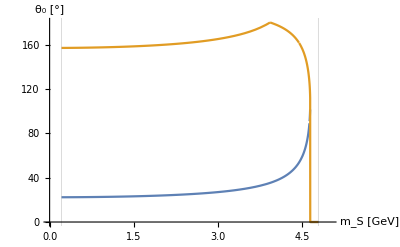

```mathematica
Plot[{θ0min[mS,mK]/°,θ0max[mS,mK]/°},{mS,2mμ/.masses,mB-mK/.masses},AxesLabel->{"m_S [GeV]","θ_0 [°]"},PlotRange->{{0,5},{0,180}},GridLines->{{2mμ/.masses,mB-mK/.masses},{}},AxesStyle->Directive[Black,14],LabelStyle->Directive[Black,16]]
```

### Actual Integral

```mathematica
NintdECL[θ0_?NumericQ,mSp_?NumericQ,α_?NumericQ,mKXp_]:=Block[{a=mSp/(pS cτS[mSp,α]/.HeavisideTheta[0]:>0/.HeavisideTheta[0.]:>0)//.Eptransl/.mKX:>mKXp/.mS:>mSp/.masses/.HeavisideTheta[0]:>0/.HeavisideTheta[0.]:>0,b=Cotθ[θ0,mSp]/.ECLparams/.mKX:>mKXp/.BIIparams/.masses/.mS:>mSp},a/2*NIntegrate[Exp[-(a ρ)/Sin[θ0]]HeavisideTheta[ρ b-zmin] HeavisideTheta[-ρ b + zmax]/.ECLparams/.HeavisideTheta[0]:>0/.HeavisideTheta[0.]:>0,{ρ,dres Sinθ[θ0,mSp]//.Eptransl/.mKX:>mKXp/.mS:>mSp/.masses/.BIIparams,ρmax/.ECLparams}]]/.HeavisideTheta[0]:>0/.HeavisideTheta[0.]:>0
```

```mathematica
NintECL[mSp_?NumericQ,α_?NumericQ,mKXp_,meth_:Automatic,pres_:3]:=NIntegrate[NintdECL[θ0,mSp,α,mKXp],{θ0,θ0min[mSp,mKXp],θ0max[mSp,mKXp]},Method-> meth,PrecisionGoal->pres]
```

```mathematica
mtemp =0.6;
AbsoluteTiming[NintCDC[mtemp,0.0001,mK,Automatic, Automatic]]
AbsoluteTiming[NintCDC[mtemp,0.0001,mK]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {2.33935}. NIntegrate obtained 0.411192 and 3.86241×10^-6 for the integral and error estimates.

{6.80973,0.411192}

{0.929087,0.411175}

```mathematica
NintdCDC[θ0_?NumericQ,mSp_?NumericQ,α_?NumericQ,mKXp_]:=Block[{a=mSp/(pS cτS[mSp,α])//.Eptransl/.mKX:>mKXp/.mS:>mSp/.masses/.HeavisideTheta[0]:>0/.HeavisideTheta[0.]:>0,b=Cotθ[θ0,mSp]/.CDCparams/.mKX:>mKXp/.BIIparams/.masses/.mS:>mSp},a/2*NIntegrate[Exp[-(a ρ)/Sin[θ0]]HeavisideTheta[ρ b-zmin] HeavisideTheta[-ρ b + zmax]/.CDCparams/.HeavisideTheta[0]:>0/.HeavisideTheta[0.]:>0,{ρ,dres Sinθ[θ0,mSp]//.Eptransl/.mKX:>mKXp/.mS:>mSp/.masses/.BIIparams,ρmax/.CDCparams}]]
```

```mathematica
NintCDC[mSp_?NumericQ,α_?NumericQ,mKXp_,meth_:Automatic,pres_:3]:=NIntegrate[NintdCDC[θ0,mSp,α,mKXp],{θ0,θ0min[mSp,mKXp],θ0max[mSp,mKXp]},Method-> meth,PrecisionGoal->pres]
```

### Nastya’s different parametrisation

```mathematica
θs1=N[ArcTan[ρmax/zmax]/.CDCparams];
θs2=N[90°+ArcTan[-zmin/ρmax]/.CDCparams];
```

```mathematica
θs1/°
θs2/°
```

36.9919

119.908

```mathematica
θ0s1[mSp_,mKXp_]:=Block[{ts1=Nθ0ofθ[θs1,mSp,mKXp][[2]]},If[Head[ts1]===Complex,0,ts1]]
θ0s2[mSp_,mKXp_]:=Block[{ts2=(If[θmax[mSp,mKXp]==150°,Nθ0ofθ[θs2,mSp,mKXp][[2]],Nθ0ofθ[θs1,mSp,mKXp][[1]]])},If[Head[ts2]===Complex,0,ts2]]
```

```mathematica
Manipulate[Show[Plot[{(Nθ0ofθ[θp °,mSp,mK][[1]]/°),(Nθ0ofθ[θp °,mSp,mK][[2]]/°)},{θp,0,180},AxesLabel->{"θ [°]","θ_0 [°]"},PlotLabel->StringForm["m_S=``GeV",mSp],GridLines->{{17,ArcTan[ρmax/zmax]/°/.CDCparams,90+ArcTan[-zmin/ρmax]/°/.CDCparams,θmax[mSp,mK]/°,150},{}},PlotRange->{0,180},AxesStyle->Directive[Black,14],LabelStyle->Directive[Black,14]],ListPlot[{{17,θ0min[mSp,mK]/°},{150,θ0max[mSp,mK]/°},{17,θ0max[mSp,mK]/°},{θs1/°,θ0s1[mSp,mK]/°},{θs1/°,θ0s2[mSp,mK]/°},{θs2/°,θ0s2[mSp,mK]/°}}]],{mSp,2mμ/.masses,mB-mK/.masses}]
```

ReplaceAll::reps: {CDCparams} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

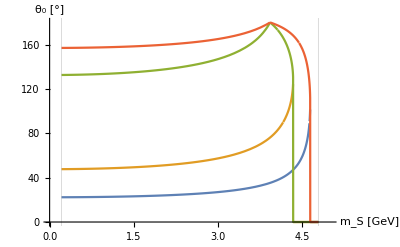

```mathematica
Plot[{θ0min[mS,mK]/°,θ0s1[mS,mK]/°,θ0s2[mS,mK]/°,θ0max[mS,mK]/°},{mS,2mμ/.masses,mB-mK/.masses},AxesLabel->{"m_S [GeV]","θ_0 [°]"},PlotRange->{{0,5},{0,180}},GridLines->{{2mμ/.masses,mB-mK/.masses},{}},AxesStyle->Directive[Black,14],LabelStyle->Directive[Black,16]]
```

```mathematica
rmaxN[θ0_,mS_,mKXp_]:=Piecewise[{{ρmax/Sinθ[θ0,mS],θ0s1[mS,mKXp]<θ0<θ0s2[mS,mKXp]},{zmax/Cosθ[θ0,mS],θ0<θ0s1[mS,mKXp]||(θ0>θ0s2[mS,mKXp]&&θmax[mS,mKXp]≠150°)},{zmin/Cosθ[θ0,mS],θ0>θ0s2[mS,mKXp]&&θmax[mS,mKXp]==150°}}]/.CDCparams/.mKX:>mKXp/.masses/.BIIparams
```

```mathematica
Manipulate[Plot[{zmax/Cosθ[θ0 °,mSp]/.CDCparams/.mKX:>mK/.masses/.BIIparams,ρmax/Sinθ[θ0 °,mSp]/.CDCparams/.mKX:>mK/.masses/.BIIparams,zmin/Cosθ[θ0 °,mSp]/.CDCparams/.mKX:>mK/.masses/.BIIparams,rmaxN[θ0 °,mSp,mK]},{θ0,0,180},PlotRange->{0,200},GridLines->{{θ0min[mSp,mK]/°,θ0s1[mSp,mK]/°,θ0s2[mSp,mK]/°,θ0max[mSp,mK]/°},{}}],{mSp,2mμ/.masses,mB-mK/.masses}]
```

ReplaceAll::reps: {CDCparams} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {BIIparams} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {CDCparams} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
intdN[θ0_?NumericQ,mSp_?NumericQ,α_?NumericQ,mKXp_]:=Block[{a=cτS[mSp,α]/mSp Sqrt[pS^2 Sin[θ0]^2+(γβB ES+γB pS Cos[θ0])^2]/.BIIparams//.Eptransl/.mS:>mSp/.mKX:>mKXp/.masses},Sin[θ0]/2(Exp[-(dres/.BIIparams)/a]-Exp[-rmaxN[θ0,mSp,mKXp]/a])]
```

```mathematica
intN[mSp_?NumericQ,α_?NumericQ,mKXp_]:=NIntegrate[intdN[θ0,mSp,α,mKXp],{θ0,θ0min[mSp,mKXp],θ0max[mSp,mKXp]}]
```

## Branching ratios

### new calculation

```mathematica
ΓBtoSKX[mS_,θ_,mKX_]:=Abs[CSsb[θ]]^2 Sqrt[λ[mS,mKX]]/(16π mB)
CSsb[θ_]:=Sin[θ](mb+ms)/v(3Sqrt[2] GF mt^2 Vtb Vts)/(16π^2)
λ[mS_,mKX_]:=((mB^2-(mS-mKX)^2)(mB^2-(mS+mKX)^2))/mB^4
```

#### P

```mathematica
ΓBtoSKP[mS_,θ_]:=ΓBtoSKX[mS,θ,mK] Abs[(mB^2-mK^2)/(2(mb-ms))fzerop[mS^2]]^2HeavisideTheta[mB-(mK+mS)]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
BrBtoSKP[mS_,α_]:=ΓBtoSKP[mS,α]/ΓtotalB
```

#### S

```mathematica
ΓBtoSKS[mS_,θ_,mKX_,F0_,a_,b_]:=ΓBtoSKX[mS,θ,mKX] Abs[I (mB^2-mKX^2-mS^2)/(2(mb+ms))fplus[mS^2,F0,a,b]]^2HeavisideTheta[mB-(mKX+mS)]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
BrBtoSKS700[mS_,α_]:=ΓBtoSKS[mS,α,mKstarS700,F0BS700,aS700,bS700]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
BrBtoSKS1430[mS_,α_]:=ΓBtoSKS[mS,α,mKstarS1430,F0BS1430,aS1430,bS1430]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms
```

#### V

```mathematica
(* pV=Sqrt[λ]/(2mB) *)
```

```mathematica
ΓBtoSKV[mS_,θ_,mKX_]:=ΓBtoSKX[mS,θ,mKX] Abs[-(mB^2Sqrt[λ[mS,mKX]])/(2(mb+ms))A0[mS^2]]^2HeavisideTheta[mB-(mKX+mS)]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
BrBtoSKV892[mS_,α_]:=ΓBtoSKV[mS,α,mKstarV892]/ΓtotalB/.{A0[msqr_]->Azero[msqr,mKstarV892]}/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
BrBtoSKV1410[mS_,α_]:=ΓBtoSKV[mS,α,mKstarV1410]/ΓtotalB/.{A0->A0V1410}/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
BrBtoSKV1680[mS_,α_]:=ΓBtoSKV[mS,α,mKstarV1680]/ΓtotalB/.{A0->A0V1680}/.formFactors/.values/.masses/.couplings/.ckms
```

#### A

```mathematica
(* pA=Sqrt[λ]/(2mB) *)
```

```mathematica
ΓBtoSKA[mS_,θ_,mKX_]:=ΓBtoSKX[mS,θ,mKX]Abs[(mB^2Sqrt[λ[mS,mKX]])/(2(mb-ms))Vzero[mS^2]]^2HeavisideTheta[mB-(mKX+mS)]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
BrBtoSKA1270[mS_,α_]:=ΓBtoSKA[mS,α,mKAV1270]/ΓtotalB/.Vzero:> V0BK1270/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
BrBtoSKA1400[mS_,α_]:=ΓBtoSKA[mS,α,mKAV1400]/ΓtotalB/.Vzero:> V0BK1400/.formFactors/.values/.masses/.couplings/.ckms
```

### S->ff branching ratios

```mathematica
BrSμμ[mS_,α_]:=Γϕtoμμ[mS,α]/ΓϕBRDM[mS,α,0]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
BrSττ[mS_,α_]:=Γϕtoττ[mS,α]/ΓϕBRDM[mS,α,0]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
BrSππ[mS_,α_]:=Γϕπ[mS,α]/ΓϕBRDM[mS,α,0]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
BrSKK[mS_,α_]:=ΓϕK[mS,α]/ΓϕBRDM[mS,α,0]/.formFactors/.values/.masses/.couplings/.ckms
```

## Decay Numbers

### Single-Kaon Modes

#### only B+ to K+ S->ff

```mathematica
NμμECLK[mS_,α_]:=NBBBelleII BrBtoSKP[mS,α] NintECL[mS,α,mK]BrSμμ[mS,α]/.BIIparams
```

```mathematica
NμμCDCK[mS_,α_]:=NBBBelleII BrBtoSKP[mS,α] NintCDC[mS,α,mK]BrSμμ[mS,α]/.BIIparams
```

```mathematica
NππECLK[mS_,α_]:=NBBBelleII BrBtoSKP[mS,α] NintECL[mS,α,mK]BrSππ[mS,α]/.BIIparams
```

```mathematica
NππCDCK[mS_,α_]:=NBBBelleII BrBtoSKP[mS,α] NintCDC[mS,α,mK]BrSππ[mS,α]/.BIIparams
```

```mathematica
NπKECLK[mS_,α_]:=NBBBelleII BrBtoSKP[mS,α] NintECL[mS,α,mK](BrSππ[mS,α]+BrSKK[mS,α])/.BIIparams
```

```mathematica
NπKCDCK[mS_,α_]:=NBBBelleII BrBtoSKP[mS,α] NintCDC[mS,α,mK](BrSππ[mS,α]+BrSKK[mS,α])/.BIIparams
```

```mathematica
NKKECLK[mS_,α_]:=NBBBelleII BrBtoSKP[mS,α] NintECL[mS,α,mK]BrSKK[mS,α]/.BIIparams
```

```mathematica
NKKCDCK[mS_,α_]:=NBBBelleII BrBtoSKP[mS,α] NintCDC[mS,α,mK]BrSKK[mS,α]/.BIIparams
```

```mathematica
NττECLK[mS_,α_]:=NBBBelleII BrBtoSKP[mS,α] NintECL[mS,α,mK]BrSττ[mS,α]/.BIIparams
```

```mathematica
NττCDCK[mS_,α_]:=NBBBelleII BrBtoSKP[mS,α] NintCDC[mS,α,mK]BrSττ[mS,α]/.BIIparams
```

#### only B+ to K+* (S700) S->ff

```mathematica
NμμECLKS700[mS_,α_]:=NBBBelleII BrBtoSKS700[mS,α] NintECL[mS,α,mKstarS700]BrSμμ[mS,α]/.BIIparams
```

```mathematica
NμμCDCKS700[mS_,α_]:=NBBBelleII BrBtoSKS700[mS,α] NintCDC[mS,α,mKstarS700]BrSμμ[mS,α]/.BIIparams
```

```mathematica
NππECLKS700[mS_,α_]:=NBBBelleII BrBtoSKS700[mS,α] NintECL[mS,α,mKstarS700]BrSππ[mS,α]/.BIIparams
```

```mathematica
NππCDCKS700[mS_,α_]:=NBBBelleII BrBtoSKS700[mS,α] NintCDC[mS,α,mKstarS700]BrSππ[mS,α]/.BIIparams
```

```mathematica
NπKECLKS700[mS_,α_]:=NBBBelleII BrBtoSKS700[mS,α] NintECL[mS,α,mKstarS700](BrSππ[mS,α]+BrSKK[mS,α])/.BIIparams
```

```mathematica
NπKCDCKS700[mS_,α_]:=NBBBelleII BrBtoSKS700[mS,α] NintCDC[mS,α,mKstarS700](BrSππ[mS,α]+BrSKK[mS,α])/.BIIparams
```

```mathematica
NKKECLKS700[mS_,α_]:=NBBBelleII BrBtoSKS700[mS,α] NintECL[mS,α,mKstarS700]BrSKK[mS,α]/.BIIparams
```

```mathematica
NKKCDCKS700[mS_,α_]:=NBBBelleII BrBtoSKS700[mS,α] NintCDC[mS,α,mKstarS700]BrSKK[mS,α]/.BIIparams
```

```mathematica
NττECLKS700[mS_,α_]:=NBBBelleII BrBtoSKS700[mS,α] NintECL[mS,α,mKstarS700]BrSττ[mS,α]/.BIIparams
```

```mathematica
NττCDCKS700[mS_,α_]:=NBBBelleII BrBtoSKS700[mS,α] NintCDC[mS,α,mKstarS700]BrSττ[mS,α]/.BIIparams
```

#### only B+ to K+* (S1430) S->ff

```mathematica
NμμECLKS1430[mS_,α_]:=NBBBelleII BrBtoSKS1430[mS,α] NintECL[mS,α,mKstarS1430]BrSμμ[mS,α]/.BIIparams
```

```mathematica
NμμCDCKS1430[mS_,α_]:=NBBBelleII BrBtoSKS1430[mS,α] NintCDC[mS,α,mKstarS1430]BrSμμ[mS,α]/.BIIparams
```

```mathematica
NππECLKS1430[mS_,α_]:=NBBBelleII BrBtoSKS1430[mS,α] NintECL[mS,α,mKstarS1430]BrSππ[mS,α]/.BIIparams
```

```mathematica
NππCDCKS1430[mS_,α_]:=NBBBelleII BrBtoSKS1430[mS,α] NintCDC[mS,α,mKstarS1430]BrSππ[mS,α]/.BIIparams
```

```mathematica
NπKECLKS1430[mS_,α_]:=NBBBelleII BrBtoSKS1430[mS,α] NintECL[mS,α,mKstarS1430](BrSππ[mS,α]+BrSKK[mS,α])/.BIIparams
```

```mathematica
NπKCDCKS1430[mS_,α_]:=NBBBelleII BrBtoSKS1430[mS,α] NintCDC[mS,α,mKstarS1430](BrSππ[mS,α]+BrSKK[mS,α])/.BIIparams
```

```mathematica
NKKECLKS1430[mS_,α_]:=NBBBelleII BrBtoSKS1430[mS,α] NintECL[mS,α,mKstarS1430]BrSKK[mS,α]/.BIIparams
```

```mathematica
NKKCDCKS1430[mS_,α_]:=NBBBelleII BrBtoSKS1430[mS,α] NintCDC[mS,α,mKstarS1430]BrSKK[mS,α]/.BIIparams
```

```mathematica
NττECLKS1430[mS_,α_]:=NBBBelleII BrBtoSKS1430[mS,α] NintECL[mS,α,mKstarS1430]BrSττ[mS,α]/.BIIparams
```

```mathematica
NττCDCKS1430[mS_,α_]:=NBBBelleII BrBtoSKS1430[mS,α] NintCDC[mS,α,mKstarS1430]BrSττ[mS,α]/.BIIparams
```

#### only B+ to K+* (V892) S->ff

```mathematica
NμμECLKV892[mS_,α_]:=NBBBelleII BrBtoSKV892[mS,α] NintECL[mS,α,mKstarV892]BrSμμ[mS,α]/.BIIparams
```

```mathematica
NμμCDCKV892[mS_,α_]:=NBBBelleII BrBtoSKV892[mS,α] NintCDC[mS,α,mKstarV892]BrSμμ[mS,α]/.BIIparams
```

```mathematica
NππECLKV892[mS_,α_]:=NBBBelleII BrBtoSKV892[mS,α] NintECL[mS,α,mKstarV892]BrSππ[mS,α]/.BIIparams
```

```mathematica
NππCDCKV892[mS_,α_]:=NBBBelleII BrBtoSKV892[mS,α] NintCDC[mS,α,mKstarV892]BrSππ[mS,α]/.BIIparams
```

```mathematica
NπKECLKV892[mS_,α_]:=NBBBelleII BrBtoSKV892[mS,α] NintECL[mS,α,mKstarV892](BrSππ[mS,α]+BrSKK[mS,α])/.BIIparams
```

```mathematica
NπKCDCKV892[mS_,α_]:=NBBBelleII BrBtoSKV892[mS,α] NintCDC[mS,α,mKstarV892](BrSππ[mS,α]+BrSKK[mS,α])/.BIIparams
```

```mathematica
NKKECLKV892[mS_,α_]:=NBBBelleII BrBtoSKV892[mS,α] NintECL[mS,α,mKstarV892]BrSKK[mS,α]/.BIIparams
```

```mathematica
NKKCDCKV892[mS_,α_]:=NBBBelleII BrBtoSKV892[mS,α] NintCDC[mS,α,mKstarV892]BrSKK[mS,α]/.BIIparams
```

```mathematica
NττECLKV892[mS_,α_]:=NBBBelleII BrBtoSKV892[mS,α] NintECL[mS,α,mKstarV892]BrSττ[mS,α]/.BIIparams
```

```mathematica
NττCDCKV892[mS_,α_]:=NBBBelleII BrBtoSKV892[mS,α] NintCDC[mS,α,mKstarV892]BrSττ[mS,α]/.BIIparams
```

#### only B+ to K+* (V1410) S->ff

```mathematica
NμμECLKV1410[mS_,α_]:=NBBBelleII BrBtoSKV1410[mS,α] NintECL[mS,α,mKstarV1410]BrSμμ[mS,α]/.BIIparams
```

```mathematica
NμμCDCKV1410[mS_,α_]:=NBBBelleII BrBtoSKV1410[mS,α] NintCDC[mS,α,mKstarV1410]BrSμμ[mS,α]/.BIIparams
```

```mathematica
NππECLKV1410[mS_,α_]:=NBBBelleII BrBtoSKV1410[mS,α] NintECL[mS,α,mKstarV1410]BrSππ[mS,α]/.BIIparams
```

```mathematica
NππCDCKV1410[mS_,α_]:=NBBBelleII BrBtoSKV1410[mS,α] NintCDC[mS,α,mKstarV1410]BrSππ[mS,α]/.BIIparams
```

```mathematica
NπKECLKV1410[mS_,α_]:=NBBBelleII BrBtoSKV1410[mS,α] NintECL[mS,α,mKstarV1410](BrSππ[mS,α]+BrSKK[mS,α])/.BIIparams
```

```mathematica
NπKCDCKV1410[mS_,α_]:=NBBBelleII BrBtoSKV1410[mS,α] NintCDC[mS,α,mKstarV1410](BrSππ[mS,α]+BrSKK[mS,α])/.BIIparams
```

```mathematica
NKKECLKV1410[mS_,α_]:=NBBBelleII BrBtoSKV1410[mS,α] NintECL[mS,α,mKstarV1410]BrSKK[mS,α]/.BIIparams
```

```mathematica
NKKCDCKV1410[mS_,α_]:=NBBBelleII BrBtoSKV1410[mS,α] NintCDC[mS,α,mKstarV1410]BrSKK[mS,α]/.BIIparams
```

```mathematica
NττECLKV1410[mS_,α_]:=NBBBelleII BrBtoSKV1410[mS,α] NintECL[mS,α,mKstarV1410]BrSττ[mS,α]/.BIIparams
```

```mathematica
NττCDCKV1410[mS_,α_]:=NBBBelleII BrBtoSKV1410[mS,α] NintCDC[mS,α,mKstarV1410]BrSττ[mS,α]/.BIIparams
```

#### only B+ to K+* (V1680) S->ff

```mathematica
NμμECLKV1680[mS_,α_]:=NBBBelleII BrBtoSKV1680[mS,α] NintECL[mS,α,mKstarV1680]BrSμμ[mS,α]/.BIIparams
```

```mathematica
NμμCDCKV1680[mS_,α_]:=NBBBelleII BrBtoSKV1680[mS,α] NintCDC[mS,α,mKstarV1680]BrSμμ[mS,α]/.BIIparams
```

```mathematica
NππECLKV1680[mS_,α_]:=NBBBelleII BrBtoSKV1680[mS,α] NintECL[mS,α,mKstarV1680]BrSππ[mS,α]/.BIIparams
```

```mathematica
NππCDCKV1680[mS_,α_]:=NBBBelleII BrBtoSKV1680[mS,α] NintCDC[mS,α,mKstarV1680]BrSππ[mS,α]/.BIIparams
```

```mathematica
NπKECLKV1680[mS_,α_]:=NBBBelleII BrBtoSKV1680[mS,α] NintECL[mS,α,mKstarV1680](BrSππ[mS,α]+BrSKK[mS,α])/.BIIparams
```

```mathematica
NπKCDCKV1680[mS_,α_]:=NBBBelleII BrBtoSKV1680[mS,α] NintCDC[mS,α,mKstarV1680](BrSππ[mS,α]+BrSKK[mS,α])/.BIIparams
```

```mathematica
NKKECLKV1680[mS_,α_]:=NBBBelleII BrBtoSKV1680[mS,α] NintECL[mS,α,mKstarV1680]BrSKK[mS,α]/.BIIparams
```

```mathematica
NKKCDCKV1680[mS_,α_]:=NBBBelleII BrBtoSKV1680[mS,α] NintCDC[mS,α,mKstarV1680]BrSKK[mS,α]/.BIIparams
```

```mathematica
NττECLKV1680[mS_,α_]:=NBBBelleII BrBtoSKV1680[mS,α] NintECL[mS,α,mKstarV1680]BrSττ[mS,α]/.BIIparams
```

```mathematica
NττCDCKV1680[mS_,α_]:=NBBBelleII BrBtoSKV1680[mS,α] NintCDC[mS,α,mKstarV1680]BrSττ[mS,α]/.BIIparams
```

#### only B+ to K+* (A1270) S->ff

```mathematica
NμμECLKA1270[mS_,α_]:=NBBBelleII BrBtoSKA1270[mS,α] NintECL[mS,α,mKAV1270]BrSμμ[mS,α]/.BIIparams
```

```mathematica
NμμCDCKA1270[mS_,α_]:=NBBBelleII BrBtoSKA1270[mS,α] NintCDC[mS,α,mKAV1270]BrSμμ[mS,α]/.BIIparams
```

```mathematica
NππECLKA1270[mS_,α_]:=NBBBelleII BrBtoSKA1270[mS,α] NintECL[mS,α,mKAV1270]BrSππ[mS,α]/.BIIparams
```

```mathematica
NππCDCKA1270[mS_,α_]:=NBBBelleII BrBtoSKA1270[mS,α] NintCDC[mS,α,mKAV1270]BrSππ[mS,α]/.BIIparams
```

```mathematica
NπKECLKA1270[mS_,α_]:=NBBBelleII BrBtoSKA1270[mS,α] NintECL[mS,α,mKAV1270](BrSππ[mS,α]+BrSKK[mS,α])/.BIIparams
```

```mathematica
NπKCDCKA1270[mS_,α_]:=NBBBelleII BrBtoSKA1270[mS,α] NintCDC[mS,α,mKAV1270](BrSππ[mS,α]+BrSKK[mS,α])/.BIIparams
```

```mathematica
NKKECLKA1270[mS_,α_]:=NBBBelleII BrBtoSKA1270[mS,α] NintECL[mS,α,mKAV1270]BrSKK[mS,α]/.BIIparams
```

```mathematica
NKKCDCKA1270[mS_,α_]:=NBBBelleII BrBtoSKA1270[mS,α] NintCDC[mS,α,mKAV1270]BrSKK[mS,α]/.BIIparams
```

```mathematica
NττECLKA1270[mS_,α_]:=NBBBelleII BrBtoSKA1270[mS,α] NintECL[mS,α,mKAV1270]BrSττ[mS,α]/.BIIparams
```

```mathematica
NττCDCKA1270[mS_,α_]:=NBBBelleII BrBtoSKA1270[mS,α] NintCDC[mS,α,mKAV1270]BrSττ[mS,α]/.BIIparams
```

#### only B+ to K+* (A1400) S->ff

```mathematica
NμμECLKA1400[mS_,α_]:=NBBBelleII BrBtoSKA1400[mS,α] NintECL[mS,α,mKAV1400]BrSμμ[mS,α]/.BIIparams
```

```mathematica
NμμCDCKA1400[mS_,α_]:=NBBBelleII BrBtoSKA1400[mS,α] NintCDC[mS,α,mKAV1400]BrSμμ[mS,α]/.BIIparams
```

```mathematica
NππECLKA1400[mS_,α_]:=NBBBelleII BrBtoSKA1400[mS,α] NintECL[mS,α,mKAV1400]BrSππ[mS,α]/.BIIparams
```

```mathematica
NππCDCKA1400[mS_,α_]:=NBBBelleII BrBtoSKA1400[mS,α] NintCDC[mS,α,mKAV1400]BrSππ[mS,α]/.BIIparams
```

```mathematica
NπKECLKA1400[mS_,α_]:=NBBBelleII BrBtoSKA1400[mS,α] NintECL[mS,α,mKAV1400](BrSππ[mS,α]+BrSKK[mS,α])/.BIIparams
```

```mathematica
NπKCDCKA1400[mS_,α_]:=NBBBelleII BrBtoSKA1400[mS,α] NintCDC[mS,α,mKAV1400](BrSππ[mS,α]+BrSKK[mS,α])/.BIIparams
```

```mathematica
NKKECLKA1400[mS_,α_]:=NBBBelleII BrBtoSKA1400[mS,α] NintECL[mS,α,mKAV1400]BrSKK[mS,α]/.BIIparams
```

```mathematica
NKKCDCKA1400[mS_,α_]:=NBBBelleII BrBtoSKA1400[mS,α] NintCDC[mS,α,mKAV1400]BrSKK[mS,α]/.BIIparams
```

```mathematica
NττECLKA1400[mS_,α_]:=NBBBelleII BrBtoSKA1400[mS,α] NintECL[mS,α,mKAV1400]BrSττ[mS,α]/.BIIparams
```

```mathematica
NττCDCKA1400[mS_,α_]:=NBBBelleII BrBtoSKA1400[mS,α] NintCDC[mS,α,mKAV1400]BrSττ[mS,α]/.BIIparams
```

### Sum over all kaons

```mathematica
NμμECL[mS_,α_]:=1.93(NμμECLK[mS,α]+NμμECLKS700[mS,α]+NμμECLKS1430[mS,α]+NμμECLKV892[mS,α]+NμμECLKV1410[mS,α]+NμμECLKV1680[mS,α]+NμμECLKA1270[mS,α]+NμμECLKA1400[mS,α])
```

```mathematica
NμμCDC[mS_,α_]:=1.93(NμμCDCK[mS,α]+NμμCDCKS700[mS,α]+NμμCDCKS1430[mS,α]+NμμCDCKV892[mS,α]+NμμCDCKV1410[mS,α]+NμμCDCKV1680[mS,α]+NμμCDCKA1270[mS,α]+NμμCDCKA1400[mS,α])
```

```mathematica
NππECL[mS_,α_]:=1.93(NππECLK[mS,α]+NππECLKS700[mS,α]+NππECLKS1430[mS,α]+NππECLKV892[mS,α]+NππECLKV1410[mS,α]+NππECLKV1680[mS,α]+NππECLKA1270[mS,α]+NππECLKA1400[mS,α])
```

```mathematica
NππCDC[mS_,α_]:=1.93(NππCDCK[mS,α]+NππCDCKS700[mS,α]+NππCDCKS1430[mS,α]+NππCDCKV892[mS,α]+NππCDCKV1410[mS,α]+NππCDCKV1680[mS,α]+NππCDCKA1270[mS,α]+NππCDCKA1400[mS,α])
```

```mathematica
NKKECL[mS_,α_]:=1.93(NKKECLK[mS,α]+NKKECLKS700[mS,α]+NKKECLKS1430[mS,α]+NKKECLKV892[mS,α]+NKKECLKV1410[mS,α]+NKKECLKV1680[mS,α]+NKKECLKA1270[mS,α]+NKKECLKA1400[mS,α])
```

```mathematica
NKKCDC[mS_,α_]:=1.93(NKKCDCK[mS,α]+NKKCDCKS700[mS,α]+NKKCDCKS1430[mS,α]+NKKCDCKV892[mS,α]+NKKCDCKV1410[mS,α]+NKKCDCKV1680[mS,α]+NKKCDCKA1270[mS,α]+NKKCDCKA1400[mS,α])
```

```mathematica
NπKECL[mS_,α_]:=1.93(NπKECLK[mS,α]+NπKECLKS700[mS,α]+NπKECLKS1430[mS,α]+NπKECLKV892[mS,α]+NπKECLKV1410[mS,α]+NπKECLKV1680[mS,α]+NπKECLKA1270[mS,α]+NπKECLKA1400[mS,α])
```

```mathematica
NπKCDC[mS_,α_]:=1.93(NπKCDCK[mS,α]+NπKCDCKS700[mS,α]+NπKCDCKS1430[mS,α]+NπKCDCKV892[mS,α]+NπKCDCKV1410[mS,α]+NπKCDCKV1680[mS,α]+NπKCDCKA1270[mS,α]+NπKCDCKA1400[mS,α])
```

```mathematica
NττECL[mS_,α_]:=1.93(NττECLK[mS,α]+NττECLKS700[mS,α]+NττECLKS1430[mS,α]+NττECLKV892[mS,α]+NττECLKV1410[mS,α]+NττECLKV1680[mS,α]+NττECLKA1270[mS,α]+NττECLKA1400[mS,α])
```

```mathematica
NττCDC[mS_,α_]:=1.93(NττCDCK[mS,α]+NττCDCKS700[mS,α]+NττCDCKS1430[mS,α]+NττCDCKV892[mS,α]+NττCDCKV1410[mS,α]+NττCDCKV1680[mS,α]+NττCDCKA1270[mS,α]+NττCDCKA1400[mS,α])
```

### Checks

```mathematica
NμμECL[3,0.0001]//Timing
NμμCDC[3,0.0001]//Timing
NππECL[1,0.0001]//Timing
NππCDC[1,0.0001]//Timing
NKKECL[1,0.0001]//Timing
NKKCDC[1,0.0001]//Timing
NττECL[4,0.0001]//Timing
NττCDC[4,0.0001]//Timing
```

InterpolatingFunction::dmval: Input value {3} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0.90625,215.633+0. ⅈ}

InterpolatingFunction::dmval: Input value {3} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0.84375,215.633+0. ⅈ}

{0.6875,1959.88+0. ⅈ}

{0.71875,1959.87+0. ⅈ}

{0.6875,854.759+0. ⅈ}

{0.71875,854.756+0. ⅈ}

InterpolatingFunction::dmval: Input value {4} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

{0.640625,293.947+0. ⅈ}

InterpolatingFunction::dmval: Input value {4} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

{0.640625,293.947+0. ⅈ}

## Plots

### Colours

```mathematica
myColours={ColorData[3,"ColorList"][[6]],Darker[ColorData[3,"ColorList"][[6]]],ColorData[3,"ColorList"][[2]],Darker[ColorData[3,"ColorList"][[2]]],ColorData[3,"ColorList"][[4]],Darker[ColorData[3,"ColorList"][[4]]],ColorData[3,"ColorList"][[3]],Darker[ColorData[3,"ColorList"][[3]]],Black}
```

{RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.005228758169934641, 0.33986928104575165, 0.6196078431372549],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.6640522875816994, 0.24052287581699347, 0.018300653594771243],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.3607843137254902, 0.4758169934640523, 0.018300653594771243],RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882],RGBColor[0.6640522875816994, 0.6588235294117648, 0.023529411764705882],GrayLevel[0]}

```mathematica
Table[ColorData[i,"ColorList"],{i,1,96}]
```

{{RGBColor[0.24720000000000014, 0.24, 0.6],RGBColor[0.6, 0.24, 0.4428931686004542],RGBColor[0.6, 0.5470136627990908, 0.24],RGBColor[0.24, 0.6, 0.33692049419863584],RGBColor[0.24, 0.3531726744018182, 0.6],RGBColor[0.6, 0.24, 0.5632658430022722],RGBColor[0.6, 0.42664098839727194, 0.24],RGBColor[0.2634521802031821, 0.6, 0.24],RGBColor[0.24, 0.47354534880363613, 0.6],RGBColor[0.5163614825959097, 0.24, 0.6],RGBColor[0.6, 0.3062683139954558, 0.24],RGBColor[0.3838248546049982, 0.6, 0.24],RGBColor[0.24, 0.5939180232054561, 0.6],RGBColor[0.39598880819409377, 0.24, 0.6],RGBColor[0.6, 0.24, 0.2941043604063603]},{RGBColor[0.8588235294117647, 0.00784313725490196, 0.00784313725490196],RGBColor[1., 0.26666666666666666, 0.],RGBColor[1., 0.4549019607843137, 0.2549019607843137],RGBColor[0.4823529411764706, 0.18823529411764706, 0.03529411764705882],RGBColor[1., 0.8784313725490196, 0.5058823529411764],RGBColor[0.7019607843137254, 0.7450980392156863, 0.8235294117647058],RGBColor[0.20784313725490197, 0.23921568627450981, 0.3215686274509804],RGBColor[0.08627450980392157, 0.1411764705882353, 0.28627450980392155],RGBColor[0.33725490196078434, 0.403921568627451, 0.6235294117647059]},{RGBColor[0., 0., 0.],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.15294117647058825, 0.11372549019607843, 0.49019607843137253],RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961],RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253],RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237]},{RGBColor[0.2235294117647059, 0.2235294117647059, 0.2235294117647059],RGBColor[0.21176470588235294, 0.13725490196078433, 0.11372549019607843],RGBColor[0.5372549019607843, 0.3843137254901961, 0.2549019607843137],RGBColor[0.4235294117647059, 0.3254901960784314, 0.20784313725490197],RGBColor[0.9372549019607843, 0.7607843137254902, 0.403921568627451],RGBColor[0.996078431372549, 0.9058823529411765, 0.38823529411764707],RGBColor[0.6235294117647059, 0.592156862745098, 0.4],RGBColor[0.6980392156862745, 0.6745098039215687, 0.3686274509803922],RGBColor[0.41568627450980394, 0.45098039215686275, 0.3764705882352941],RGBColor[0.3333333333333333, 0.38823529411764707, 0.2901960784313726]},{RGBColor[0.4588235294117647, 0.1411764705882353, 0.1411764705882353],RGBColor[0.6274509803921569, 0.23137254901960785, 0.23137254901960785],RGBColor[0.3803921568627451, 0.2784313725490196, 0.20784313725490197],RGBColor[0.5882352941176471, 0.44313725490196076, 0.33725490196078434],RGBColor[0.592156862745098, 0.4196078431372549, 0.2823529411764706],RGBColor[0.8235294117647058, 0.5019607843137255, 0.09411764705882353],RGBColor[0.9764705882352941, 0.6901960784313725, 0.3215686274509804],RGBColor[0.396078431372549, 0.396078431372549, 0.17647058823529413],RGBColor[0.41568627450980394, 0.41568627450980394, 0.3058823529411765],RGBColor[0.6313725490196078, 0.6313725490196078, 0.24705882352941178]},{RGBColor[0.3411764705882353, 0.3411764705882353, 0.3411764705882353],RGBColor[0.6431372549019608, 0.10588235294117647, 0.043137254901960784],RGBColor[0.19215686274509805, 0.10588235294117647, 0.06274509803921569],RGBColor[0.792156862745098, 0.7333333333333333, 0.611764705882353],RGBColor[0.8117647058823529, 0.596078431372549, 0.027450980392156862],RGBColor[0.10588235294117647, 0.2549019607843137, 0.1607843137254902],RGBColor[0.12549019607843137, 0.30980392156862746, 0.42745098039215684],RGBColor[0.0784313725490196, 0.1450980392156863, 0.3176470588235294],RGBColor[0.6588235294117647, 0.6039215686274509, 0.7019607843137254],RGBColor[0.5215686274509804, 0.4196078431372549, 0.4549019607843137],RGBColor[0.48627450980392156, 0.03137254901960784, 0.09411764705882353]},{RGBColor[0.5019607843137255, 0.4980392156862745, 0.4980392156862745],RGBColor[0.796078431372549, 0.5137254901960784, 0.4980392156862745],RGBColor[0.40784313725490196, 0.24313725490196078, 0.20784313725490197],RGBColor[0.803921568627451, 0.6862745098039216, 0.6039215686274509],RGBColor[0.28627450980392155, 0.23921568627450981, 0.2],RGBColor[0.7568627450980392, 0.7058823529411765, 0.5764705882352941],RGBColor[0.6980392156862745, 0.7254901960784313, 0.5647058823529412],RGBColor[0.4588235294117647, 0.5764705882352941, 0.5058823529411764],RGBColor[0.5725490196078431, 0.6313725490196078, 0.6705882352941176],RGBColor[0.3411764705882353, 0.34509803921568627, 0.34901960784313724],RGBColor[0.2627450980392157, 0.3411764705882353, 0.4470588235294118]},{RGBColor[0.611764705882353, 0.2980392156862745, 0.29411764705882354],RGBColor[1., 0.8549019607843137, 0.8274509803921568],RGBColor[0.8588235294117647, 0.5607843137254902, 0.4588235294117647],RGBColor[0.6549019607843137, 0.2980392156862745, 0.08235294117647059],RGBColor[0.8705882352941177, 0.9254901960784314, 0.21568627450980393],RGBColor[0.5019607843137255, 0.6862745098039216, 0.03529411764705882],RGBColor[0.21568627450980393, 0.36470588235294116, 0.16470588235294117],RGBColor[0.24313725490196078, 0.3176470588235294, 0.30980392156862746],RGBColor[0.6862745098039216, 0.19215686274509805, 0.24705882352941178]},{RGBColor[0.9372549019607843, 0.6470588235294118, 0.6431372549019608],RGBColor[0.6745098039215687, 0.07450980392156863, 0.043137254901960784],RGBColor[0.8627450980392157, 0.5215686274509804, 0.34509803921568627],RGBColor[0.9686274509803922, 0.6039215686274509, 0.],RGBColor[0.38823529411764707, 0.42745098039215684, 0.396078431372549],RGBColor[0.11764705882352941, 0.10588235294117647, 0.3843137254901961],RGBColor[0.09411764705882353, 0.08235294117647059, 0.2901960784313726],RGBColor[0.2823529411764706, 0.21176470588235294, 0.27450980392156865],RGBColor[0.6470588235294118, 0.5686274509803921, 0.611764705882353]},{RGBColor[0.6980392156862745, 0.01568627450980392, 0.],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217],RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253],RGBColor[0.7254901960784313, 0.8, 0.07058823529411765],RGBColor[0.3176470588235294, 0.49019607843137253, 0.0784313725490196],RGBColor[0.17254901960784313, 0.3607843137254902, 0.07058823529411765],RGBColor[0.3607843137254902, 0.40784313725490196, 0.5333333333333333],RGBColor[0.22745098039215686, 0.23921568627450981, 0.45098039215686275],RGBColor[0.09803921568627451, 0.06666666666666667, 0.25098039215686274],RGBColor[0.5607843137254902, 0.5254901960784314, 0.5647058823529412]},{RGBColor[0.6588235294117647, 0.3411764705882353, 0.32941176470588235],RGBColor[0.8823529411764706, 0.28627450980392155, 0.20392156862745098],RGBColor[0.8901960784313725, 0.788235294117647, 0.6509803921568628],RGBColor[0.6666666666666666, 0.5058823529411764, 0.19607843137254902],RGBColor[0.6666666666666666, 0.6980392156862745, 0.403921568627451],RGBColor[0.5843137254901961, 0.7725490196078432, 0.3411764705882353],RGBColor[0.7137254901960784, 0.7607843137254902, 0.9176470588235294],RGBColor[0.6549019607843137, 0.6509803921568628, 0.8156862745098039]},{RGBColor[0.6235294117647059, 0.1450980392156863, 0.12549019607843137],RGBColor[0.6588235294117647, 0.3058823529411765, 0.17254901960784313],RGBColor[0.24313725490196078, 0.11764705882352941, 0.058823529411764705],RGBColor[0.9450980392156862, 0.7529411764705882, 0.6352941176470588],RGBColor[0.8392156862745098, 0.4745098039215686, 0.21176470588235294],RGBColor[0.8274509803921568, 0.7254901960784313, 0.43529411764705883],RGBColor[0.44313725490196076, 0.4980392156862745, 0.5490196078431373],RGBColor[0.24705882352941178, 0.30980392156862746, 0.37254901960784315],RGBColor[0.16862745098039217, 0.23921568627450981, 0.3803921568627451],RGBColor[0.2980392156862745, 0.17647058823529413, 0.19607843137254902]},{RGBColor[0.6588235294117647, 0.4980392156862745, 0.49019607843137253],RGBColor[0.7215686274509804, 0.1843137254901961, 0.050980392156862744],RGBColor[0.803921568627451, 0.5450980392156862, 0.4588235294117647],RGBColor[0.8156862745098039, 0.6901960784313725, 0.6313725490196078],RGBColor[0.9490196078431372, 0.8745098039215686, 0.7176470588235294],RGBColor[0.3803921568627451, 0.3843137254901961, 0.6352941176470588],RGBColor[0.23137254901960785, 0.20784313725490197, 0.5529411764705883],RGBColor[0.5843137254901961, 0.5607843137254902, 0.6627450980392157],RGBColor[0.4666666666666667, 0.27450980392156865, 0.34901960784313724],RGBColor[0.596078431372549, 0.27450980392156865, 0.36470588235294116]},{RGBColor[0.8352941176470589, 0.5764705882352941, 0.5607843137254902],RGBColor[0.9490196078431372, 0.29411764705882354, 0.050980392156862744],RGBColor[1., 0.7333333333333333, 0.2],RGBColor[0.996078431372549, 0.9490196078431372, 0.44313725490196076],RGBColor[0.7058823529411765, 0.6862745098039216, 0.30196078431372547],RGBColor[0.41568627450980394, 0.5450980392156862, 0.12156862745098039],RGBColor[0.0196078431372549, 0.20784313725490197, 0.4627450980392157],RGBColor[0.6862745098039216, 0.7215686274509804, 0.8117647058823529],RGBColor[0.42745098039215684, 0.06666666666666667, 0.1568627450980392],RGBColor[0.8549019607843137, 0.19607843137254902, 0.27450980392156865]},{RGBColor[0.40784313725490196, 0.15294117647058825, 0.13725490196078433],RGBColor[0.6588235294117647, 0.5607843137254902, 0.5333333333333333],RGBColor[0.8313725490196079, 0.43529411764705883, 0.12941176470588237],RGBColor[0.8941176470588236, 0.8274509803921568, 0.7647058823529411],RGBColor[0.9372549019607843, 0.7764705882352941, 0.3137254901960784],RGBColor[0.23921568627450981, 0.27058823529411763, 0.4627450980392157],RGBColor[0.23529411764705882, 0.1450980392156863, 0.4588235294117647],RGBColor[0.36470588235294116, 0.23921568627450981, 0.43137254901960786],RGBColor[0.2196078431372549, 0.12549019607843137, 0.18823529411764706],RGBColor[0.5529411764705883, 0.12941176470588237, 0.2235294117647059],RGBColor[0.7058823529411765, 0.2627450980392157, 0.27058823529411763]},{RGBColor[0.4549019607843137, 0.050980392156862744, 0.023529411764705882],RGBColor[0.6784313725490196, 0.3137254901960784, 0.],RGBColor[0.9058823529411765, 0.6392156862745098, 0.07058823529411765],RGBColor[0.16470588235294117, 0.41568627450980394, 0.11764705882352941],RGBColor[0.8549019607843137, 0.9607843137254902, 1.],RGBColor[0.12156862745098039, 0.5098039215686274, 0.7333333333333333],RGBColor[0.6392156862745098, 0.5607843137254902, 0.7529411764705882],RGBColor[0.1450980392156863, 0.11372549019607843, 0.16470588235294117],RGBColor[0.9411764705882353, 0., 0.00784313725490196]},{RGBColor[0.2823529411764706, 0.22745098039215686, 0.2235294117647059],RGBColor[0.5647058823529412, 0.23137254901960785, 0.15294117647058825],RGBColor[0.6392156862745098, 0.39215686274509803, 0.3333333333333333],RGBColor[0.8627450980392157, 0.6196078431372549, 0.2627450980392157],RGBColor[0.9647058823529412, 0.788235294117647, 0.5254901960784314],RGBColor[0.4588235294117647, 0.592156862745098, 0.4627450980392157],RGBColor[0.23921568627450981, 0.45098039215686275, 0.24705882352941178],RGBColor[0.34509803921568627, 0.5803921568627451, 0.6901960784313725],RGBColor[0.1843137254901961, 0.39215686274509803, 0.49019607843137253],RGBColor[0.5686274509803921, 0.7490196078431373, 0.8431372549019608]},{RGBColor[0.7647058823529411, 0.5568627450980392, 0.5411764705882353],RGBColor[0.9921568627450981, 0.788235294117647, 0.7568627450980392],RGBColor[0.29411764705882354, 0.19215686274509805, 0.10588235294117647],RGBColor[0.37254901960784315, 0.2784313725490196, 0.19215686274509805],RGBColor[0.29411764705882354, 0.27058823529411763, 0.18823529411764706],RGBColor[0.7098039215686275, 0.6980392156862745, 0.5058823529411764],RGBColor[0.8705882352941177, 0.8784313725490196, 0.6901960784313725],RGBColor[0.27058823529411763, 0.33725490196078434, 0.28627450980392155],RGBColor[0.6980392156862745, 0.43529411764705883, 0.4470588235294118]},{RGBColor[0.5686274509803921, 0.043137254901960784, 0.],RGBColor[0.5607843137254902, 0.22745098039215686, 0.2],RGBColor[0.6627450980392157, 0.3333333333333333, 0.],RGBColor[0.8470588235294118, 0.6392156862745098, 0.42745098039215684],RGBColor[0.7686274509803922, 0.4627450980392157, 0.14901960784313725],RGBColor[0.01568627450980392, 0.19215686274509805, 0.09803921568627451],RGBColor[0.19215686274509805, 0.3686274509803922, 0.27450980392156865],RGBColor[0.4, 0.5254901960784314, 0.4588235294117647],RGBColor[0.06666666666666667, 0.15294117647058825, 0.20784313725490197]},{RGBColor[0.7450980392156863, 0.06666666666666667, 0.00392156862745098],RGBColor[0.9019607843137255, 0.19607843137254902, 0.12941176470588237],RGBColor[0.3568627450980392, 0.054901960784313725, 0.01568627450980392],RGBColor[0.6823529411764706, 0.41568627450980394, 0.],RGBColor[0.8352941176470589, 0.6274509803921569, 0.08627450980392157],RGBColor[0.9803921568627451, 0.7803921568627451, 0.25882352941176473],RGBColor[1., 0.9058823529411765, 0.6549019607843137],RGBColor[0.3843137254901961, 0.6, 0.8784313725490196],RGBColor[0.06274509803921569, 0.25882352941176473, 0.5137254901960784],RGBColor[0.12549019607843137, 0.36470588235294116, 0.6784313725490196]},{RGBColor[0.9411764705882353, 0.49411764705882355, 0.45098039215686275],RGBColor[0.8745098039215686, 0.4666666666666667, 0.32941176470588235],RGBColor[1., 0.35294117647058826, 0.12156862745098039],RGBColor[0.9725490196078431, 0.8, 0.5450980392156862],RGBColor[0.9137254901960784, 0.803921568627451, 0.6078431372549019],RGBColor[0.7843137254901961, 0.6901960784313725, 0.5176470588235295],RGBColor[0.4588235294117647, 0.37254901960784315, 0.18823529411764706],RGBColor[0.6941176470588235, 0.6235294117647059, 0.3803921568627451],RGBColor[0.43529411764705883, 0.30980392156862746, 0.3764705882352941],RGBColor[0.20392156862745098, 0.0784313725490196, 0.12156862745098039]},{RGBColor[0.40784313725490196, 0.06666666666666667, 0.03137254901960784],RGBColor[0.8627450980392157, 0.403921568627451, 0.027450980392156862],RGBColor[0.9372549019607843, 0.7764705882352941, 0.],RGBColor[0.6392156862745098, 0.7568627450980392, 0.8980392156862745],RGBColor[0.3137254901960784, 0.3686274509803922, 0.6470588235294118],RGBColor[0.596078431372549, 0.5529411764705883, 0.8117647058823529],RGBColor[0.15294117647058825, 0.050980392156862744, 0.10196078431372549],RGBColor[0.8705882352941177, 0.5333333333333333, 0.6392156862745098],RGBColor[0.7215686274509804, 0.13333333333333333, 0.24705882352941178]},{RGBColor[0.35294117647058826, 0.043137254901960784, 0.],RGBColor[0.44313725490196076, 0.17254901960784313, 0.0196078431372549],RGBColor[0.42745098039215684, 0.2, 0.054901960784313725],RGBColor[0.8509803921568627, 0.5568627450980392, 0.32941176470588235],RGBColor[0.9607843137254902, 0.7529411764705882, 0.5568627450980392],RGBColor[0.7725490196078432, 0.5568627450980392, 0.24313725490196078],RGBColor[0.803921568627451, 0.5333333333333333, 0.13725490196078433],RGBColor[0.9333333333333333, 0.7215686274509804, 0.34509803921568627]},{RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[1., 0.7215686274509804, 0.2196078431372549],RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883],RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843],RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],RGBColor[0.12941176470588237, 0.5176470588235295, 0.6313725490196078],RGBColor[0.09019607843137255, 0.33725490196078434, 0.49411764705882355],RGBColor[0.7058823529411765, 0.49411764705882355, 0.5450980392156862],RGBColor[0.5333333333333333, 0.23529411764705882, 0.3058823529411765],RGBColor[0.8941176470588236, 0.7098039215686275, 0.7490196078431373]},{RGBColor[0.20392156862745098, 0.03529411764705882, 0.00392156862745098],RGBColor[0.6, 0.16470588235294117, 0.07450980392156863],RGBColor[0.3411764705882353, 0.06274509803921569, 0.00392156862745098],RGBColor[0.796078431372549, 0.4, 0.09019607843137255],RGBColor[0.796078431372549, 0.4823529411764706, 0.19215686274509805],RGBColor[0.6705882352941176, 0.4666666666666667, 0.24705882352941178],RGBColor[0.3843137254901961, 0.24313725490196078, 0.027450980392156862],RGBColor[0.49411764705882355, 0.3607843137254902, 0.023529411764705882],RGBColor[0.14901960784313725, 0.2, 0.043137254901960784]},{RGBColor[0.47058823529411764, 0.14901960784313725, 0.08627450980392157],RGBColor[0.9098039215686274, 0.3607843137254902, 0.21568627450980393],RGBColor[0.8705882352941177, 0.3607843137254902, 0.050980392156862744],RGBColor[0.803921568627451, 0.7254901960784313, 0.6313725490196078],RGBColor[0.4392156862745098, 0.27450980392156865, 0.06666666666666667],RGBColor[0.9254901960784314, 0.8549019607843137, 0.7529411764705882],RGBColor[0.9176470588235294, 0.6862745098039216, 0.32941176470588235],RGBColor[0.3254901960784314, 0.4549019607843137, 0.4745098039215686]},{RGBColor[0.6549019607843137, 0.10980392156862745, 0.],RGBColor[0.9803921568627451, 0.7294117647058823, 0.5490196078431373],RGBColor[0.9490196078431372, 0.596078431372549, 0.2196078431372549],RGBColor[0.996078431372549, 1., 0.8588235294117647],RGBColor[0.37254901960784315, 0.5333333333333333, 0.3686274509803922],RGBColor[0.8666666666666667, 0.9294117647058824, 0.8901960784313725],RGBColor[0.49019607843137253, 0.7176470588235294, 0.6235294117647059],RGBColor[0.49019607843137253, 0.6627450980392157, 0.6745098039215687],RGBColor[0.6235294117647059, 0.807843137254902, 0.8705882352941177],RGBColor[0.8, 0.43529411764705883, 0.5176470588235295]},{RGBColor[0.9058823529411765, 0.3803921568627451, 0.27450980392156865],RGBColor[0.8392156862745098, 0.5529411764705883, 0.47843137254901963],RGBColor[0.6549019607843137, 0.4392156862745098, 0.3607843137254902],RGBColor[0.9647058823529412, 0.7058823529411765, 0.17254901960784313],RGBColor[0.8196078431372549, 0.7411764705882353, 0.2980392156862745],RGBColor[0.03529411764705882, 0.49411764705882355, 0.7058823529411765],RGBColor[0.24705882352941178, 0.44313725490196076, 0.5803921568627451],RGBColor[0., 0.4745098039215686, 0.8549019607843137],RGBColor[0.6431372549019608, 0.4196078431372549, 0.47843137254901963]},{RGBColor[0.7568627450980392, 0.28627450980392155, 0.18823529411764706],RGBColor[0.7372549019607844, 0.37254901960784315, 0.2],RGBColor[0.7843137254901961, 0.6274509803921569, 0.49019607843137253],RGBColor[0.8509803921568627, 0.6862745098039216, 0.15294117647058825],RGBColor[0.3333333333333333, 0.2980392156862745, 0.17647058823529413],RGBColor[0.6784313725490196, 0.7176470588235294, 0.6196078431372549],RGBColor[0.21176470588235294, 0.3215686274509804, 0.5686274509803921],RGBColor[0., 0.09019607843137255, 0.3411764705882353],RGBColor[0.4549019607843137, 0.30196078431372547, 0.3137254901960784],RGBColor[0.49019607843137253, 0.27058823529411763, 0.2823529411764706]},{RGBColor[0.23137254901960785, 0.17647058823529413, 0.16470588235294117],RGBColor[0.36470588235294116, 0.1843137254901961, 0.12549019607843137],RGBColor[0.5333333333333333, 0.26666666666666666, 0.11372549019607843],RGBColor[0.6431372549019608, 0.5215686274509804, 0.2],RGBColor[0.8705882352941177, 0.8901960784313725, 0.6784313725490196],RGBColor[0.6784313725490196, 0.7725490196078432, 0.6705882352941176],RGBColor[0.4117647058823529, 0.5254901960784314, 0.5490196078431373],RGBColor[0.4, 0.403921568627451, 0.4117647058823529],RGBColor[0.5176470588235295, 0.5098039215686274, 0.5137254901960784]},{RGBColor[0.8705882352941177, 0.30980392156862746, 0.1450980392156863],RGBColor[0.9803921568627451, 0.37254901960784315, 0.19215686274509805],RGBColor[0.4196078431372549, 0.21176470588235294, 0.1411764705882353],RGBColor[0.8980392156862745, 0.611764705882353, 0.45098039215686275],RGBColor[0.7725490196078432, 0.5098039215686274, 0.15294117647058825],RGBColor[0.8352941176470589, 0.7333333333333333, 0.2],RGBColor[0.596078431372549, 0.8196078431372549, 0.6901960784313725],RGBColor[0.2196078431372549, 0.5568627450980392, 0.37254901960784315],RGBColor[0.23921568627450981, 0.4196078431372549, 0.5215686274509804]},{RGBColor[0.4, 0.10196078431372549, 0.],RGBColor[0.9803921568627451, 0.807843137254902, 0.7333333333333333],RGBColor[0.7490196078431373, 0.43529411764705883, 0.24705882352941178],RGBColor[0.8235294117647058, 0.6039215686274509, 0.34901960784313724],RGBColor[0.4745098039215686, 0.3607843137254902, 0.11764705882352941],RGBColor[0.8352941176470589, 0.7372549019607844, 0.5058823529411764],RGBColor[1., 0.9098039215686274, 0.6627450980392157],RGBColor[0.8588235294117647, 0.9254901960784314, 0.7764705882352941],RGBColor[0.4588235294117647, 0.25098039215686274, 0.2901960784313726]},{RGBColor[0.5882352941176471, 0.3058823529411765, 0.20784313725490197],RGBColor[0.7411764705882353, 0.5294117647058824, 0.3843137254901961],RGBColor[0.8509803921568627, 0.7333333333333333, 0.592156862745098],RGBColor[0.8235294117647058, 0.7254901960784313, 0.39215686274509803],RGBColor[0.8823529411764706, 0.8196078431372549, 0.6039215686274509],RGBColor[0.5843137254901961, 0.6705882352941176, 0.43529411764705883],RGBColor[0.8352941176470589, 0.8784313725490196, 0.7607843137254902],RGBColor[0.3137254901960784, 0.43529411764705883, 0.10588235294117647]},{RGBColor[0.4, 0.3254901960784314, 0.2901960784313726],RGBColor[0.6705882352941176, 0.6274509803921569, 0.49411764705882355],RGBColor[0.796078431372549, 0.803921568627451, 0.7725490196078432],RGBColor[0.8705882352941177, 0.9490196078431372, 0.7176470588235294],RGBColor[0.6705882352941176, 0.7607843137254902, 0.615686274509804],RGBColor[0.9490196078431372, 0.9803921568627451, 0.9882352941176471]},{RGBColor[0.803921568627451, 0.30980392156862746, 0.07058823529411765],RGBColor[1., 0.7254901960784313, 0.09411764705882353],RGBColor[0.9568627450980393, 0.796078431372549, 0.13725490196078433],RGBColor[0.9529411764705882, 0.9803921568627451, 0.5725490196078431],RGBColor[0.4117647058823529, 0.592156862745098, 0.4],RGBColor[0.30980392156862746, 0.47058823529411764, 0.34509803921568627],RGBColor[0.2980392156862745, 0.28627450980392155, 0.5490196078431373],RGBColor[0.27058823529411763, 0.1843137254901961, 0.3764705882352941],RGBColor[0.8784313725490196, 0.10196078431372549, 0.20784313725490197],RGBColor[0.8, 0.058823529411764705, 0.07450980392156863]},{RGBColor[0.8235294117647058, 0.7333333333333333, 0.6862745098039216],RGBColor[0.40784313725490196, 0.42745098039215684, 0.26666666666666666],RGBColor[0.615686274509804, 0.6862745098039216, 0.48627450980392156],RGBColor[0.33725490196078434, 0.43529411764705883, 0.39215686274509803],RGBColor[0.5254901960784314, 0.592156862745098, 0.6],RGBColor[0.4235294117647059, 0.4588235294117647, 0.4823529411764706],RGBColor[0.39215686274509803, 0.49411764705882355, 0.5686274509803921],RGBColor[0.6078431372549019, 0.5607843137254902, 0.5803921568627451]},{RGBColor[0.8549019607843137, 0.39215686274509803, 0.14901960784313725],RGBColor[0.7176470588235294, 0.27450980392156865, 0.0392156862745098],RGBColor[1., 0.5568627450980392, 0.3215686274509804],RGBColor[1., 0.807843137254902, 0.4627450980392157],RGBColor[0.8156862745098039, 0.6078431372549019, 0.23137254901960785],RGBColor[0.6588235294117647, 0.596078431372549, 0.27058823529411763],RGBColor[0.9294117647058824, 0.9058823529411765, 0.7803921568627451],RGBColor[0.8117647058823529, 0.7607843137254902, 0.47843137254901963],RGBColor[0.6588235294117647, 0.7803921568627451, 0.9411764705882353],RGBColor[0.4235294117647059, 0.6039215686274509, 0.8431372549019608],RGBColor[0.2, 0.41568627450980394, 0.7019607843137254]},{RGBColor[0.5686274509803921, 0.2980392156862745, 0.1450980392156863],RGBColor[0.7058823529411765, 0.6980392156862745, 0.4980392156862745],RGBColor[0.6509803921568628, 0.7607843137254902, 0.22745098039215686],RGBColor[0.39215686274509803, 0.7294117647058823, 0.5843137254901961],RGBColor[0.8235294117647058, 0.8941176470588236, 0.9490196078431372],RGBColor[0.22745098039215686, 0.19215686274509805, 0.4],RGBColor[0.5019607843137255, 0.23921568627450981, 0.4470588235294118],RGBColor[0.6705882352941176, 0.12941176470588237, 0.22745098039215686]},{RGBColor[0.8705882352941177, 0.3411764705882353, 0.0196078431372549],RGBColor[0.8117647058823529, 0.3686274509803922, 0.06274509803921569],RGBColor[0.9372549019607843, 0.7176470588235294, 0.14901960784313725],RGBColor[0.13333333333333333, 0.2784313725490196, 0.10980392156862745],RGBColor[0.2549019607843137, 0.5411764705882353, 0.3215686274509804],RGBColor[0.3215686274509804, 0.5058823529411764, 0.615686274509804],RGBColor[0.3686274509803922, 0.4470588235294118, 0.5764705882352941],RGBColor[0.5411764705882353, 0.5411764705882353, 0.5725490196078431]},{RGBColor[0.7450980392156863, 0.30196078431372547, 0.],RGBColor[0.8823529411764706, 0.49411764705882355, 0.09411764705882353],RGBColor[0.8274509803921568, 0.8117647058823529, 0.4549019607843137],RGBColor[0.6823529411764706, 0.6901960784313725, 0.6470588235294118],RGBColor[0.611764705882353, 0.6901960784313725, 0.3411764705882353],RGBColor[0.27058823529411763, 0.45098039215686275, 0.3411764705882353],RGBColor[0.1607843137254902, 0.2784313725490196, 0.37254901960784315],RGBColor[0.14901960784313725, 0.27058823529411763, 0.4823529411764706],RGBColor[0.0784313725490196, 0.1607843137254902, 0.3686274509803922],RGBColor[0.6588235294117647, 0.6352941176470588, 0.807843137254902]},{RGBColor[0.7372549019607844, 0.4745098039215686, 0.2],RGBColor[0.5058823529411764, 0.28627450980392155, 0.047058823529411764],RGBColor[0.24705882352941178, 0.2980392156862745, 0.25882352941176473],RGBColor[0.396078431372549, 0.5450980392156862, 0.43137254901960786],RGBColor[0.5411764705882353, 0.5019607843137255, 0.6352941176470588],RGBColor[0.21568627450980393, 0.11764705882352941, 0.32941176470588235],RGBColor[0.36470588235294116, 0.2980392156862745, 0.4392156862745098]},{RGBColor[0.9254901960784314, 0.8666666666666667, 0.7568627450980392],RGBColor[0.7333333333333333, 0.6666666666666666, 0.5411764705882353],RGBColor[0.5843137254901961, 0.5333333333333333, 0.4117647058823529],RGBColor[0.6862745098039216, 0.6470588235294118, 0.27450980392156865]},{RGBColor[1., 0.796078431372549, 0.2627450980392157],RGBColor[0.9215686274509803, 0.8862745098039215, 0.592156862745098],RGBColor[0.9607843137254902, 0.9176470588235294, 0.00784313725490196],RGBColor[0.1803921568627451, 0.06274509803921569, 0.5803921568627451],RGBColor[0.1803921568627451, 0.011764705882352941, 0.3333333333333333],RGBColor[0.5294117647058824, 0.40784313725490196, 0.6392156862745098],RGBColor[0.7372549019607844, 0.18823529411764706, 0.3411764705882353],RGBColor[0.7843137254901961, 0.07058823529411765, 0.23137254901960785],RGBColor[0.9058823529411765, 0., 0.0784313725490196]},{RGBColor[0.692302, 0.618341, 0.375174],RGBColor[0.4533, 0.506783, 0.175158],RGBColor[0.814481, 0.0706188, 0.0264134],RGBColor[0.705882, 0.578744, 0.240635],RGBColor[0.606332, 0.199557, 0.0732433],RGBColor[0.788418, 0.814481, 0.359167],RGBColor[0.755657, 0.279011, 0.0189212],RGBColor[0.742077, 0.466728, 0.0988632],RGBColor[0.697078, 0.302922, 0.383215],RGBColor[1, 0.501961, 0],RGBColor[0.529412, 0.322988, 0.0804608],RGBColor[0.660639, 0.659358, 0.122408],RGBColor[0.936645, 0.79704, 0.0903487]},{RGBColor[0.797253, 0.904982, 0.410498],RGBColor[0.934691, 0.945708, 0.75346],RGBColor[0.769879, 0.92369, 0.977371],RGBColor[1, 0.566415, 0.0386511],RGBColor[1, 1, 0.4],RGBColor[1, 0.784756, 0.323308],RGBColor[0.909499, 0.582605, 0.44213],RGBColor[0.621866, 0.909026, 0.965408],RGBColor[1, 0.542397, 0.309712],RGBColor[0.645075, 0.644968, 0.978851],RGBColor[0.755657, 0.61117, 0.154498]},{RGBColor[0.855879, 0.665019, 0.302953],RGBColor[0.780926, 0.753979, 0.604883],RGBColor[0.807065, 0.511589, 0.285222],RGBColor[0.866682, 0.764462, 0.397528],RGBColor[0.735576, 0.755901, 0.876387],RGBColor[0.855879, 0.62414, 0.192096],RGBColor[1, 0.815946, 0.794202],RGBColor[1, 0.922957, 0.384054],RGBColor[0.733028, 0.519722, 0.0599069],RGBColor[0.788251, 0.806806, 0.950225],RGBColor[0.793454, 0.387564, 0.166766],RGBColor[0.877821, 0.790021, 0.310719],RGBColor[0.601816, 0.416114, 0.0997787],RGBColor[0.936645, 0.910887, 0.747143],RGBColor[0.60705, 0.625162, 0.72398]},{GrayLevel[0.501961],GrayLevel[0.660639],RGBColor[0.593454, 0.888609, 0.918547],RGBColor[0.346227, 0.71075, 0.927596],RGBColor[0.355077, 0.714931, 0.54519],RGBColor[0.2869, 0.583703, 0.280903],RGBColor[0.490944, 0.719463, 0.356405],RGBColor[0.377615, 0.477134, 0.916426],RGBColor[0.305684, 0.394965, 0.755657],RGBColor[0.168902, 0.250996, 0.633478],GrayLevel[0.393668],RGBColor[0.43949, 0.503655, 0.619913]},{RGBColor[0.805432, 0.43006, 0.438804],RGBColor[0.963806, 0.591257, 0.601724],RGBColor[0.63801, 0.0991073, 0.147646],RGBColor[0.733028, 0.239811, 0.279622],RGBColor[0.873304, 0.567529, 0.217945],RGBColor[0.316747, 0.0594034, 0.0387579],RGBColor[0.316747, 0.224979, 0.242267],RGBColor[0.873304, 0.356405, 0.384848],RGBColor[0.606332, 0.370703, 0.114763],RGBColor[0.687785, 0.0596323, 0.0222934]},{RGBColor[0.823529, 0.788464, 0.657969],RGBColor[0.710414, 0.677302, 0.556176],RGBColor[0.687785, 0.640955, 0.477546],RGBColor[0.610864, 0.569268, 0.42414],RGBColor[0.493217, 0.434531, 0.340993],RGBColor[0.37557, 0.330877, 0.259648],RGBColor[0.271489, 0.239185, 0.187701],RGBColor[0.153841, 0.135546, 0.106355],RGBColor[0.271489, 0.262257, 0.201144],RGBColor[0.244526, 0.215335, 0.14963]},{RGBColor[0.714931, 0.604425, 0.0751812],RGBColor[0.950225, 0.85272, 0.062623],RGBColor[0.968322, 0.939544, 0.0737011],RGBColor[0.987869, 1, 0.364248],RGBColor[0.904982, 0.80087, 0.0986343],RGBColor[0.976333, 1, 0.501946],RGBColor[0.850675, 0.768994, 0.314717],RGBColor[0.565606, 0.469108, 0.0232242],RGBColor[0.976333, 1, 0.501946],RGBColor[1, 1, 0],RGBColor[0.63801, 0.562615, 0.258091]},{RGBColor[1, 0.753262, 0.0437629],RGBColor[0.945708, 0.661402, 0.128328],RGBColor[1, 0.854948, 0.112474],RGBColor[0.850675, 0.561089, 0.0324254],RGBColor[1, 0.70927, 0.144472],RGBColor[0.714931, 0.467216, 0.0763714],RGBColor[1, 0.79234, 0.292164],RGBColor[0.592767, 0.410986, 0.121248],RGBColor[1, 0.917754, 0.0541543],RGBColor[0.371038, 0.280095, 0.0870375]},{RGBColor[0.773754, 0.420615, 0.187213],RGBColor[0.443442, 0.110262, 0.100633],RGBColor[0.877699, 0.728923, 0.228702],RGBColor[0.882353, 0.597772, 0.124285],RGBColor[0.266972, 0.112123, 0.117922],RGBColor[0.683253, 0.00616464, 0.0506752],RGBColor[1, 0.8, 0.4],RGBColor[0.70135, 0.246342, 0.10016],RGBColor[0.969253, 0.932845, 0.614572],RGBColor[0.131228, 0.074464, 0.0730449]},{RGBColor[0.922972, 0.986419, 0.46389],RGBColor[0.501961, 0, 0],RGBColor[0.773754, 0.146609, 0.00296025],RGBColor[0.986419, 0.905287, 0.0534218],RGBColor[0.417227, 0.46154, 0.157656],RGBColor[0.900893, 0.727153, 0.205951],RGBColor[0.900893, 0.344152, 0.236088],RGBColor[0.447959, 0.27097, 0.0874037],RGBColor[0.877821, 0.53579, 0.248753],RGBColor[0.986419, 0.945861, 0.519921],RGBColor[0.358999, 0.36199, 0.0027924],RGBColor[0.986419, 0.918746, 0.320531],RGBColor[0.683253, 0.497841, 0.0674754]},{RGBColor[0.782803, 0.164904, 0.400458],RGBColor[0.909499, 0.613916, 0.204196],RGBColor[0.806577, 0.385397, 0.762768],RGBColor[0.698817, 0.873304, 0.295247],RGBColor[0.378897, 0.873304, 0.787549],RGBColor[1, 0.529198, 0.324819],RGBColor[1, 0.998367, 0.434775],RGBColor[0.873304, 0.150484, 0.255131],RGBColor[0.723598, 0.791043, 0.963806],RGBColor[0.85037, 0.558389, 0],RGBColor[1, 0.998856, 0.00207523],RGBColor[0.273106, 0.542992, 0.495583],RGBColor[1, 0.740871, 0.828473],RGBColor[0.630091, 0.148196, 0.579461],RGBColor[0.346715, 0.587594, 0.244526],RGBColor[0.927596, 0.725414, 0.204257],RGBColor[0.332128, 0.305196, 0.579187],RGBColor[1, 0.778332, 0.734707],RGBColor[0.501961, 0.501961, 0],RGBColor[0.501961, 0, 0.25098],RGBColor[1, 1, 0.762768]},{RGBColor[0.709133, 0.747539, 0.83711],RGBColor[0.813855, 0.974746, 0.996429],RGBColor[0.76527, 0.954757, 0.912932],RGBColor[0.581781, 0.801038, 0.828061],RGBColor[0.66154, 0.87277, 0.882353],RGBColor[0.616999, 0.753475, 0.909499],RGBColor[0.88957, 0.713878, 1],RGBColor[0.737484, 0.745327, 0.909499],RGBColor[0.775662, 0.632776, 0.918547],RGBColor[0.642084, 0.509957, 0.868772],RGBColor[0.507195, 0.428443, 0.710414],RGBColor[0.393545, 0.336843, 0.561089],RGBColor[0.342138, 0.241611, 0.452491]},{RGBColor[0.814481, 0.432822, 0.406287],RGBColor[1, 0.4, 0.4],RGBColor[0.954757, 0.215122, 0.0483253],RGBColor[0.268833, 0.246555, 0.506783],RGBColor[0.570138, 0.0971847, 0.0971847],RGBColor[0.409247, 0.384085, 0.823529],RGBColor[0.924651, 0.699779, 0.839963],RGBColor[0.349065, 0.298116, 0.642527],RGBColor[0.380087, 0.118044, 0.155291],RGBColor[0.640833, 0.661311, 0.886885],RGBColor[0.823529, 0.00888075, 0.0356909],RGBColor[0.211917, 0.157198, 0.411765]},{RGBColor[0.339361, 0.306752, 0.0416419],RGBColor[0.76817, 0.891402, 0.871962],RGBColor[0.610864, 0.327443, 0.219913],RGBColor[0.909773, 0.932128, 0.699825],RGBColor[0.418616, 0.48278, 0.719463],GrayLevel[0.642527],RGBColor[0.814481, 0.554788, 0.334264],RGBColor[0.832578, 0.811261, 0.567498],RGBColor[0.696834, 0.400534, 0.293294],RGBColor[0.592264, 0.649119, 0.873304],RGBColor[0.380087, 0.377371, 0.298589],RGBColor[0.986908, 1, 0.771313],RGBColor[0.367086, 0.40798, 0.547509],RGBColor[0.266972, 0.247196, 0.155093],RGBColor[0.52784, 0.214603, 0.157061]},{RGBColor[0.742077, 0.0624857, 0.00605783],RGBColor[0, 0.501961, 0],RGBColor[0.891279, 0.721172, 0.777905],RGBColor[0.0620432, 0.521904, 0.704387],RGBColor[0.823529, 0.663981, 0.00828565],RGBColor[1, 0.0175937, 0.505959],RGBColor[0.975067, 1, 0.906294],RGBColor[0.162524, 0.167422, 0.153964],RGBColor[0.904982, 0.676844, 0.566705],RGBColor[0.475792, 0.675181, 0.189776],RGBColor[0.760174, 0.00823987, 0.412406],RGBColor[0, 0.390173, 0.773754],RGBColor[1, 0.904479, 0.279423],RGBColor[0.0184939, 0.438911, 0.147189]},{RGBColor[0.151827, 0.281636, 0.714931],RGBColor[0.753628, 0.82591, 0.991257],RGBColor[1, 0.937255, 0.224521],RGBColor[0.915969, 0.930159, 0.97409],RGBColor[1, 0.993332, 0.352972],RGBColor[0.208026, 0.25182, 0.529198],RGBColor[0.742367, 0.822126, 1],RGBColor[0.401907, 0.317494, 0.138964],RGBColor[0.98175, 0.967147, 0.930663],RGBColor[0.285069, 0.261799, 0.21828],RGBColor[0.508965, 0.787335, 0.578561],RGBColor[0.777829, 0.453574, 0.511559],RGBColor[0.647059, 0, 0.141192],RGBColor[0.968322, 0.591943, 0.687633]},{RGBColor[0.90045, 0.0204013, 0.0301823],RGBColor[0.829938, 0.725154, 1],RGBColor[1, 0.511666, 0.141085],RGBColor[0.566842, 0.967407, 1],RGBColor[1, 0.926772, 0.151904],GrayLevel[1],RGBColor[0.759213, 0.886885, 0.319265],RGBColor[0.4, 0.8, 1],RGBColor[0.959274, 0.614496, 0.466316],RGBColor[0.790433, 0.450294, 1],RGBColor[0.895369, 0.716976, 0.346883],RGBColor[1, 0.0980392, 0.392157],RGBColor[1, 1, 0.392157],RGBColor[1, 0.4, 0.4],RGBColor[0.545876, 1, 0.558755],RGBColor[0.391867, 0.710414, 0.663966],RGBColor[1, 0.8, 0.4],RGBColor[1, 0.4, 0.4],RGBColor[1, 0, 1],RGBColor[0.563638, 0.606256, 0.935851],RGBColor[0.868772, 0.73959, 0.218616]},{RGBColor[0.70135, 0.093019, 0.00140383],RGBColor[0.289647, 0.222614, 0.484169],RGBColor[0.98677, 0.98793, 0.458686],RGBColor[0.42948, 0.524086, 0.719463],RGBColor[0.30808, 0.443137, 0.124895],RGBColor[0.895125, 0.71606, 0.0964523],RGBColor[0.138415, 0.184848, 0.429862],RGBColor[0.882353, 0.0253147, 0.11165],RGBColor[0.895125, 0.870893, 0.632624]},{RGBColor[0.90045, 0.765209, 0.745602],RGBColor[0.864256, 0.544503, 0.601099],RGBColor[0.719463, 0.374975, 0.35935],RGBColor[0.312215, 0.134813, 0.182895],RGBColor[0.488685, 0.199069, 0.220294],RGBColor[0.963806, 0.945785, 0.623575],RGBColor[0.299687, 0.352941, 0.114382],RGBColor[0.606516, 0.669688, 0.306233],RGBColor[1, 0.886915, 0.754116],RGBColor[0.704433, 0.864256, 0.469459],RGBColor[1, 0.978103, 0.943175],RGBColor[0.280537, 0.234745, 0.149096],RGBColor[0.338262, 0.480644, 0.141192]},{RGBColor[0.73, 0.24506099999999992, 0.1971],RGBColor[0.1971, 0.5022473119339774, 0.73],RGBColor[0.5356156238679548, 0.73, 0.1971],RGBColor[0.5712760641980676, 0.1971, 0.73],RGBColor[0.1971, 0.73, 0.5379077522640902],RGBColor[0.73, 0.5045394403301129, 0.1971],RGBColor[0.1971, 0.24276887160386468, 0.73],RGBColor[0.27613718353784195, 0.73, 0.1971],RGBColor[0.73, 0.1971, 0.6292454954718195],RGBColor[0.1971, 0.662613807405797, 0.73],RGBColor[0.6959821193397744, 0.73, 0.1971],RGBColor[0.4109095687262533, 0.1971, 0.73],RGBColor[0.1971, 0.73, 0.3775412567922707],RGBColor[0.73, 0.34417294485828825, 0.1971],RGBColor[0.1971, 0.4031353670756841, 0.73]},{Hue[0.5, 0.5, 0.4],Hue[0.11, 0.75, 0.8],Hue[0.04, 1, 0.8],Hue[0.5, 0.5, 0.6],Hue[0.67, 0.33, 0.5],Hue[0.33, 0.5, 0.6],Hue[0, 0.67, 0.6],Hue[0.17, 0.9, 0.7],Hue[0, 0.5, 0.6],Hue[0.17, 0.33, 0.6]},{Hue[0.64, 0.5, 0.7],Hue[0.11, 0.75, 0.7],Hue[0.5, 0.7, 0.6],Hue[0.2, 0.66, 0.66],Hue[0.7, 0.4, 0.8],Hue[0.15, 0.67, 0.75],Hue[0.5, 0.6, 0.7],Hue[0.17, 0.6, 0.6],Hue[0.35, 0.33, 0.75],Hue[0.25, 0.67, 0.6]},{Hue[0.61, 0.7, 1],Hue[0.17, 0.4, 0.65],Hue[0.64, 0.5, 0.75],Hue[0.45, 0.4, 0.7],Hue[0.55, 0.8, 0.6],Hue[0.64, 0.2, 0.7],Hue[0.4, 0.5, 0.5],Hue[0.56, 0.6, 0.85],Hue[0.58, 0.5, 0.6],Hue[0.45, 0.7, 0.7]},{Hue[0, 1, 1],Hue[0.1, 0.7, 0.9],Hue[0, 0.75, 0.8],Hue[0.05, 0.8, 1],Hue[0.05, 1, 0.8],Hue[0, 0.7, 1],Hue[0, 1, 0.7],Hue[0, 0.8, 0.9],Hue[0.05, 0.9, 0.6],Hue[0.05, 0.7, 0.8]},{Hue[0.55, 1, 0.7],Hue[0.06, 1, 0.9],Hue[0.25, 1, 0.55],Hue[0.11, 0.9, 0.85],Hue[0.5, 1, 0.5],Hue[0.2, 1, 0.7],Hue[0.08, 1, 0.7],Hue[0.5, 0.8, 0.75],Hue[0.45, 1, 0.5],Hue[0.6, 0.5, 0.9]},{Hue[0.12, 0.8, 0.8],Hue[0.17, 0.6, 0.5],Hue[0.1, 0.83, 0.96],Hue[0.1, 1, 0.7],Hue[0.11, 0.6, 0.8],Hue[0.06, 0.75, 0.8],Hue[0.13, 0.67, 0.96],Hue[0.11, 0.75, 0.64],Hue[0.11, 0.5, 0.96],Hue[0.08, 0.67, 0.85]},{Hue[0.04, 1, 1],Hue[0.12, 1, 0.9],Hue[0.5, 0.5, 0.5],Hue[0.15, 0.7, 0.9],Hue[0.06, 1, 0.75],Hue[0.08, 1, 1],Hue[0.67, 0.3, 0.7],Hue[0.1, 0.5, 0.8],Hue[0, 0.67, 0.8],Hue[0.06, 0.7, 0.9]},{Hue[0.94, 0.7, 0.9],Hue[0, 0.5, 1],Hue[0.9, 0.5, 0.7],Hue[0.05, 0.5, 0.85],Hue[0.9, 0.67, 0.85],Hue[0.05, 0.6, 1],Hue[0.9, 0.8, 0.9],Hue[0.08, 0.8, 1],Hue[0, 0.7, 0.9],Hue[0.12, 0.7, 0.9]},{Hue[0.08, 1, 0.88],Hue[0.11, 1, 0.66],Hue[0.17, 0.67, 0.66],Hue[0, 0.33, 0.66],Hue[0.11, 0.9, 0.85],Hue[0.15, 0.5, 0.5],Hue[0, 0.5, 0.85],Hue[0.08, 1, 0.7],Hue[0.06, 0.75, 0.88],Hue[0.2, 1, 0.56]},{Hue[0.12, 0.8, 0.8],Hue[0.17, 0.67, 0.48],Hue[0.11, 0.6, 0.7],Hue[0.06, 0.75, 0.76],Hue[0.17, 0.75, 0.64],Hue[0.11, 0.75, 0.64],Hue[0.13, 0.67, 0.85],Hue[0.17, 0.9, 0.6],Hue[0.08, 0.67, 0.9],Hue[0.17, 0.5, 0.64]},{Hue[0.33, 0.5, 0.6],Hue[0.11, 0.75, 0.9],Hue[0.5, 0.5, 0.5],Hue[0.83, 0.33, 0.75],Hue[0.17, 0.5, 0.5],Hue[0.67, 0.33, 0.75],Hue[0.83, 0.5, 0.5],Hue[0.17, 0.67, 0.65],Hue[0.92, 0.67, 0.6],Hue[0.08, 0.67, 0.75]},{Hue[0.22, 1, 0.51],Hue[0.21, 0.8, 0.85],Hue[0.28, 0.75, 0.6],Hue[0.25, 1, 0.85],Hue[0.45, 1, 0.55],Hue[0.22, 1, 0.68],Hue[0.3, 1, 0.51],Hue[0.28, 0.6, 0.85],Hue[0.17, 0.67, 0.51],Hue[0.22, 0.4, 0.85]},{Hue[0, 1, 0.68],Hue[0.15, 1, 0.25],Hue[0.03, 1, 0.85],Hue[0, 1, 0.4],Hue[0.05, 0.9, 0.7],Hue[0.1, 1, 0.35],Hue[0.04, 1, 0.68],Hue[0.15, 1, 0.35],Hue[0.1, 0.9, 0.7],Hue[0.05, 1, 0.5]},{Hue[0.08, 1, 0.68],Hue[0.17, 0.5, 0.34],Hue[0.11, 0.75, 0.68],Hue[0.08, 0.67, 0.51],Hue[0.12, 0.8, 0.85],Hue[0.06, 0.9, 0.6],Hue[0.08, 0.8, 0.85],Hue[0.11, 1, 0.51],Hue[0.11, 0.6, 0.85],Hue[0.12, 1, 0.68]},{Hue[0.21, 1, 0.56],Hue[0.13, 0.83, 0.8],Hue[0.22, 1, 0.42],Hue[0.25, 0.8, 0.7],Hue[0.17, 0.67, 0.42],Hue[0.2, 0.83, 0.84],Hue[0.12, 0.8, 0.6],Hue[0.17, 0.6, 0.7],Hue[0.17, 1, 0.5],Hue[0.21, 0.8, 0.7]},{Hue[0.06, 1, 0.85],Hue[0.11, 0.9, 0.8],Hue[0, 0.5, 0.44],Hue[0.06, 0.8, 0.8],Hue[0.08, 1, 0.5],Hue[0.17, 0.67, 0.66],Hue[0.83, 0.5, 0.44],Hue[0.13, 1, 0.7],Hue[0.65, 0.5, 0.6],Hue[0.17, 0.9, 0.6]},{Hue[0.04, 1, 0.8],Hue[0.08, 0.8, 0.9],Hue[0.07, 1, 0.75],Hue[0.08, 1, 1],Hue[0.03, 0.8, 0.75],Hue[0.05, 0.8, 0.9],Hue[0.06, 1, 0.65],Hue[0.06, 0.6, 0.9],Hue[0.07, 0.8, 0.6],Hue[0.11, 0.6, 0.8]},{Hue[0.58, 1, 0.5],Hue[0.12, 1, 0.9],Hue[0, 1, 0.75],Hue[0.5, 1, 0.6],Hue[0.67, 0.5, 0.7],Hue[0.17, 1, 0.6],Hue[0.9, 1, 0.75],Hue[0.11, 0.7, 0.75],Hue[0.61, 1, 0.9],Hue[0.08, 1, 1]},{Hue[0.6, 0.7, 0.8],Hue[0.22, 1, 0.7],Hue[0.75, 0.6, 0.7],Hue[0.5, 1, 0.65],Hue[0.7, 0.6, 0.7],Hue[0.15, 0.7, 0.65],Hue[0.63, 0.6, 0.7],Hue[0.4, 0.7, 0.7],Hue[0.55, 1, 0.75],Hue[0.125, 0.9, 0.9]},{Hue[0.08, 1, 1],Hue[0.17, 0.8, 0.5],Hue[0, 1, 0.8],Hue[0.06, 1, 0.8],Hue[0.33, 0.5, 0.5],Hue[0.08, 1, 0.6],Hue[0.5, 0.5, 0.5],Hue[0.04, 1, 1],Hue[0.11, 1, 0.8],Hue[0, 0.75, 0.9]},{Hue[0.11, 0.38, 0.64],Hue[0.08, 0.29, 0.5],Hue[0.08, 0.25, 0.64],Hue[0.08, 0.6, 0.6],Hue[0.11, 0.33, 0.72],Hue[0.11, 0.43, 0.5],Hue[0.13, 0.44, 0.72],Hue[0.08, 0.5, 0.6],Hue[0.06, 0.25, 0.7],Hue[0.11, 0.7, 0.55]},{Hue[0, 1, 0.72],Hue[0.06, 1, 0.9],Hue[0.17, 1, 0.4],Hue[0.11, 1, 0.72],Hue[0.06, 1, 0.72],Hue[0.12, 1, 0.9],Hue[0.5, 0.5, 0.5],Hue[0.17, 1, 0.6],Hue[0, 0.6, 0.6],Hue[0.08, 1, 0.8]},{Hue[0.6, 0.6, 0.7],Hue[0.11, 0.8, 0.75],Hue[0.2, 1, 0.55],Hue[0.5, 0.7, 0.6],Hue[0.7, 0.55, 0.9],Hue[0.13, 1, 0.8],Hue[0.58, 0.8, 0.8],Hue[0.28, 0.7, 0.7],Hue[0.5, 1, 0.5],Hue[0.55, 0.6, 0.8]},{Hue[0.05, 1, 1],Hue[0.1, 1, 0.95],Hue[0, 0.7, 0.9],Hue[0.15, 0.7, 0.85],Hue[0.83, 0.33, 0.75],Hue[0.07, 0.7, 0.9],Hue[0.17, 0.7, 0.6],Hue[0.08, 1, 1],Hue[0.67, 0.4, 0.9],Hue[0.11, 1, 0.75]},{Hue[0.42, 0.67, 0.75],Hue[0.17, 1, 0.75],Hue[0.05, 0.7, 1],Hue[0.5, 0.67, 0.75],Hue[0.67, 0.5, 1],Hue[0.08, 1, 1],Hue[0.25, 0.67, 0.75],Hue[0.11, 0.75, 1],Hue[0.33, 0.33, 0.75],Hue[0.11, 1, 0.9]},{Hue[0.5, 0.5, 0.4],Hue[0.08, 0.9, 0.8],Hue[0.42, 0.67, 0.6],Hue[0.13, 0.8, 0.85],Hue[0.5, 0.67, 0.6],Hue[0.17, 0.9, 0.6],Hue[0.67, 0.5, 0.7],Hue[0.1, 0.75, 0.8],Hue[0, 0.75, 0.8],Hue[0.04, 0.8, 1]},{Hue[0.22, 1, 0.6],Hue[0.01, 0.8, 0.8],Hue[0.61, 0.75, 1],Hue[0.11, 1, 0.75],Hue[0.67, 0.6, 0.9],Hue[0.17, 1, 0.5],Hue[0.06, 1, 0.75],Hue[0.8, 0.5, 0.6],Hue[0.25, 1, 0.5],Hue[0.58, 0.67, 0.75]},{Hue[0.58, 0.67, 0.66],Hue[0.17, 1, 0.66],Hue[0.45, 0.75, 0.6],Hue[0.12, 0.7, 0.7],Hue[0.25, 0.7, 0.6],Hue[0.58, 0.5, 0.8],Hue[0.11, 1, 0.66],Hue[0.06, 0.75, 0.88],Hue[0.5, 0.5, 0.44],Hue[0.67, 0.33, 0.66]},{Hue[0.12, 1, 0.9],Hue[0.08, 1, 0.7],Hue[0.08, 1, 0.92],Hue[0.17, 1, 0.5],Hue[0.12, 0.7, 0.8],Hue[0, 0.33, 0.6],Hue[0.11, 1, 0.8],Hue[0.5, 0.5, 0.5],Hue[0.17, 1, 0.7],Hue[0.06, 1, 0.69]},{Hue[0, 0.8, 0.85],Hue[0.11, 0.75, 0.92],Hue[0.17, 0.6, 0.52],Hue[0.06, 0.75, 0.92],Hue[0.5, 0.5, 0.55],Hue[0.17, 0.67, 0.69],Hue[0.67, 0.33, 0.69],Hue[0.5, 0.33, 0.69],Hue[0.94, 0.5, 0.69],Hue[0.25, 0.6, 0.7]},{RGBColor[0.21020214566726425, 0.478028404710851, 0.8021979649232175],RGBColor[0.707272490544041, 0.3673435837835117, 0.22572631103759883],RGBColor[0., 0.547860708344002, 0.48916937319711223],RGBColor[0.6451791587959331, 0.35928362689631016, 0.673736630994954],RGBColor[0.47952115497909026, 0.4794493945097344, 0.08944497696902029],RGBColor[0., 0.5239635260195002, 0.7467100229089836],RGBColor[0.7618210173645923, 0.3099309612776496, 0.3912068049645888],RGBColor[0., 0.5380753752558802, 0.3011934304384351],RGBColor[0.4306388072598445, 0.43670856504521666, 0.7829126290014327],RGBColor[0.636471662581801, 0.41387044365882963, 0.1431776124251795],RGBColor[0., 0.5450070228445905, 0.6028973153046403],RGBColor[0.7222440863007891, 0.3199890675225407, 0.5726764160562737],RGBColor[0.35984181304367774, 0.5088635325306256, 0.14452381851592974],RGBColor[0., 0.4987543576043835, 0.7933743041534749],RGBColor[0.7379045298055898, 0.34055316020066684, 0.2850973961781504]},{RGBColor[0.547740503513513, 0.6781409517092583, 0.9198755067636025],RGBColor[0.8705882816339309, 0.6048245981750375, 0.49228358147147505],RGBColor[0.3157394228079829, 0.7398395109221315, 0.6872932957298563],RGBColor[0.8116529247233217, 0.601227829492983, 0.8258504168842193],RGBColor[0.6930175818881608, 0.6799719152202034, 0.4199340593650927],RGBColor[0.36573806794172103, 0.7160574029228389, 0.8785934064886236],RGBColor[0.9085680782259784, 0.5752948108817093, 0.6133047186364764],RGBColor[0.4509038370168423, 0.7307305304145719, 0.5496491558111661],RGBColor[0.6615628911219879, 0.6485373758141801, 0.9060766626118735],RGBColor[0.8161520791080157, 0.6330871130733547, 0.4416252700124137],RGBColor[0.27884603349495884, 0.7364660773556096, 0.7719275444533553],RGBColor[0.8722858556583954, 0.5806847739568534, 0.7504551982834843],RGBColor[0.60346164842683, 0.7041961167342028, 0.4482752076345748],RGBColor[0.47506349654498187, 0.6944491778163334, 0.9131877005360993],RGBColor[0.8931417350602843, 0.590291157532183, 0.5341830719715792]},{RGBColor[0.23792019570698986, 0.6887476705999938, 1.],RGBColor[1., 0.5195915778205332, 0.30967214027003126],RGBColor[0., 0.7904149413567342, 0.7051172293440505],RGBColor[0.9363550012876574, 0.5065312612294302, 0.9811070207290896],RGBColor[0.6869586032906067, 0.6905733317030337, 0.05772631541083461],RGBColor[0., 0.7563604766446044, 1.],RGBColor[1., 0.4272169576834876, 0.5588718610315305],RGBColor[0., 0.7762698084871413, 0.42267789660550364],RGBColor[0.6109117603473542, 0.626529853579536, 1.],RGBColor[0.9205701876842622, 0.591745688240704, 0.17603618984748862],RGBColor[0., 0.7864946728109695, 0.8753586649181615],RGBColor[1., 0.4434529447432062, 0.8298246285409803],RGBColor[0.5070555597754308, 0.7339025487773784, 0.1736244279051697],RGBColor[0., 0.7194856999833111, 1.],RGBColor[1., 0.4770564744751102, 0.39999913345757654]}}

```mathematica
ColorData[3,"ColorList"]
```

{RGBColor[0., 0., 0.],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.15294117647058825, 0.11372549019607843, 0.49019607843137253],RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961],RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253],RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237]}

```mathematica
ColorData[24,"ColorList"]
```

{RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[1., 0.7215686274509804, 0.2196078431372549],RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883],RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843],RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],RGBColor[0.12941176470588237, 0.5176470588235295, 0.6313725490196078],RGBColor[0.09019607843137255, 0.33725490196078434, 0.49411764705882355],RGBColor[0.7058823529411765, 0.49411764705882355, 0.5450980392156862],RGBColor[0.5333333333333333, 0.23529411764705882, 0.3058823529411765],RGBColor[0.8941176470588236, 0.7098039215686275, 0.7490196078431373]}

```mathematica
ColorData[45,"ColorList"]
```

{RGBColor[0.797253, 0.904982, 0.410498],RGBColor[0.934691, 0.945708, 0.75346],RGBColor[0.769879, 0.92369, 0.977371],RGBColor[1, 0.566415, 0.0386511],RGBColor[1, 1, 0.4],RGBColor[1, 0.784756, 0.323308],RGBColor[0.909499, 0.582605, 0.44213],RGBColor[0.621866, 0.909026, 0.965408],RGBColor[1, 0.542397, 0.309712],RGBColor[0.645075, 0.644968, 0.978851],RGBColor[0.755657, 0.61117, 0.154498]}

```mathematica
ColorData[47,"ColorList"]
```

{GrayLevel[0.501961],GrayLevel[0.660639],RGBColor[0.593454, 0.888609, 0.918547],RGBColor[0.346227, 0.71075, 0.927596],RGBColor[0.355077, 0.714931, 0.54519],RGBColor[0.2869, 0.583703, 0.280903],RGBColor[0.490944, 0.719463, 0.356405],RGBColor[0.377615, 0.477134, 0.916426],RGBColor[0.305684, 0.394965, 0.755657],RGBColor[0.168902, 0.250996, 0.633478],GrayLevel[0.393668],RGBColor[0.43949, 0.503655, 0.619913]}

### cτ

```mathematica
LogarithmicScaling[x_,min_,max_]:=Log10[x/min]/Log10[max/min]
DoubleLogarithmicScaling[x_,min_,max_]:=Log[Log[x/min]]/Log[Log[max/min]]
```

```mathematica
PlotContoursInvLabeled[f_,BR_,mmin_,mmax_,αmin_,αmax_,cmin_,cmax_,contours_,labelsmϕpos_,labelsαpos_]:=
Module[{lblXY,pos,Nlabels,ScientificContours},
(*ColorScheme="AvocadoColors";*)
ScientificContours=ScientificForm[#,2]&/@contours;
Print[ScientificContours];
Nlabels=Length[contours];
pos=Transpose[Join[{labelsmϕpos},{labelsαpos}]];
Print[pos];
(*lblXY=({labelsmϕpos,ScientificForm[#//N,2]}&/@(10^-5(10^-2/10^-5)^Range[0,1,1/Nlabeles]));*)

Style[ContourPlot[f[mϕ,α],{mϕ,mmin,mmax},{α,αmin,αmax},FrameLabel->{Style["m_S [GeV]",14],Style["θ",14]},FrameTicks->{Automatic,Table[{10^k,Superscript[10,k]},{k,-6,-3}]},PlotRange-> Full,Contours->contours,Exclusions->None,ContourShading->False,ColorFunctionScaling->False,ColorFunction->(ColorData[ColorScheme][LogarithmicScaling[#,cmin,cmax]]&),ImageSize-> 400,LabelStyle->Directive[Black,14],ContourStyle->{{NewColors[[4]],Thick},{NewColors[[6]],Thick},{NewColors[[8]],Thick},{NewColors[[9]],Thick},{NewColors[[2]],Thick}},Epilog->{Style[Text[#[[1]], #[[2]]], FontSize-> 14]&  /@ Transpose[{ScientificContours, pos}]},ScalingFunctions->{None,"Log"}],AutoStyleOptions->{"HighlightFormattingErrors"->False}]]
```

```mathematica
ColorScheme="BrightBands";
```

```mathematica
NewColors=Darker/@ColorData[3,"ColorList"]
```

{RGBColor[0., 0., 0.],RGBColor[0.6640522875816994, 0.24052287581699347, 0.018300653594771243],RGBColor[0.6640522875816994, 0.6588235294117648, 0.023529411764705882],RGBColor[0.3607843137254902, 0.4758169934640523, 0.018300653594771243],RGBColor[0.09673202614379087, 0.2901960784313726, 0.2562091503267974],RGBColor[0.005228758169934641, 0.33986928104575165, 0.6196078431372549],RGBColor[0.1019607843137255, 0.0758169934640523, 0.32679738562091504],RGBColor[0.3137254901960784, 0.17516339869281047, 0.3895424836601308],RGBColor[0.5934640522875817, 0.00784313725490196, 0.32679738562091504],RGBColor[0.603921568627451, 0.018300653594771243, 0.08627450980392158]}

{1,10,100,1000,10000}

{{2,-7.95758},{2,-Log[10000]},{2,-Log[100000/3]},{2,-Log[100000]},{2,-Log[1000000/3]}}

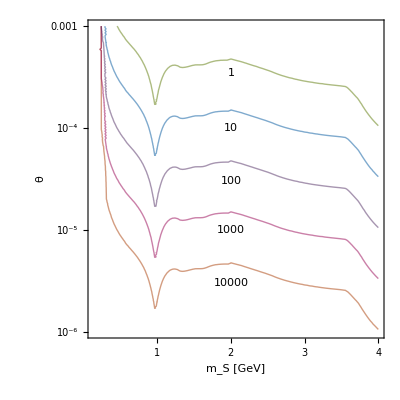

ctau.png

```mathematica
labelsαpos=Log@Reverse[{3 10^-6,10^-5,3 10^-5,10^-4, 3.5 10^-4}];
PlotContoursInvLabeled[cτS,0,0.14,4,10^-6,0.001,1,10^4,{1,10,100,1000,10000},{2,2,2,2,2},labelsαpos]
Export["ctau.png",%]
```

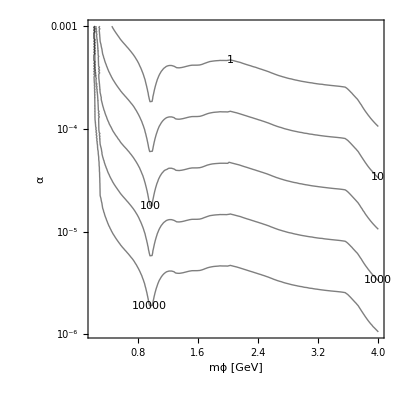

ctau.png

```mathematica
ContourPlot[cτS[m,α],{m,0.2,4},{α, 10^-6,0.001},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourStyle->{Black},Contours->{1,10,100,1000,10000},ContourLabels->All,PlotRange->All,PlotRange->All,ContourShading->False]
Export["ctau.png",%]
```

### Br’s

```mathematica
BrsPlot[α_]:=Plot[{BrBtoSKP[mS,α],BrBtoSKS700[mS,α],BrBtoSKS1430[mS,α],BrBtoSKV892[mS,α],BrBtoSKV1410[mS,α],BrBtoSKV1680[mS,α],BrBtoSKA1270[mS,α],BrBtoSKA1400[mS,α]},{mS,0,mB/.masses},PlotLegends->{P490,S700,S1430,V892,V1410,V1680,A1270,A1400}]
```

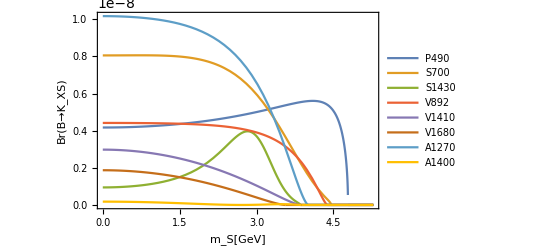

B-K_BR.png

```mathematica
Show[BrsPlot[0.0001],Frame-> True,FrameLabel->{"m_S[GeV]","Br(B→K_XS)"},AxesStyle->Directive[Black, 14],LabelStyle->Directive[Black,16],ImageSize-> 400]
Export["B-K_BR.png",%];
```

```mathematica
BrsLogPlot[α_]:=LogPlot[{BrBtoSKP[mS,α]/α^2,BrBtoSKS700[mS,α]/α^2+BrBtoSKS1430[mS,α]/α^2,BrBtoSKV892[mS,α]/α^2+BrBtoSKV1410[mS,α]/α^2+BrBtoSKV1680[mS,α]/α^2,BrBtoSKA1270[mS,α]/α^2+BrBtoSKA1400[mS,α]/α^2},{mS,0,mB/.masses},PlotLegends->{P490,"S700+S1430","V892+V1410+V1680","A1270+A1400"},PlotRange->{0.01,6},AxesLabel->{"m_S [GeV]", "Br/α^2"},GridLines->{{1,2,3,4,5},{0.01,0.05,0.1,0.5,1,8}}]
```

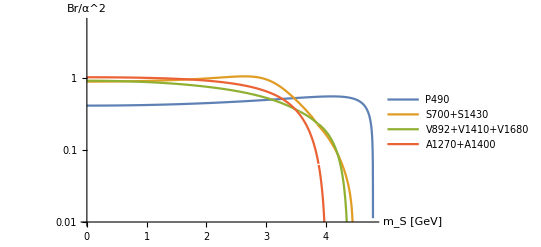

```mathematica
BrsLogPlot[0.0001]
```

### Auxiliary

```mathematica
mSlist=Range[2mμ/.masses,mB-mK/.masses,0.01]
mSlistπ=Range[2mπ+0.01/.masses,2,0.01]
mSlistK=Range[2mK+0.01/.masses,2,0.01]
mSlistτ=Range[2mτ/.masses,mB-mK/.masses,0.01]
```

{0.212,0.222,0.232,0.242,0.252,0.262,0.272,0.282,0.292,0.302,0.312,0.322,0.332,0.342,0.352,0.362,0.372,0.382,0.392,0.402,0.412,0.422,0.432,0.442,0.452,0.462,0.472,0.482,0.492,0.502,0.512,0.522,0.532,0.542,0.552,0.562,0.572,0.582,0.592,0.602,0.612,0.622,0.632,0.642,0.652,0.662,0.672,0.682,0.692,0.702,0.712,0.722,0.732,0.742,0.752,0.762,0.772,0.782,0.792,0.802,0.812,0.822,0.832,0.842,0.852,0.862,0.872,0.882,0.892,0.902,0.912,0.922,0.932,0.942,0.952,0.962,0.972,0.982,0.992,1.002,1.012,1.022,1.032,1.042,1.052,1.062,1.072,1.082,1.092,1.102,1.112,1.122,1.132,1.142,1.152,1.162,1.172,1.182,1.192,1.202,1.212,1.222,1.232,1.242,1.252,1.262,1.272,1.282,1.292,1.302,1.312,1.322,1.332,1.342,1.352,1.362,1.372,1.382,1.392,1.402,1.412,1.422,1.432,1.442,1.452,1.462,1.472,1.482,1.492,1.502,1.512,1.522,1.532,1.542,1.552,1.562,1.572,1.582,1.592,1.602,1.612,1.622,1.632,1.642,1.652,1.662,1.672,1.682,1.692,1.702,1.712,1.722,1.732,1.742,1.752,1.762,1.772,1.782,1.792,1.802,1.812,1.822,1.832,1.842,1.852,1.862,1.872,1.882,1.892,1.902,1.912,1.922,1.932,1.942,1.952,1.962,1.972,1.982,1.992,2.002,2.012,2.022,2.032,2.042,2.052,2.062,2.072,2.082,2.092,2.102,2.112,2.122,2.132,2.142,2.152,2.162,2.172,2.182,2.192,2.202,2.212,2.222,2.232,2.242,2.252,2.262,2.272,2.282,2.292,2.302,2.312,2.322,2.332,2.342,2.352,2.362,2.372,2.382,2.392,2.402,2.412,2.422,2.432,2.442,2.452,2.462,2.472,2.482,2.492,2.502,2.512,2.522,2.532,2.542,2.552,2.562,2.572,2.582,2.592,2.602,2.612,2.622,2.632,2.642,2.652,2.662,2.672,2.682,2.692,2.702,2.712,2.722,2.732,2.742,2.752,2.762,2.772,2.782,2.792,2.802,2.812,2.822,2.832,2.842,2.852,2.862,2.872,2.882,2.892,2.902,2.912,2.922,2.932,2.942,2.952,2.962,2.972,2.982,2.992,3.002,3.012,3.022,3.032,3.042,3.052,3.062,3.072,3.082,3.092,3.102,3.112,3.122,3.132,3.142,3.152,3.162,3.172,3.182,3.192,3.202,3.212,3.222,3.232,3.242,3.252,3.262,3.272,3.282,3.292,3.302,3.312,3.322,3.332,3.342,3.352,3.362,3.372,3.382,3.392,3.402,3.412,3.422,3.432,3.442,3.452,3.462,3.472,3.482,3.492,3.502,3.512,3.522,3.532,3.542,3.552,3.562,3.572,3.582,3.592,3.602,3.612,3.622,3.632,3.642,3.652,3.662,3.672,3.682,3.692,3.702,3.712,3.722,3.732,3.742,3.752,3.762,3.772,3.782,3.792,3.802,3.812,3.822,3.832,3.842,3.852,3.862,3.872,3.882,3.892,3.902,3.912,3.922,3.932,3.942,3.952,3.962,3.972,3.982,3.992,4.002,4.012,4.022,4.032,4.042,4.052,4.062,4.072,4.082,4.092,4.102,4.112,4.122,4.132,4.142,4.152,4.162,4.172,4.182,4.192,4.202,4.212,4.222,4.232,4.242,4.252,4.262,4.272,4.282,4.292,4.302,4.312,4.322,4.332,4.342,4.352,4.362,4.372,4.382,4.392,4.402,4.412,4.422,4.432,4.442,4.452,4.462,4.472,4.482,4.492,4.502,4.512,4.522,4.532,4.542,4.552,4.562,4.572,4.582,4.592,4.602,4.612,4.622,4.632,4.642,4.652,4.662,4.672,4.682,4.692,4.702,4.712,4.722,4.732,4.742,4.752,4.762,4.772,4.782}

{0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.,1.01,1.02,1.03,1.04,1.05,1.06,1.07,1.08,1.09,1.1,1.11,1.12,1.13,1.14,1.15,1.16,1.17,1.18,1.19,1.2,1.21,1.22,1.23,1.24,1.25,1.26,1.27,1.28,1.29,1.3,1.31,1.32,1.33,1.34,1.35,1.36,1.37,1.38,1.39,1.4,1.41,1.42,1.43,1.44,1.45,1.46,1.47,1.48,1.49,1.5,1.51,1.52,1.53,1.54,1.55,1.56,1.57,1.58,1.59,1.6,1.61,1.62,1.63,1.64,1.65,1.66,1.67,1.68,1.69,1.7,1.71,1.72,1.73,1.74,1.75,1.76,1.77,1.78,1.79,1.8,1.81,1.82,1.83,1.84,1.85,1.86,1.87,1.88,1.89,1.9,1.91,1.92,1.93,1.94,1.95,1.96,1.97,1.98,1.99,2.}

{0.9974,1.0074,1.0174,1.0274,1.0374,1.0474,1.0574,1.0674,1.0774,1.0874,1.0974,1.1074,1.1174,1.1274,1.1374,1.1474,1.1574,1.1674,1.1774,1.1874,1.1974,1.2074,1.2174,1.2274,1.2374,1.2474,1.2574,1.2674,1.2774,1.2874,1.2974,1.3074,1.3174,1.3274,1.3374,1.3474,1.3574,1.3674,1.3774,1.3874,1.3974,1.4074,1.4174,1.4274,1.4374,1.4474,1.4574,1.4674,1.4774,1.4874,1.4974,1.5074,1.5174,1.5274,1.5374,1.5474,1.5574,1.5674,1.5774,1.5874,1.5974,1.6074,1.6174,1.6274,1.6374,1.6474,1.6574,1.6674,1.6774,1.6874,1.6974,1.7074,1.7174,1.7274,1.7374,1.7474,1.7574,1.7674,1.7774,1.7874,1.7974,1.8074,1.8174,1.8274,1.8374,1.8474,1.8574,1.8674,1.8774,1.8874,1.8974,1.9074,1.9174,1.9274,1.9374,1.9474,1.9574,1.9674,1.9774,1.9874,1.9974}

{3.554,3.564,3.574,3.584,3.594,3.604,3.614,3.624,3.634,3.644,3.654,3.664,3.674,3.684,3.694,3.704,3.714,3.724,3.734,3.744,3.754,3.764,3.774,3.784,3.794,3.804,3.814,3.824,3.834,3.844,3.854,3.864,3.874,3.884,3.894,3.904,3.914,3.924,3.934,3.944,3.954,3.964,3.974,3.984,3.994,4.004,4.014,4.024,4.034,4.044,4.054,4.064,4.074,4.084,4.094,4.104,4.114,4.124,4.134,4.144,4.154,4.164,4.174,4.184,4.194,4.204,4.214,4.224,4.234,4.244,4.254,4.264,4.274,4.284,4.294,4.304,4.314,4.324,4.334,4.344,4.354,4.364,4.374,4.384,4.394,4.404,4.414,4.424,4.434,4.444,4.454,4.464,4.474,4.484,4.494,4.504,4.514,4.524,4.534,4.544,4.554,4.564,4.574,4.584,4.594,4.604,4.614,4.624,4.634,4.644,4.654,4.664,4.674,4.684,4.694,4.704,4.714,4.724,4.734,4.744,4.754,4.764,4.774,4.784}

### geoInt

```mathematica
intECLpoints=ParallelTable[NintECL[mS,0.0001,mK],{mS,mSlist}]//Quiet
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

{7.02624×10^-7,0.000289578,0.000809575,0.00147336,0.0022498,0.0031213,0.00407639,0.0135372,0.0258813,0.0358792,0.0456524,0.0553799,0.0647711,0.0760213,0.086797,0.0988955,0.110559,0.123964,0.137169,0.151988,0.167792,0.183535,0.198117,0.215203,0.232784,0.24955,0.268036,0.284772,0.30392,0.322283,0.338818,0.358523,0.378734,0.396437,0.413468,0.439932,0.457887,0.476763,0.496995,0.514593,0.532262,0.55156,0.570048,0.586755,0.606292,0.623737,0.640932,0.658928,0.677116,0.695084,0.71315,0.731147,0.747249,0.764087,0.780798,0.797817,0.813315,0.827994,0.842272,0.855078,0.867457,0.878904,0.888624,0.897094,0.904318,0.910067,0.914348,0.917306,0.919453,0.920513,0.920897,0.920827,0.920483,0.919919,0.919162,0.918185,0.917003,0.916885,0.918038,0.919208,0.919834,0.920333,0.920734,0.921004,0.921139,0.921128,0.920956,0.920624,0.920147,0.919624,0.918989,0.918324,0.917634,0.917006,0.916344,0.915803,0.91536,0.914991,0.914805,0.914704,0.914733,0.914893,0.915182,0.91547,0.915887,0.91634,0.917025,0.917538,0.91825,0.919053,0.91932,0.919635,0.919853,0.919994,0.920128,0.920232,0.920295,0.920354,0.920401,0.920442,0.920484,0.920497,0.920513,0.920548,0.920546,0.920565,0.920575,0.920593,0.920622,0.92065,0.920709,0.92079,0.920882,0.920986,0.921098,0.921207,0.921309,0.921402,0.921482,0.921563,0.921628,0.921688,0.921725,0.921738,0.921761,0.921762,0.921749,0.921715,0.921697,0.921681,0.921647,0.921622,0.921621,0.92163,0.921641,0.921658,0.921672,0.921696,0.92174,0.921806,0.921873,0.921924,0.921983,0.922048,0.922115,0.922188,0.922268,0.922334,0.922405,0.922482,0.922565,0.922635,0.922708,0.922782,0.92286,0.922934,0.923004,0.923076,0.92315,0.922872,0.92301,0.923137,0.923252,0.923358,0.923453,0.92354,0.923619,0.923691,0.923755,0.923814,0.923866,0.923913,0.923955,0.923993,0.924026,0.924054,0.924077,0.924096,0.92411,0.924121,0.924129,0.924134,0.924135,0.924134,0.924131,0.924126,0.924118,0.924108,0.924097,0.924084,0.924069,0.924053,0.924035,0.924015,0.923995,0.923972,0.923949,0.923924,0.923897,0.923869,0.92384,0.923809,0.923777,0.923743,0.923708,0.923671,0.923632,0.923592,0.923549,0.923505,0.923459,0.92341,0.923358,0.923304,0.923245,0.923181,0.923111,0.923041,0.92297,0.922898,0.922825,0.922752,0.922678,0.922603,0.922527,0.92245,0.922372,0.922294,0.922214,0.922134,0.922053,0.92197,0.921887,0.921802,0.921717,0.92163,0.921542,0.921454,0.921363,0.921272,0.92118,0.921086,0.920991,0.920894,0.920796,0.920697,0.920597,0.920494,0.920391,0.920285,0.920179,0.92007,0.91996,0.919848,0.919734,0.919619,0.919502,0.919382,0.919261,0.919138,0.919013,0.918885,0.918756,0.918624,0.91849,0.918353,0.918214,0.918073,0.917929,0.917783,0.917633,0.917481,0.917327,0.917169,0.917008,0.916845,0.916678,0.916508,0.916334,0.916157,0.915977,0.915793,0.915605,0.915414,0.915218,0.915019,0.914815,0.914608,0.914395,0.914179,0.913957,0.913731,0.9135,0.913264,0.913023,0.912776,0.912524,0.912267,0.912003,0.911733,0.911458,0.911176,0.910887,0.910591,0.910289,0.909979,0.909662,0.909333,0.908977,0.908612,0.908239,0.907856,0.907464,0.907061,0.906649,0.906096,0.905351,0.904488,0.903527,0.902479,0.901349,0.900144,0.898866,0.897518,0.896101,0.894618,0.893069,0.891455,0.889777,0.888035,0.886229,0.884334,0.882023,0.879423,0.876599,0.873579,0.87038,0.867014,0.86349,0.859818,0.856003,0.852054,0.847976,0.843778,0.839467,0.835051,0.830542,0.825952,0.821293,0.81658,0.811826,0.807037,0.802211,0.797353,0.792468,0.787557,0.782619,0.777652,0.772656,0.767628,0.762568,0.757476,0.752352,0.747193,0.742002,0.736777,0.731518,0.726225,0.720898,0.715536,0.71014,0.704708,0.69924,0.693735,0.688192,0.682611,0.676991,0.671329,0.665624,0.659876,0.654081,0.648239,0.642345,0.636399,0.630397,0.624335,0.618211,0.61202,0.605757,0.599418,0.592998,0.58649,0.579887,0.573182,0.566367,0.559432,0.552367,0.54516,0.537797,0.530264,0.522543,0.514615,0.506458,0.498047,0.489352,0.480339,0.470968,0.461194,0.450961,0.440203,0.428842,0.41678,0.4039,0.390052,0.375047,0.358637,0.340494,0.32016,0.296975,0.269925,0.237299,0.195741,0.136297,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
intCDCpoints=ParallelTable[NintCDC[mS,0.0001,mK],{mS,mSlist}]//Quiet
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

{5.10612×10^-7,0.000210452,0.000588402,0.00107096,0.00163552,0.00226937,0.00296425,0.00985869,0.0188851,0.0262217,0.0334166,0.0406009,0.0475583,0.0559209,0.0639625,0.0730254,0.0817982,0.0919255,0.10195,0.113256,0.125381,0.137531,0.148855,0.162203,0.176032,0.189304,0.20406,0.217516,0.233036,0.248051,0.261681,0.278067,0.295038,0.31005,0.324634,0.34756,0.363352,0.380097,0.398268,0.414275,0.430537,0.448528,0.466019,0.482042,0.501056,0.518311,0.535593,0.55416,0.573107,0.592209,0.611834,0.631835,0.650164,0.669833,0.68991,0.711021,0.730683,0.750267,0.770209,0.788802,0.807681,0.826156,0.842868,0.858482,0.872926,0.885708,0.895855,0.904163,0.911315,0.91588,0.918623,0.919918,0.92019,0.919856,0.919153,0.918184,0.917003,0.916885,0.918038,0.9192,0.919796,0.920203,0.920367,0.920186,0.919603,0.918561,0.917092,0.915237,0.913093,0.911029,0.908758,0.906546,0.904379,0.902492,0.900575,0.899052,0.897822,0.896819,0.896298,0.89601,0.896057,0.896448,0.897177,0.897919,0.899011,0.900219,0.902111,0.90356,0.905647,0.908137,0.90897,0.90999,0.910696,0.911143,0.911571,0.911892,0.912066,0.912225,0.912342,0.912433,0.912529,0.912514,0.912513,0.91258,0.912509,0.912519,0.91249,0.912495,0.912538,0.912579,0.912727,0.912966,0.913246,0.913577,0.913943,0.914302,0.914641,0.914945,0.915199,0.91546,0.915657,0.915832,0.915905,0.915875,0.915886,0.9158,0.915658,0.91543,0.915273,0.915123,0.914904,0.914719,0.914634,0.914589,0.914553,0.91454,0.914514,0.914529,0.914619,0.914795,0.914975,0.915095,0.915245,0.915423,0.915606,0.915813,0.916054,0.916236,0.91644,0.916677,0.916939,0.91715,0.917372,0.917606,0.917862,0.918099,0.918325,0.918566,0.918816,0.917376,0.917896,0.918383,0.918837,0.919259,0.919653,0.920019,0.920361,0.920677,0.920971,0.921244,0.921496,0.92173,0.921946,0.922151,0.922359,0.922549,0.92272,0.922874,0.923012,0.923137,0.923247,0.923345,0.923432,0.923508,0.923574,0.923632,0.923681,0.923722,0.923756,0.923784,0.923806,0.923822,0.923833,0.92384,0.923842,0.923839,0.923834,0.923824,0.923812,0.923796,0.923777,0.923756,0.923731,0.923704,0.923675,0.923643,0.923609,0.923572,0.923533,0.923492,0.923447,0.923401,0.923351,0.923298,0.92324,0.923177,0.923108,0.923038,0.922968,0.922896,0.922824,0.922751,0.922677,0.922602,0.922526,0.92245,0.922372,0.922294,0.922214,0.922134,0.922052,0.92197,0.921887,0.921802,0.921717,0.92163,0.921542,0.921454,0.921363,0.921272,0.92118,0.921086,0.920991,0.920894,0.920796,0.920697,0.920597,0.920494,0.920391,0.920285,0.920179,0.92007,0.91996,0.919848,0.919734,0.919619,0.919502,0.919382,0.919261,0.919138,0.919013,0.918885,0.918756,0.918624,0.91849,0.918353,0.918214,0.918073,0.917929,0.917783,0.917633,0.917481,0.917327,0.917169,0.917008,0.916845,0.916678,0.916508,0.916334,0.916157,0.915977,0.915793,0.915605,0.915414,0.915218,0.915019,0.914815,0.914608,0.914395,0.914179,0.913957,0.913731,0.9135,0.913264,0.913023,0.912776,0.912524,0.912267,0.912003,0.911733,0.911458,0.911176,0.910887,0.910591,0.910289,0.909979,0.909662,0.909333,0.908977,0.908612,0.908239,0.907856,0.907464,0.907061,0.906649,0.906096,0.905351,0.904488,0.903527,0.902479,0.901349,0.900144,0.898866,0.897518,0.896101,0.894618,0.893069,0.891455,0.889777,0.888035,0.886229,0.884334,0.882023,0.879423,0.876599,0.873579,0.87038,0.867014,0.86349,0.859818,0.856003,0.852054,0.847976,0.843778,0.839467,0.835051,0.830542,0.825952,0.821293,0.81658,0.811826,0.807037,0.802211,0.797353,0.792468,0.787557,0.782619,0.777652,0.772656,0.767628,0.762568,0.757476,0.752352,0.747193,0.742002,0.736777,0.731518,0.726225,0.720898,0.715536,0.71014,0.704708,0.69924,0.693735,0.688192,0.682611,0.676991,0.671329,0.665624,0.659876,0.654081,0.648239,0.642345,0.636399,0.630397,0.624335,0.618211,0.61202,0.605757,0.599418,0.592998,0.58649,0.579887,0.573182,0.566367,0.559432,0.552367,0.54516,0.537797,0.530264,0.522543,0.514615,0.506458,0.498047,0.489352,0.480339,0.470968,0.461194,0.450961,0.440203,0.428842,0.41678,0.4039,0.390052,0.375047,0.358637,0.340494,0.32016,0.296975,0.269925,0.237299,0.195741,0.136297,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

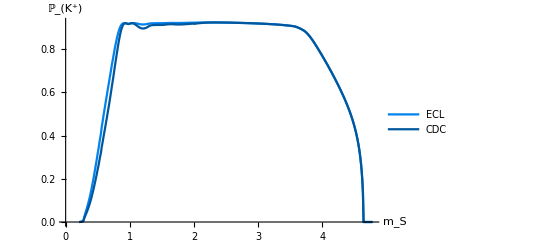

```mathematica
Show[ListPlot[Thread[{mSlist,intECLpoints}], Joined->True,PlotStyle->myColours[[1]],PlotLegends->{ECL}],ListPlot[Thread[{mSlist,intCDCpoints}], Joined->True,PlotStyle->myColours[[2]],PlotLegends->{CDC}],AxesLabel->{Subscript[m, S],Subscript[ℙ, SuperPlus[K]]},AxesStyle->Directive[Black,14],LabelStyle->Directive[Black,16]]
```

### mS-NXX

```mathematica
NmmECLKpoints=ParallelTable[NμμECLK[mS,0.0001],{mS,mSlist}];
```

InterpolatingFunction::dmval: Input value {0.892} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.722} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.212} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.382} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.552} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.732} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.212} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.742} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.222} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.392} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.562} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.572} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.402} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.072} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.232} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.392} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.072} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.232} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.392} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.082} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.242} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.402} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.002} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.012} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.552} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.562} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.712} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.872} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.712} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.872} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.722} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.882} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.032} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.042} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.192} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.202} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.352} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.512} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.362} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.512} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.522} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.672} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.682} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.832} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.992} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.842} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.992} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.002} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.152} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.152} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.312} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.162} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.312} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.322} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.472} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.482} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.632} lies outside the range of data in the interpolating function. Extrapolation will be used.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.642} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
NmmCDCKpoints=ParallelTable[NμμCDCK[mS,0.0001],{mS,mSlist}];
```

InterpolatingFunction::dmval: Input value {0.892} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.722} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.552} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.382} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.212} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.732} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.562} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.392} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.222} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.572} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.742} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.402} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.232} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.072} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.232} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.072} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.242} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.082} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.002} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.012} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.392} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.402} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.552} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.712} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.552} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.712} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.562} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.722} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.872} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.882} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.032} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.192} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.352} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.042} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.192} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.352} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.202} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.362} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.512} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.522} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.672} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.682} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.832} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.992} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.152} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.832} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.992} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.152} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.842} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.002} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.162} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.312} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.322} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.472} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.472} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.482} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.632} lies outside the range of data in the interpolating function. Extrapolation will be used.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.642} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

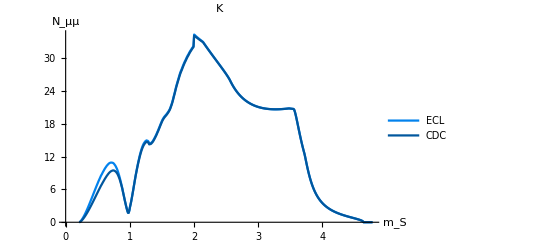

```mathematica
Show[ListPlot[Thread[{mSlist,NmmECLKpoints}], Joined->True,PlotStyle->myColours[[1]],PlotLegends->{ECL}],ListPlot[Thread[{mSlist,NmmCDCKpoints}], Joined->True,PlotStyle->myColours[[2]],PlotLegends->{CDC}],AxesLabel->{Subscript[m, S],Subscript[N, μμ]},AxesStyle->Directive[Black,14],LabelStyle->Directive[Black,14],PlotLabel->"K"]
```

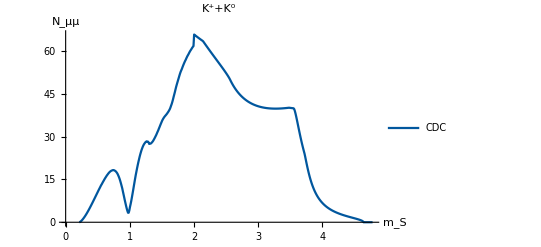

```mathematica
Show[ListPlot[Thread[{mSlist,1.93*NmmCDCKpoints}], Joined->True,PlotStyle->myColours[[2]],PlotLegends->{CDC}],AxesLabel->{Subscript[m, S],Subscript[N, μμ]},AxesStyle->Directive[Black,14],LabelStyle->Directive[Black,14],PlotLabel->"K^++K^0"]
```

```mathematica
NmmECLKV892points=ParallelTable[NμμECLKV892[mS,0.0001],{mS,mSlist}];
```

InterpolatingFunction::dmval: Input value {0.892} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.722} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.382} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.552} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.732} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.212} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.742} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.222} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.392} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.562} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.572} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.402} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.072} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.082} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.232} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.392} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.232} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.392} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.242} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.402} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.002} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.002} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.012} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.552} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.562} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.712} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.872} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.032} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.712} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.872} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.032} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.722} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.882} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.042} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.192} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.202} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.352} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.512} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.672} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.362} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.512} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.672} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.522} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.682} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.832} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.842} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.992} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.002} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.152} lies outside the range of data in the interpolating function. Extrapolation will be used.

Power::infy: Infinite expression 1/0 encountered.

InterpolatingFunction::dmval: Input value {4.152} lies outside the range of data in the interpolating function. Extrapolation will be used.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

InterpolatingFunction::dmval: Input value {4.162} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

InterpolatingFunction::dmval: Input value {4.312} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

InterpolatingFunction::dmval: Input value {4.312} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.472} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Power::infy: Infinite expression 1/0 encountered.

InterpolatingFunction::dmval: Input value {4.322} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.472} lies outside the range of data in the interpolating function. Extrapolation will be used.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.482} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.632} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

InterpolatingFunction::dmval: Input value {4.632} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.642} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
NmmCDCKV892points=ParallelTable[NμμCDCKV892[mS,0.0001],{mS,mSlist}];
```

InterpolatingFunction::dmval: Input value {0.892} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.722} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.552} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.382} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.212} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.732} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.562} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.222} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.392} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.572} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.742} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.402} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.072} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.232} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.072} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.232} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.082} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.242} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.002} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.012} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.392} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.402} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.552} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.712} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.552} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.712} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.562} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.722} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.872} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.882} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.032} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.042} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.192} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.352} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.192} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.352} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.202} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.362} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.512} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.522} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.672} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.832} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.682} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.832} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.842} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.992} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.152} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.992} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.152} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.002} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.162} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

Power::infy: Infinite expression 1/0 encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

InterpolatingFunction::dmval: Input value {4.312} lies outside the range of data in the interpolating function. Extrapolation will be used.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

InterpolatingFunction::dmval: Input value {4.312} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

InterpolatingFunction::dmval: Input value {4.322} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

Power::infy: Infinite expression 1/0 encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

InterpolatingFunction::dmval: Input value {4.472} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

General::stop: Further output of Power::infy will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.472} lies outside the range of data in the interpolating function. Extrapolation will be used.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

InterpolatingFunction::dmval: Input value {4.482} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

InterpolatingFunction::dmval: Input value {4.632} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.632} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.642} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

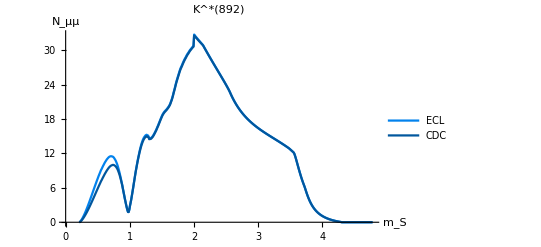

```mathematica
Show[ListPlot[Thread[{mSlist,NmmECLKV892points}], Joined->True,PlotStyle->myColours[[1]],PlotLegends->{ECL}],ListPlot[Thread[{mSlist,NmmCDCKV892points}], Joined->True,PlotStyle->myColours[[2]],PlotLegends->{CDC}],AxesLabel->{Subscript[m, S],Subscript[N, μμ]},AxesStyle->Directive[Black,14],LabelStyle->Directive[Black,14],PlotLabel->"K^*(892)"]
```

```mathematica
NmmECLpoints=ParallelTable[NμμECL[mS,0.0001],{mS,mSlist}];
```

InterpolatingFunction::dmval: Input value {0.892} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.722} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.382} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.552} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.212} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.722} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.212} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.722} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.382} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.552} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.212} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.382} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.552} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.072} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.232} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.392} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.232} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.392} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.232} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.392} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.002} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.552} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.712} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.872} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.032} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.872} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.032} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.872} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.032} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.192} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.352} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.512} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.672} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.832} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.992} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.152} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.312} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.312} lies outside the range of data in the interpolating function. Extrapolation will be used.

Power::infy: Infinite expression 1/0 encountered.

InterpolatingFunction::dmval: Input value {4.472} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.312} lies outside the range of data in the interpolating function. Extrapolation will be used.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

InterpolatingFunction::dmval: Input value {4.472} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.472} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.632} lies outside the range of data in the interpolating function. Extrapolation will be used.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.632} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
NmmCDCpoints=ParallelTable[NμμCDC[mS,0.0001],{mS,mSlist}];
```

InterpolatingFunction::dmval: Input value {0.892} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.552} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.722} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.212} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.382} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.212} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.552} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.722} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.212} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.382} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.552} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.722} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.382} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.072} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.232} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.002} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.392} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.552} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.712} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.872} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.032} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.192} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.352} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.512} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.672} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.832} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.992} lies outside the range of data in the interpolating function. Extrapolation will be used.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

InterpolatingFunction::dmval: Input value {3.992} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.992} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.152} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

InterpolatingFunction::dmval: Input value {4.152} lies outside the range of data in the interpolating function. Extrapolation will be used.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

InterpolatingFunction::dmval: Input value {4.152} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.312} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.472} lies outside the range of data in the interpolating function. Extrapolation will be used.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.472} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.632} lies outside the range of data in the interpolating function. Extrapolation will be used.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,113}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.632} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

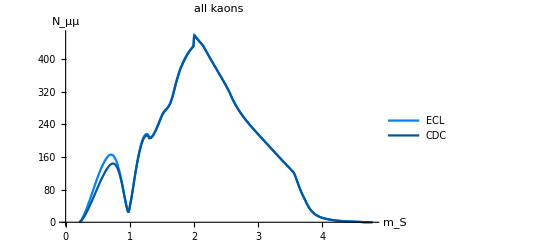

```mathematica
Show[ListPlot[Thread[{mSlist,NmmECLpoints}], Joined->True,PlotStyle->myColours[[1]],PlotLegends->{ECL}],ListPlot[Thread[{mSlist,NmmCDCpoints}], Joined->True,PlotStyle->myColours[[2]],PlotLegends->{CDC}],AxesLabel->{Subscript[m, S],Subscript[N, μμ]},AxesStyle->Directive[Black,14],LabelStyle->Directive[Black,14],PlotLabel->"all kaons"]
```

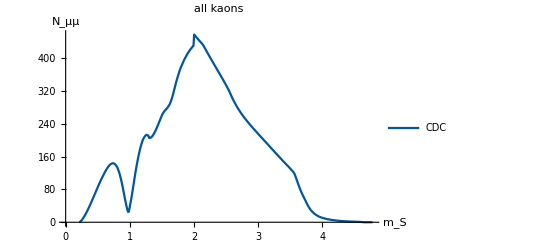

```mathematica
Show[ListPlot[Thread[{mSlist,NmmCDCpoints}], Joined->True,PlotStyle->myColours[[2]],PlotLegends->{CDC}],AxesLabel->{Subscript[m, S],Subscript[N, μμ]},AxesStyle->Directive[Black,14],LabelStyle->Directive[Black,14],PlotLabel->"all kaons"]
```

```mathematica
NppECLpoints=ParallelTable[NππECL[mS,0.0001]/.HeavisideTheta[0.]:>0,{mS,mSlistπ}];
```

InterpolatingFunction::dmval: Input value {0.81} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.73} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.65} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.38} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.47} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.56} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.73} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.29} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.65} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.73} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.29} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.38} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.47} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.56} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.65} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.29} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.38} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.47} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.56} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.89} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
NppCDCpoints=ParallelTable[NππCDC[mS,0.0001/.HeavisideTheta[0.]:>0],{mS,mSlistπ}];
```

InterpolatingFunction::dmval: Input value {0.81} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.73} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.65} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.29} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.38} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.47} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.56} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.73} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.65} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.73} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.29} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.38} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.47} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.56} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.65} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.29} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.38} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.47} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.56} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.89} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

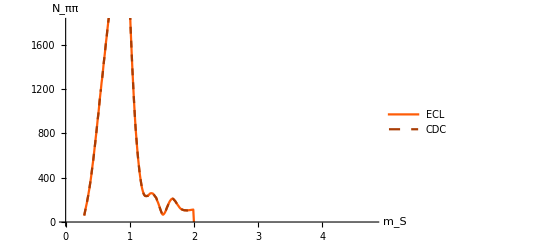

```mathematica
Show[ListPlot[Thread[{mSlistπ,NppECLpoints}], Joined->True,PlotStyle->myColours[[3]],PlotLegends->{ECL}],ListPlot[Thread[{mSlistπ,NppCDCpoints}], Joined->True,PlotStyle->Directive[myColours[[4]],Dashed],PlotLegends->{CDC},PlotRange->Full],AxesLabel->{Subscript[m, S],Subscript[N, ππ]},AxesStyle->Directive[Black,14],LabelStyle->Directive[Black,16],PlotRange->{{0,mB-mK/.masses},{0,1800}}]
```

```mathematica
NkkECLpoints=ParallelTable[NKKECL[mS,0.0001],{mS,mSlistK}];
```

InterpolatingFunction::dmval: Input value {1.9974} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
NkkCDCpoints=ParallelTable[NKKCDC[mS,0.0001],{mS,mSlistK}];
```

InterpolatingFunction::dmval: Input value {1.9974} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

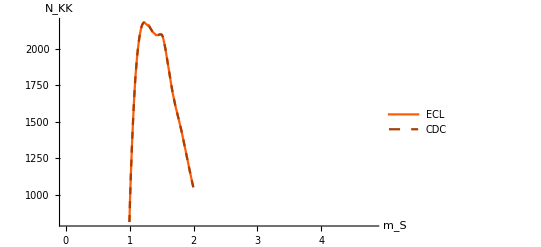

```mathematica
Show[ListPlot[Thread[{mSlistK,NkkECLpoints}], Joined->True,PlotStyle->myColours[[3]],PlotLegends->{ECL}],ListPlot[Thread[{mSlistK,NkkCDCpoints}], Joined->True,PlotStyle->Directive[myColours[[4]],Dashed],PlotLegends->{CDC}],AxesLabel->{Subscript[m, S],Subscript[N, KK]},AxesStyle->Directive[Black,14],LabelStyle->Directive[Black,16],PlotRange->{{0,4.8},Automatic}]
```

```mathematica
NttECLpoints=ParallelTable[NττECL[mS,0.0001],{mS,mSlistτ}];
```

InterpolatingFunction::dmval: Input value {3.554} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.614} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.674} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.734} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.794} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.854} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.914} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.554} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.614} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.674} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.734} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.794} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.854} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.914} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.554} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.614} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.674} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.734} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.794} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.854} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.914} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Select::normal: Nonatomic expression expected at position 1 in Select[θ,Head[#1]===Real&&#1>0&&#1<3.14159/2&].

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Select::normal: Nonatomic expression expected at position 1 in Select[θ,Head[#1]===Real&&#1>0.&&#1<3.14159 0.5&].

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Select::normal: Nonatomic expression expected at position 1 in Select[θ,Head[#1]===Real&&#1>0&&#1<3.14159/2&].

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Select::normal will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumr: The integrand NintdECL[θ0,3.854,0.0001,mKstarS1430] has evaluated to non-numerical values for all sampling points in the region with boundaries {{(-ⅈ) ∞,(0.+0. ⅈ)+If[Min[2.61799,Select[θ,«1»&]]==2.61799,Nθ0ofθ[150. 0.0174533,3.854,mKstarS1430]⟦2⟧,Nθ0ofθ[17. 0.0174533,3.854,mKstarS1430]⟦1⟧]}}.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

NIntegrate::inumr: The integrand NintdECL[θ0,3.854,0.0001,mKstarS1430] has evaluated to non-numerical values for all sampling points in the region with boundaries {{(-ⅈ) ∞,(0.+0. ⅈ)+If[Min[2.61799,Select[θ,«1»&]]==2.61799,Nθ0ofθ[150. 0.0174533,3.854,mKstarS1430]⟦2⟧,Nθ0ofθ[17. 0.0174533,3.854,mKstarS1430]⟦1⟧]}}.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.274} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.974} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.034} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.094} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.154} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.214} lies outside the range of data in the interpolating function. Extrapolation will be used.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

InterpolatingFunction::dmval: Input value {4.274} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.974} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.034} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.094} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.154} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.214} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.274} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.974} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.034} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.094} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.154} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.214} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

InterpolatingFunction::dmval: Input value {4.334} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

InterpolatingFunction::dmval: Input value {4.334} lies outside the range of data in the interpolating function. Extrapolation will be used.

Power::infy: Infinite expression 1/0 encountered.

InterpolatingFunction::dmval: Input value {4.334} lies outside the range of data in the interpolating function. Extrapolation will be used.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.394} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.454} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.514} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.574} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.634} lies outside the range of data in the interpolating function. Extrapolation will be used.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

InterpolatingFunction::dmval: Input value {4.394} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.454} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.514} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.574} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.634} lies outside the range of data in the interpolating function. Extrapolation will be used.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

InterpolatingFunction::dmval: Input value {4.694} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.694} lies outside the range of data in the interpolating function. Extrapolation will be used.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

InterpolatingFunction::dmval: Input value {4.394} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.454} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.514} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.574} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.634} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.694} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.744} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
NttCDCpoints=ParallelTable[NττCDC[mS,0.0001],{mS,mSlistτ}];
```

InterpolatingFunction::dmval: Input value {3.554} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.614} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.674} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.734} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.794} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.854} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.914} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.554} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.614} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.674} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.734} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.794} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.854} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.914} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.554} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.614} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.674} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.734} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.794} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.854} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.914} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Select::normal: Nonatomic expression expected at position 1 in Select[θ,Head[#1]===Real&&#1>0&&#1<3.14159/2&].

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Select::normal: Nonatomic expression expected at position 1 in Select[θ,Head[#1]===Real&&#1>0.&&#1<3.14159 0.5&].

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Select::normal: Nonatomic expression expected at position 1 in Select[θ,Head[#1]===Real&&#1>0&&#1<3.14159/2&].

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Select::normal will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumr: The integrand NintdCDC[θ0,3.854,0.0001,mKstarS1430] has evaluated to non-numerical values for all sampling points in the region with boundaries {{(-ⅈ) ∞,(0.+0. ⅈ)+If[Min[2.61799,Select[θ,«1»&]]==2.61799,Nθ0ofθ[150. 0.0174533,3.854,mKstarS1430]⟦2⟧,Nθ0ofθ[17. 0.0174533,3.854,mKstarS1430]⟦1⟧]}}.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

NIntegrate::inumr: The integrand NintdCDC[θ0,3.854,0.0001,mKstarS1430] has evaluated to non-numerical values for all sampling points in the region with boundaries {{(-ⅈ) ∞,(0.+0. ⅈ)+If[Min[2.61799,Select[θ,«1»&]]==2.61799,Nθ0ofθ[150. 0.0174533,3.854,mKstarS1430]⟦2⟧,Nθ0ofθ[17. 0.0174533,3.854,mKstarS1430]⟦1⟧]}}.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

InterpolatingFunction::dmval: Input value {3.974} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.034} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.094} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.154} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.214} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of Power::infy will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.274} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.974} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.034} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.094} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.154} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.214} lies outside the range of data in the interpolating function. Extrapolation will be used.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

InterpolatingFunction::dmval: Input value {4.274} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.974} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.034} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.094} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.154} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.214} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.274} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

InterpolatingFunction::dmval: Input value {4.334} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Power::infy: Infinite expression 1/0 encountered.

InterpolatingFunction::dmval: Input value {4.334} lies outside the range of data in the interpolating function. Extrapolation will be used.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

InterpolatingFunction::dmval: Input value {4.334} lies outside the range of data in the interpolating function. Extrapolation will be used.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

InterpolatingFunction::dmval: Input value {4.394} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.454} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.514} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.574} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.634} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

InterpolatingFunction::dmval: Input value {4.394} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.454} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.514} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.574} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.634} lies outside the range of data in the interpolating function. Extrapolation will be used.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Power::infy: Infinite expression 1/0 encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

Power::infy: Infinite expression 1/0 encountered.

InterpolatingFunction::dmval: Input value {4.694} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

General::stop: Further output of Power::infy will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.694} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.394} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.454} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.514} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.574} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.634} lies outside the range of data in the interpolating function. Extrapolation will be used.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

InterpolatingFunction::dmval: Input value {4.694} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,146}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.744} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

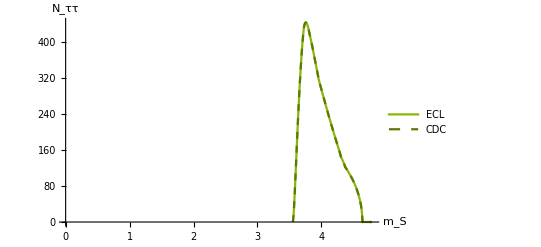

```mathematica
Show[ListPlot[Thread[{mSlistτ,NttECLpoints}], Joined->True,PlotStyle->myColours[[5]],PlotLegends->{ECL}],ListPlot[Thread[{mSlistτ,NttCDCpoints}], Joined->True,PlotStyle->Directive[myColours[[6]],Dashed],PlotLegends->{CDC}],AxesLabel->{Subscript[m, S],Subscript[N, ττ]},AxesStyle->Directive[Black,14],LabelStyle->Directive[Black,16],PlotRange->{{0,4.8},Automatic},AxesOrigin->{0,0}]
```

### Rasterised ContourPlots

#### defs

```mathematica
reMap[n_]:=If[n>0.,Log@n,-5];
```

```mathematica
evalRaster1[func_]:=Block[{n1=66,n2=132,n3=66,mSTemp1,αTemp1,mSTemp2,αTemp2,mSTemp3,αTemp3,alphaMin = -5,alphaMax=-1,dataPre1,dataPre2,dataPre3,data1,data2,data3,data},
mSTemp1 = Range[2.*mμ /. masses,mB-mK/.masses, (mB-mK -2.*mμ)/(n1-1) /.masses];
αTemp1 = 10.^Range[alphaMin,alphaMax, (alphaMax-alphaMin)/(n1-1) /.masses];

mSTemp2 = Range[0.8,1.2, (1.2-0.8)/(n2-1) /.masses];
αTemp2 = 10.^Range[alphaMin,alphaMax, (alphaMax-alphaMin)/(n2-1) /.masses];

mSTemp3 = Range[2.*mμ /. masses,1, (1-(2.*mμ))/(n3-1) /.masses];
αTemp3 =10.^Range[alphaMin,alphaMax, (alphaMax-alphaMin)/(n3-1) /.masses];

dataPre1=ParallelTable[{x=mSTemp1[[i]],y=αTemp1[[j]],func[x,y]/.HeavisideTheta[0]:>0/.HeavisideTheta[0.]:>0//Quiet},{i,1,n1},{j,1,n1}]; 
dataPre2=ParallelTable[{x=mSTemp2[[i]],y=αTemp2[[j]],func[x,y]/.HeavisideTheta[0]:>0/.HeavisideTheta[0.]:>0//Quiet},{i,1,n2},{j,1,n2}]; 
dataPre3=ParallelTable[{x=mSTemp3[[i]],y=αTemp3[[j]],func[x,y]/.HeavisideTheta[0]:>0/.HeavisideTheta[0.]:>0//Quiet},{i,1,n3},{j,1,n3}]; 

data1 = Flatten[dataPre1,1];
data2 = Flatten[dataPre2,1];
data3 = Flatten[dataPre3,1];

data=Join[data1,data2,data3];
Return[data];
]

evalRaster2[func_]:=Block[{n1=66,n2=132,n3=66,mSTemp1,αTemp1,mSTemp2,αTemp2,mSTemp3,αTemp3,alphaMin = -6,alphaMax=-1,dataPre1,dataPre2,dataPre3,data1,data2,data3,data},
mSTemp1 = Range[2.*mπ /. masses,2/.masses, (2-2.*mπ)/(n1-1) /.masses];
αTemp1 = 10.^Range[alphaMin,alphaMax, (alphaMax-alphaMin)/(n1-1) /.masses];

mSTemp2 = Range[0.8,1.2, (1.2-0.8)/(n2-1) /.masses];
αTemp2 = 10.^Range[alphaMin,alphaMax, (alphaMax-alphaMin)/(n2-1) /.masses];

mSTemp3 = Range[2.*mπ /. masses,1, (1-(2.*mπ))/(n3-1) /.masses];
αTemp3 =10.^Range[alphaMin,alphaMax, (alphaMax-alphaMin)/(n3-1) /.masses];

dataPre1=ParallelTable[{x=mSTemp1[[i]],y=αTemp1[[j]],func[x,y]/.HeavisideTheta[0]:>0/.HeavisideTheta[0.]:>0//Quiet},{i,1,n1},{j,1,n1}]; 
dataPre2=ParallelTable[{x=mSTemp2[[i]],y=αTemp2[[j]],func[x,y]/.HeavisideTheta[0]:>0/.HeavisideTheta[0.]:>0//Quiet},{i,1,n2},{j,1,n2}]; 
dataPre3=ParallelTable[{x=mSTemp3[[i]],y=αTemp3[[j]],func[x,y]/.HeavisideTheta[0]:>0/.HeavisideTheta[0.]:>0//Quiet},{i,1,n3},{j,1,n3}]; 

data1 = Flatten[dataPre1,1];
data2 = Flatten[dataPre2,1];
data3 = Flatten[dataPre3,1];

data=Join[data1,data2,data3];
Return[data];
]

evalRaster3[func_]:=Block[{n1=150,mSTemp1,αTemp1,alphaMin = -6,alphaMax=-1,dataPre1,data1,data},
mSTemp1 = Range[2.*mτ /. masses,mB-mK/.masses, (mB-mK -2.*mτ)/(n1-1) /.masses];
αTemp1 = 10.^Range[alphaMin,alphaMax, (alphaMax-alphaMin)/(n1-1) /.masses];
dataPre1=ParallelTable[{x=mSTemp1[[i]],y=αTemp1[[j]],func[x,y]/.HeavisideTheta[0]:>0/.HeavisideTheta[0.]:>0//Quiet},{i,1,n1},{j,1,n1}]; 
data1 = Flatten[dataPre1,1];
data=data1;
Return[data];
]
```

#### data

```mathematica
funcNamesμμ = {NμμCDCK,NμμCDCKS700,NμμCDCKS1430,NμμCDCKV892,NμμCDCKV1410,NμμCDCKV1680,NμμCDCKA1270,NμμCDCKA1400};
funcNamesπK = {NπKCDCK,NπKCDCKS700,NπKCDCKS1430,NπKCDCKV892,NπKCDCKV1410,NπKCDCKV1680,NπKCDCKA1270,NπKCDCKA1400};
funcNamesττ = {NττCDCK,NττCDCKS700,NττCDCKS1430,NττCDCKV892,NττCDCKV1410,NττCDCKV1680,NττCDCKA1270,NττCDCKA1400};
```

```mathematica
funcNamesμμE = {NμμECLK,NμμECLKS700,NμμECLKS1430,NμμECLKV892,NμμECLKV1410,NμμECLKV1680,NμμECLKA1270,NμμECLKA1400};
funcNamesπKE = {NπKECLK,NπKECLKS700,NπKECLKS1430,NπKECLKV892,NπKECLKV1410,NπKECLKV1680,NπKECLKA1270,NπKECLKA1400};
funcNamesττE= {NττECLK,NττECLKS700,NττECLKS1430,NττECLKV892,NττECLKV1410,NττECLKV1680,NττECLKA1270,NττECLKA1400};
```

```mathematica
dataArrayμμ = Table[evalRaster1[func],{func,funcNamesμμ}];
Export["dataArrayMuMu.m",dataArrayμμ];

dataArrayπK = Table[evalRaster2[func],{func,funcNamesπK}];
Export["dataArrayPiK.m",dataArrayπK];

dataArrayττ = Table[evalRaster3[func],{func,funcNamesττ}];
Export["dataArrayTauTau.m",dataArrayττ];
```

```mathematica
dataArrayμμ=Import["dataArrayMuMu.m"];
```

```mathematica
dataArrayπK=Import["dataArrayPiK.m"];
```

```mathematica
dataArrayπKp = ParallelTable[{dataArrayμμ[[i,j,1]],dataArrayμμ[[i,j,2]],dataArrayμμ[[i,j,3]]*(BrSKK[dataArrayμμ[[i,j,1]],dataArrayμμ[[i,j,2]]]+BrSππ[dataArrayμμ[[i,j,1]],dataArrayμμ[[i,j,2]]])/(BrSμμ[dataArrayμμ[[i,j,1]],dataArrayμμ[[i,j,2]]])},{i,1,Length[dataArrayμμ]},{j,1,Length@dataArrayμμ[[1]]}];
```

InterpolatingFunction::dmval: Input value {0.212} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
dataArrayττ=Import["dataArrayTauTau.m"];
```

```mathematica
dataArrayμμE=Import["dataArrayMuMuE.m"];
```

```mathematica
NotebookSave[];
```

```mathematica
dataArrayμμE = Table[evalRaster1[func],{func,funcNamesμμE}];
Export["dataArrayMuMuE.m",dataArrayμμE];
```

```mathematica
dataArrayπKE = Table[{dataArrayμμE[[i,j,1]],dataArrayμμE[[i,j,2]],dataArrayμμE[[i,j,3]]*(BrSKK[dataArrayμμE[[i,j,1]],dataArrayμμE[[i,j,2]]]+BrSππ[dataArrayμμE[[i,j,1]],dataArrayμμE[[i,j,2]]])/(BrSμμ[dataArrayμμE[[i,j,1]],dataArrayμμE[[i,j,2]]])},{i,1,Length[dataArrayμμE]},{j,1,Length@dataArrayμμE[[1]]}];
```

InterpolatingFunction::dmval: Input value {0.212} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
Export["dataArrayPiKE.m",dataArrayπKE];
```

```mathematica
dataArrayττE = Table[evalRaster3[func],{func,funcNamesττE}];
```

```mathematica
dataArrayττE = Table[{dataArrayμμE[[i,j,1]],dataArrayμμE[[i,j,2]],dataArrayμμE[[i,j,3]]*(BrSττ[dataArrayμμE[[i,j,1]],dataArrayμμE[[i,j,2]]])/(BrSμμ[dataArrayμμE[[i,j,1]],dataArrayμμE[[i,j,2]]])},{i,1,Length[dataArrayμμE]},{j,1,Length@dataArrayμμE[[1]]}];
```

InterpolatingFunction::dmval: Input value {0.212} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
Export["dataArrayTauTauE.m",dataArrayττE];
```

```mathematica
totalArrayμμ=Table[{dataArrayμμ[[1,i,1]],dataArrayμμ[[1,i,2]],1.93*Sum[dataArrayμμ[[j,i,3]],{j,1,Length@funcNamesμμ}]},{i,1,Length@dataArrayμμ[[1]]}];
totalArrayπK=Table[{dataArrayπK[[1,i,1]],dataArrayπK[[1,i,2]],1.93*Sum[dataArrayπK[[j,i,3]],{j,1,Length@funcNamesπK}]},{i,1,Length@dataArrayπK[[1]]}];
totalArrayττ=Table[{dataArrayττ[[1,i,1]],dataArrayττ[[1,i,2]],1.93*Sum[dataArrayττ[[j,i,3]],{j,1,Length@funcNamesττ}]},{i,1,Length@dataArrayττ[[1]]}];
```

```mathematica
totalArrayμμE=Table[{dataArrayμμE[[1,i,1]],dataArrayμμE[[1,i,2]],1.93*Sum[dataArrayμμE[[j,i,3]],{j,1,Length@funcNamesμμ}]},{i,1,Length@dataArrayμμ[[1]]}];
```

```mathematica
totalArrayπKE=Table[{dataArrayπKE[[1,i,1]],dataArrayπKE[[1,i,2]],1.93*Sum[dataArrayπKE[[j,i,3]],{j,1,Length@funcNamesπK}]},{i,1,Length@dataArrayπK[[1]]}];
totalArrayττE=Table[{dataArrayττE[[1,i,1]],dataArrayττE[[1,i,2]],1.93*Sum[dataArrayττE[[j,i,3]],{j,1,Length@funcNamesττ}]},{i,1,Length@dataArrayττ[[1]]}];
```

```mathematica
dAμKs=Table[{dataArrayμμ[[1,i,1]],dataArrayμμ[[1,i,2]],1.93*dataArrayμμ[[1,i,3]]},{i,1,Length@dataArrayμμ[[1]]}];
dAμKVs=Table[{dataArrayμμ[[4,i,1]],dataArrayμμ[[4,i,2]],1.93*dataArrayμμ[[4,i,3]]},{i,1,Length@dataArrayμμ[[1]]}];
dAπKs=Table[{dataArrayπK[[1,i,1]],dataArrayπK[[1,i,2]],1.93*dataArrayπK[[1,i,3]]},{i,1,Length@dataArrayπK[[1]]}];
dAπKVs=Table[{dataArrayπK[[4,i,1]],dataArrayπK[[4,i,2]],1.93*dataArrayπK[[4,i,3]]},{i,1,Length@dataArrayπK[[1]]}];
dAτKs=Table[{dataArrayττ[[1,i,1]],dataArrayττ[[1,i,2]],1.93*dataArrayττ[[1,i,3]]},{i,1,Length@dataArrayττ[[1]]}];
dAτKVs=Table[{dataArrayττ[[4,i,1]],dataArrayττ[[4,i,2]],1.93*dataArrayττ[[4,i,3]]},{i,1,Length@dataArrayττ[[1]]}];
```

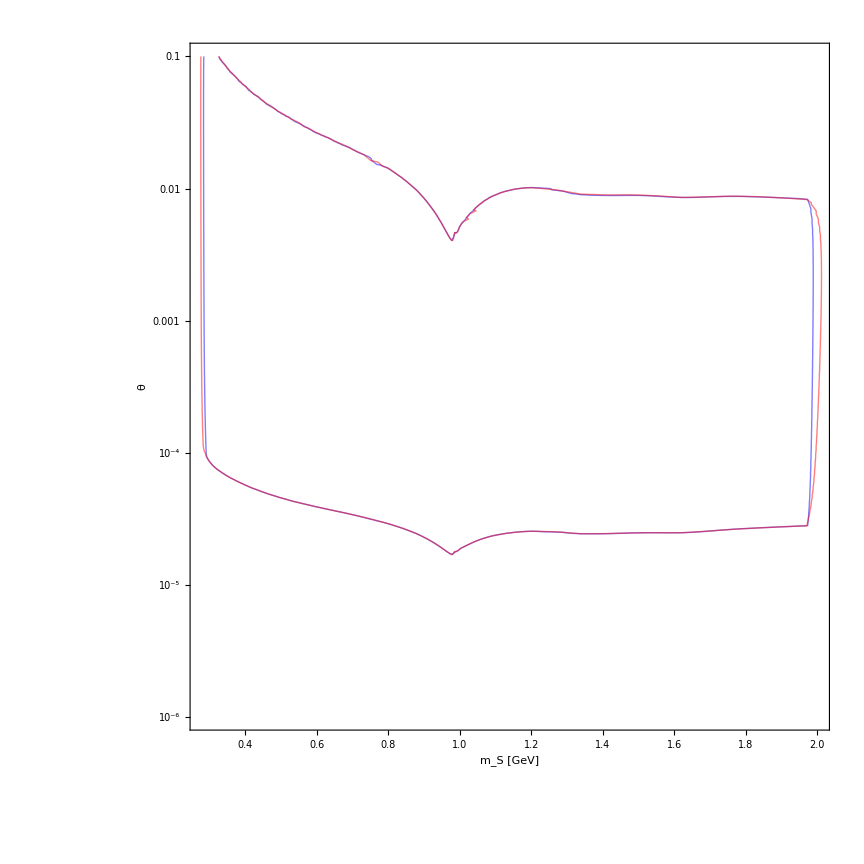

```mathematica
Show[contourN[dataArrayπK[[1]],Blue],contourN[dataArrayπKp[[1]],Red]]
```

#### plotdefs

```mathematica
labelNames={KP,KS700,KS1430,KV892,KV1410,KV1680,KA1270,KA1400,allKaons};
```

```mathematica
legend=ListContourPlot[{{0,0,0},{0,0,0},{0,0,0}},PlotLegends->LineLegend[Append[myColours,"Black"],labelNames]]
```

-Graphics-

```mathematica
contourN[data_,col_]:=Block[{dataRemapped = Table[{data[[i,1]],data[[i,2]],reMap@Re@data[[i,3]]},{i,1,Length@data}]},
Return@ListContourPlot[dataRemapped,Contours->{Log@3},ContourShading->None,ScalingFunctions->{None,"Log"},ContourStyle->{Directive[col]},AxesStyle->Directive[Black,14],FrameStyle->Directive[Black,14],LabelStyle->Directive[Black,14],FrameLabel->{"m_S [GeV]","θ"}];
]
```

#### Full

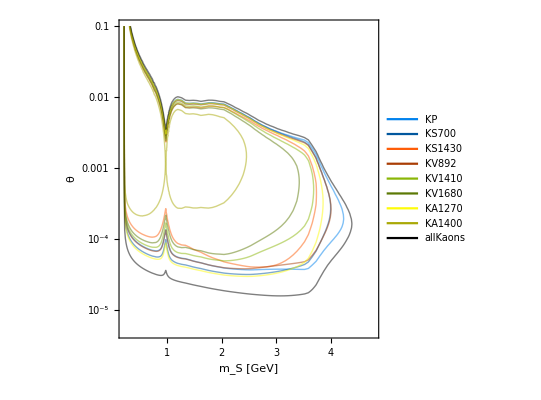

```mathematica
μμplot=Show[Table[contourN[Append[dataArrayμμ,totalArrayμμ][[i]],Append[myColours,"Black"][[i]]],{i,1,Length@funcNamesμμ +1}],PlotRange->{{2mμ/.masses,mB-mK/.masses},{Log[5*10^-6],Log[0.1]}}];
Show[μμplot,legend]
```

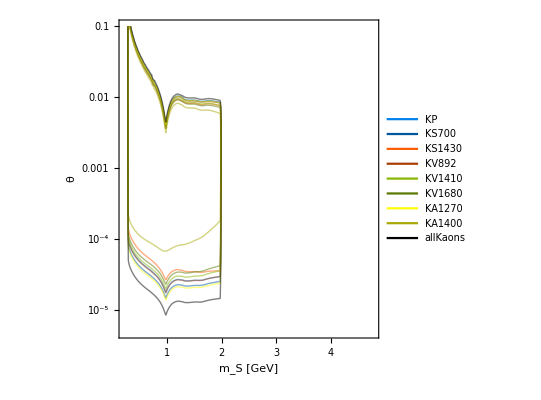

```mathematica
πKplot=Show[Table[contourN[Append[dataArrayπK,totalArrayπK][[i]],Append[myColours,"Black"][[i]]],{i,1,Length@funcNamesπK +1}],PlotRange->{{2mμ/.masses,mB-mK/.masses},{Log[5*10^-6],Log[0.1]}}];
Show[πKplot,legend]
```

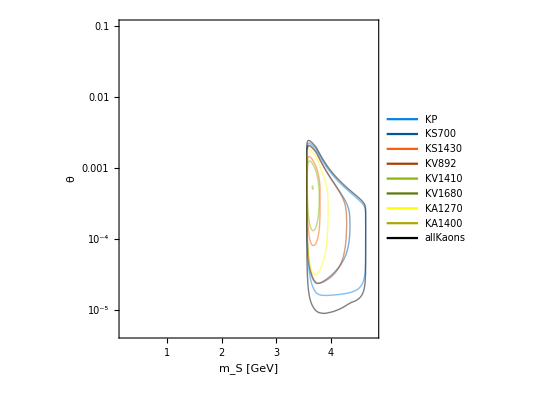

```mathematica
ττplot=Show[Table[contourN[Append[dataArrayττ,totalArrayττ][[i]],Append[myColours,"Black"][[i]]],{i,1,Length@funcNamesττ +1}],PlotRange->{{2mμ/.masses,mB-mK/.masses},{Log[5*10^-6],Log[0.1]}}];
Show[ττplot,legend]
```

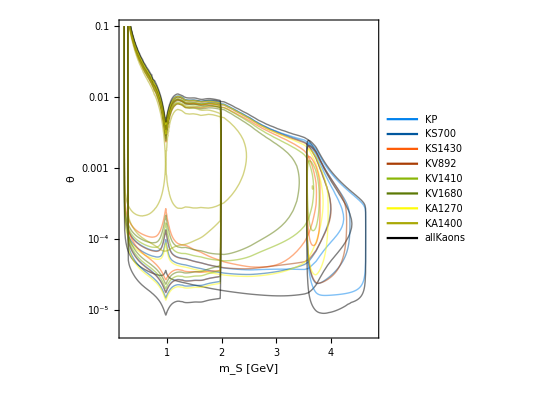

```mathematica
Show[μμplot,πKplot,ττplot,legend]
```

#### Single

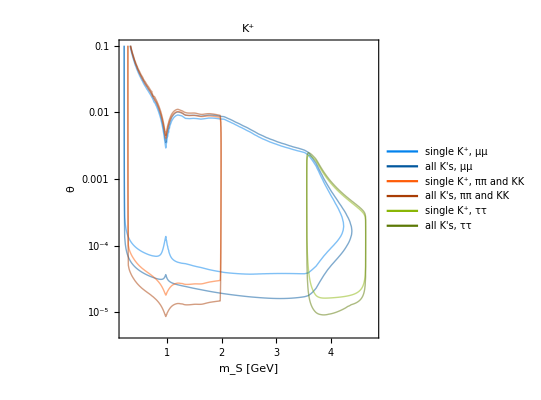

```mathematica
Show[contourN[dataArrayμμ[[1]],myColours[[1]]],contourN[totalArrayμμ,myColours[[2]]],contourN[dataArrayπK[[1]],myColours[[3]]],contourN[totalArrayπK,myColours[[4]]],contourN[dataArrayττ[[1]],myColours[[5]]],contourN[totalArrayττ,myColours[[6]]],ListContourPlot[{{0,0,0},{0,0,0},{0,0,0}},PlotLegends->LineLegend[myColours,{"single K^+, μμ", "all K's, μμ","single K^+, ππ and KK", "all K's, ππ and KK","single K^+, ττ", "all K's, ττ"}]],PlotLabel->"K^+",PlotRange->{{2mμ/.masses,mB-mK/.masses},{Log[5*10^-6],Log[0.1]}}]
```

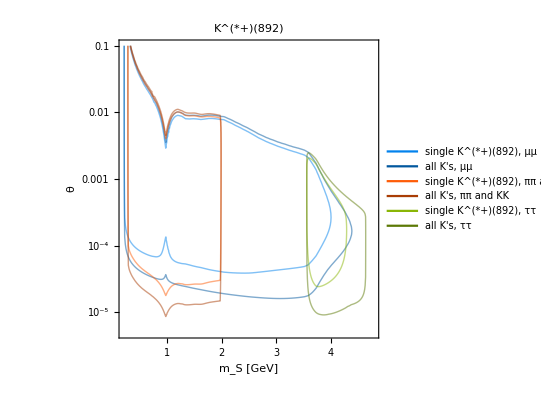

```mathematica
Show[contourN[dataArrayμμ[[4]],myColours[[1]]],contourN[totalArrayμμ,myColours[[2]]],contourN[dataArrayπK[[4]],myColours[[3]]],contourN[totalArrayπK,myColours[[4]]],contourN[dataArrayττ[[4]],myColours[[5]]],contourN[totalArrayττ,myColours[[6]]],ListContourPlot[{{0,0,0},{0,0,0},{0,0,0}},PlotLegends->LineLegend[myColours,{"single K^(*+)(892), μμ", "all K's, μμ","single K^(*+)(892), ππ and KK", "all K's, ππ and KK","single K^(*+)(892), ττ", "all K's, ττ"}]],PlotLabel->"K^(*+)(892)",PlotRange->{{2mμ/.masses,mB-mK/.masses},{Log[5*10^-6],Log[0.1]}}]
```

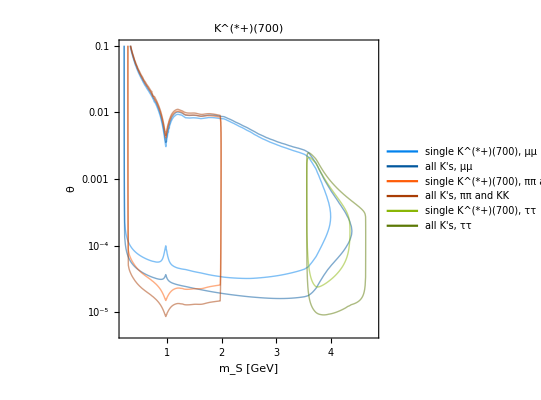

```mathematica
Show[contourN[dataArrayμμ[[2]],myColours[[1]]],contourN[totalArrayμμ,myColours[[2]]],contourN[dataArrayπK[[2]],myColours[[3]]],contourN[totalArrayπK,myColours[[4]]],contourN[dataArrayττ[[2]],myColours[[5]]],contourN[totalArrayττ,myColours[[6]]],ListContourPlot[{{0,0,0},{0,0,0},{0,0,0}},PlotLegends->LineLegend[myColours,{"single K^(*+)(700), μμ", "all K's, μμ","single K^(*+)(700), ππ and KK", "all K's, ππ and KK","single K^(*+)(700), ττ", "all K's, ττ"}]],PlotLabel->"K^(*+)(700)",PlotRange->{{2mμ/.masses,mB-mK/.masses},{Log[5*10^-6],Log[0.1]}}]
```

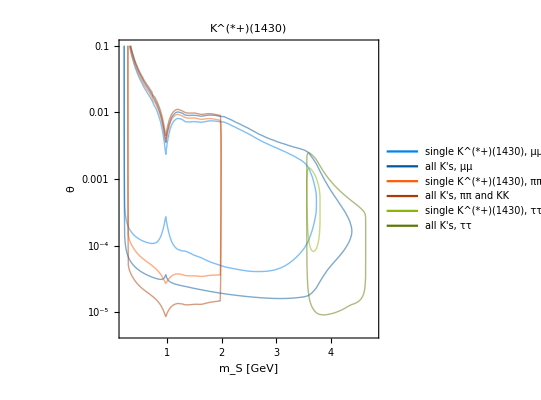

```mathematica
Show[contourN[dataArrayμμ[[3]],myColours[[1]]],contourN[totalArrayμμ,myColours[[2]]],contourN[dataArrayπK[[3]],myColours[[3]]],contourN[totalArrayπK,myColours[[4]]],contourN[dataArrayττ[[3]],myColours[[5]]],contourN[totalArrayττ,myColours[[6]]],ListContourPlot[{{0,0,0},{0,0,0},{0,0,0}},PlotLegends->LineLegend[myColours,{"single K^(*+)(1430), μμ", "all K's, μμ","single K^(*+)(1430), ππ and KK", "all K's, ππ and KK","single K^(*+)(1430), ττ", "all K's, ττ"}]],PlotLabel->"K^(*+)(1430)",PlotRange->{{2mμ/.masses,mB-mK/.masses},{Log[5*10^-6],Log[0.1]}}]
```

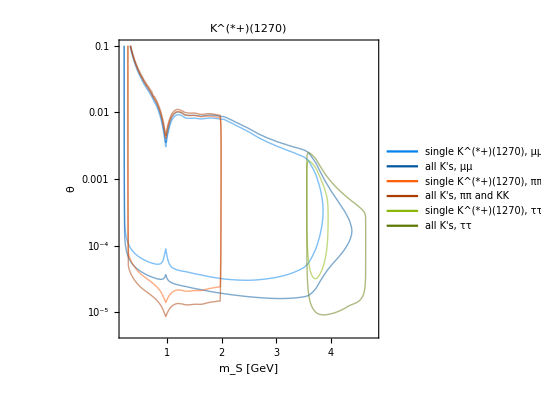

```mathematica
Show[contourN[dataArrayμμ[[7]],myColours[[1]]],contourN[totalArrayμμ,myColours[[2]]],contourN[dataArrayπK[[7]],myColours[[3]]],contourN[totalArrayπK,myColours[[4]]],contourN[dataArrayττ[[7]],myColours[[5]]],contourN[totalArrayττ,myColours[[6]]],ListContourPlot[{{0,0,0},{0,0,0},{0,0,0}},PlotLegends->LineLegend[myColours,{"single K^(*+)(1270), μμ", "all K's, μμ","single K^(*+)(1270), ππ and KK", "all K's, ππ and KK","single K^(*+)(1270), ττ", "all K's, ττ"}]],PlotLabel->"K^(*+)(1270)",PlotRange->{{2mμ/.masses,mB-mK/.masses},{Log[5*10^-6],Log[0.1]}}]
```

#### Their fig. 3

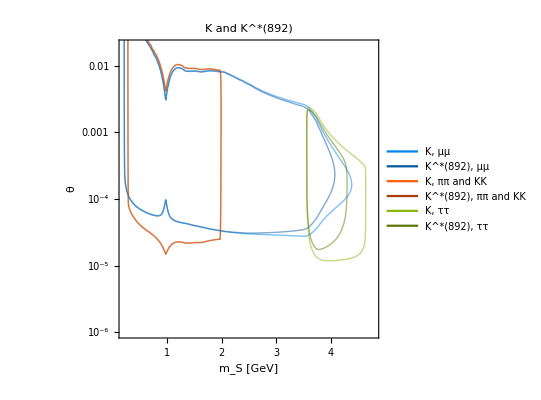

```mathematica
Show[contourN[dAμKs,myColours[[1]]],contourN[dAμKVs,myColours[[2]]],contourN[dAπKs,myColours[[3]]],contourN[dAπKVs,myColours[[4]]],contourN[dAτKs,myColours[[5]]],contourN[dAτKVs,myColours[[6]]],ListContourPlot[{{0,0,0},{0,0,0},{0,0,0}},PlotLegends->LineLegend[myColours,{"K, μμ", "K^*(892), μμ","K, ππ and KK", "K^*(892), ππ and KK","K, ττ", "K^*(892), ττ"}]],PlotLabel->"K and K^*(892)",PlotRange->{{2mμ/.masses,mB-mK/.masses},{Log[10^-6],Log[0.02]}}]
```

#### cmp. CDC ECL

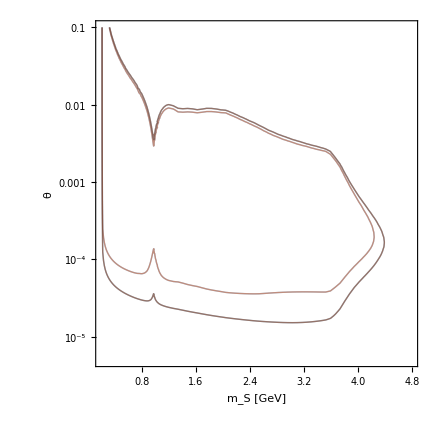

```mathematica
CEmumu=Show[contourN[dataArrayμμ[[1]],myColours[[1]]],contourN[dataArrayμμE[[1]],myColours[[3]]],contourN[totalArrayμμ,myColours[[2]]],contourN[totalArrayμμE,myColours[[4]]],PlotRange->{{2mμ/.masses,mB-mK/.masses},{Log[5*10^-6],Log[0.1]}}]
```

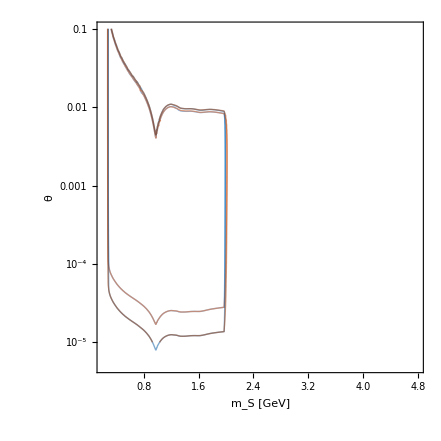

```mathematica
CEpik=Show[contourN[dataArrayπK[[1]],myColours[[1]]],contourN[dataArrayπKE[[1]],myColours[[3]]],contourN[totalArrayπK,myColours[[2]]],contourN[totalArrayπKE,myColours[[4]]],PlotRange->{{2mμ/.masses,mB-mK/.masses},{Log[5*10^-6],Log[0.1]}}]
```

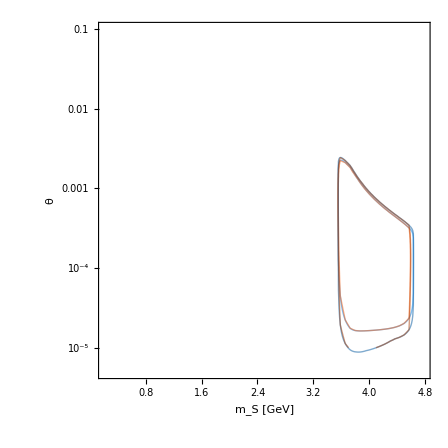

```mathematica
CEtautau=Show[contourN[dataArrayττ[[1]],myColours[[1]]],contourN[dataArrayττE[[1]],myColours[[3]]],contourN[totalArrayττ,myColours[[2]]],contourN[totalArrayττE,myColours[[4]]],PlotRange->{{2mμ/.masses,mB-mK/.masses},{Log[5*10^-6],Log[0.1]}}]
```

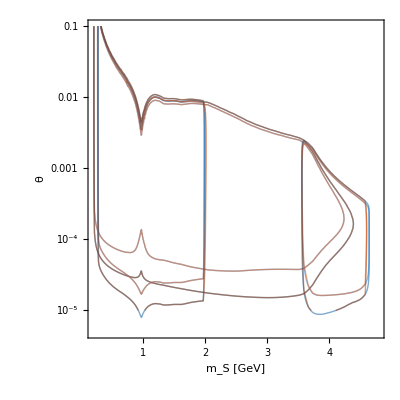

```mathematica
CE=Show[CEmumu,CEpik,CEtautau]
```